# Time complexity analysis of a recursive percolation detection algorithm

Daniel García Solla

## Initial functions

```mathematica
p=0.96
f[x_,y_]:=(p^Abs[x])*(p^Abs[y])
Plot3D[f[x,y],{x,-50,50},{y,-50,50}, PlotRange->{0,1}, ColorFunction->"AvocadoColors"]
```

0.96

-Graphics3D-

```mathematica
f2[x_,y_]:=p^(Abs[x]+Abs[y]+Abs[x+y]+Abs[y-x])
Plot3D[f2[x,y],{x,-50,50},{y,-50,50}, PlotRange->{0,1}, ColorFunction->"AvocadoColors",  PlotPoints->300]
```

-Graphics3D-

```mathematica
f3[x_,y_,z_]:=p^(Abs[x]+Abs[y]+Abs[z]+Abs[x+y]+Abs[y+z]+Abs[x+z]+Abs[x+y+z]+Abs[-x+y+z]+Abs[x-y+z]+Abs[x+y-z]+Abs[-x-y+z]+Abs[x-y-z])
Plot3D[f3[x,y, 0],{x,-50,50},{y,-50,50},PlotRange->{0,1},ColorFunction->"AvocadoColors",PlotPoints->300, ImageSize->Large]
```

-Graphics3D-

```mathematica
DensityPlot[f3[x,y,15],{x,-10,10},{y,-10,10},PlotRange->All,AxesLabel->{"x","y","z"},PlotLabel->"3D Plot of f3"]
ContourPlot3D[f3[x,y,z],{x,-10,10},{y,-10,10},{z,-10,10},Contours->{0.5},PlotRange->All,AxesLabel->{"x","y","z"},PlotLabel->"Contour Plot of f3"]
```

-Graphics-

-Graphics3D-

```mathematica
Plot3D[f[x,y],{x,0,50},{y,0,50}, PlotRange->{0,1}, ColorFunction->"AvocadoColors"]
Plot3D[f2[x,y],{x,0,50},{y,0,50}, PlotRange->{0,1}, ColorFunction->"AvocadoColors", PlotPoints->300]
```

-Graphics3D-

-Graphics3D-

Expected number of elements at x iteration

```mathematica
b[x_]:=n(1-(1-(1/n))^x);
```

## Calculate area under axis section (1D case)

```mathematica
Clear[p];
Integrate[f[x,0],{x,-Infinity,Infinity}]
Integrate[f2[x,0],{x,-Infinity,Infinity}]
Integrate[f2[x,0],{x,-Infinity,Infinity}, p]
```

Piecewise[{{-2/Log[p], Re[Log[p]]<0}, {Integrate[p^Abs[x],{x,-∞,∞},Assumptions→Re[Log[p]]≥0], True}}]

Piecewise[{{-2/(3 Log[p]), Re[Log[p]]<0}, {Integrate[p^(3 Abs[x]),{x,-∞,∞},Assumptions→Re[Log[p]]≥0], True}}]

ConditionalExpression[-2/3 ExpIntegralEi[Log[p]], Re[Log[p]]≤0]

```mathematica
Integrate[-2/(3Log[p]), p]
```

-(2 LogIntegral[p])/3

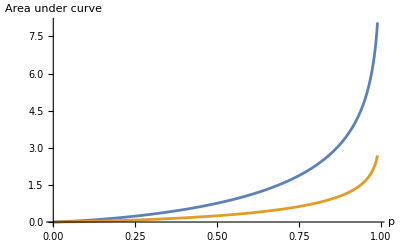

```mathematica
Plot[{-2LogIntegral[p], (-2/3)LogIntegral[p]},{p,0,0.99},PlotRange->All,AxesLabel->{"p","Area under curve"}]
```

### Calculate n exponent

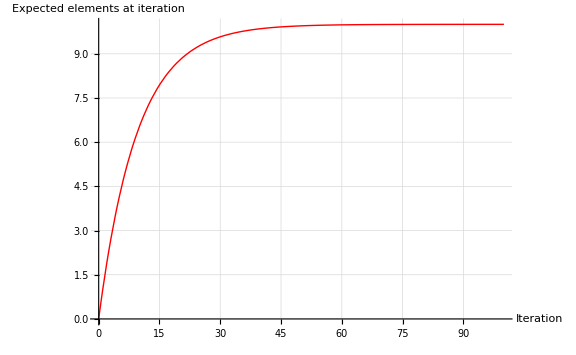

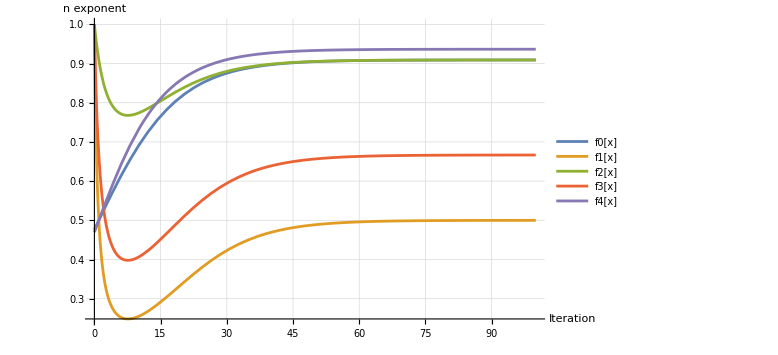

```mathematica
n=10;
b[x_]:=n(1-(1-(1/n))^x);
g[x_]:=(-2/3)LogIntegral[x]
g[x_]:=-2/(3 Log[x])
g[x_]:=(-1-x^3)/(-1+x^3)
g[x_]:=n/(n-(n*x)+1)
nexp0[x_]:=1*(g[b[x]/n])/(g[b[x]/n]+1)
nexp1[x_]:=1*(g[b[x]/n])/(g[b[x]/n] +b[x])
nexp2[x_]:=1*(g[b[x]/n])/(g[b[x]/n] +b[x]/n)
nexp3[x_]:=1*(g[b[x]/n])/(g[b[x]/n] +b[x]/2)
nexp4[x_]:=2/Pi *ArcTan[g[b[x]/n]]
Plot[{b[x]},{x,0,10*n},PlotRange->All, PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}},AxesLabel->{"Iteration","Expected elements at iteration"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}]
Plot[{nexp0[x], nexp1[x], nexp2[x], nexp3[x], nexp4[x]},{x,0, 10*n },PlotRange->Automatic,AxesLabel->{"Iteration","n exponent"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}, PlotLegends->{"f0[x]","f1[x]","f2[x]","f3[x]","f4[x]"}]
```

### Calculate insertion complexity

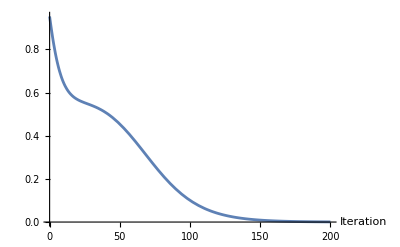

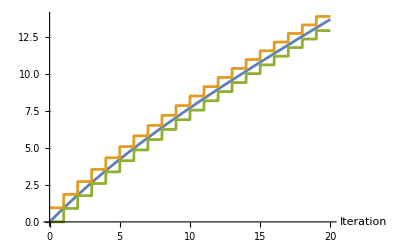

((1+(1-(1-1/n)^x)^3) (1-1/n)^x n)/(1+(1-(1-1/n)^x)^3+n-(1-(1-1/n)^x)^3 n)

$Aborted

$Aborted

$Aborted

j

$Aborted

```mathematica
n=20;
ins[x_]:=(1-b[x]/n)*n*((g[b[x]/n])/(g[b[x]/n]+n))
ins[x_]:=(1-b[x]/n)*(2 n)/(2-3 n Log[b[x]/n])
ins[x_]:=(1-b[x]/n)*b[x]
ins[x_]:=(1-b[x]/n)(n (1+(b[x]/n)^3))/(1+n+(b[x]/n)^3-n (b[x]/n)^3)
Plot[{ins[x]},{x, 0, 200},AxesLabel->{"Iteration"},PlotRange->Full]
Plot[{NIntegrate[ins[k],{k,0,q}],Sum[ins[k],{k,0,q}],Sum[ins[k],{k,0,q}]-ins[0]},{q, 0, 20},AxesLabel->{"Iteration"}]
Clear[n]
ins[x]
int[x_]:=Integrate[ins[k],k]/.k->x
sum[x_]:=Sum[ins[k],{k,0,x}]
int[x]//FunctionExpand//FullSimplify
sum[n*HarmonicNumber[n]]//FullSimplify
int[j]-int[0]//FullSimplify
(*Limit[(int[n*(HarmonicNumber[n]-HarmonicNumber[n-j])]-int[0]),n->Infinity]*)
Limit[(int[j]-int[0]),n->Infinity]
Limit[(int[n*HarmonicNumber[n]]-int[0])/((n*HarmonicNumber[n])^2),n->Infinity]
```

```mathematica
((1-b[x]/n)(n (1+(b[x]/n)^3))/(1+n+(b[x]/n)^3-n (b[x]/n)^3)//FullSimplify)
Sum[(1-b[x]/n)(n (1+(b[x]/n)^3))/(1+n+(b[x]/n)^3-n (b[x]/n)^3),{x,0,n*HarmonicNumber[n]}]
```

((1+(1-((-1+n)/n)^x)^3) ((-1+n)/n)^x n)/(1+(1-((-1+n)/n)^x)^3+n+(-1+((-1+n)/n)^x)^3 n)

1/(3 (-1+n) (1+n) Log[(-1+n)/n])n (-3 ((-1+n)/n)^(n HarmonicNumber[n]) Log[(-1+n)/n]-9 n Log[(-1+n)/n]-3 n^2 Log[(-1+n)/n]+3 ((-1+n)/n)^(n HarmonicNumber[n]) n^2 Log[(-1+n)/n]-6 n^2 HarmonicNumber[n] Log[(-1+n)/n]-2 n RootSum[2-3 #1+3 n #1+3 #1^2-3 n #1^2-#1^3+n #1^3&,QPolyGamma[0,-Log[#1]/Log[(-1+n)/n],(-1+n)/n]-QPolyGamma[0,-Log[#1]/Log[(-1+n)/n],(-1+n)/n] #1&]+2 n RootSum[2-3 #1+3 n #1+3 #1^2-3 n #1^2-#1^3+n #1^3&,QPolyGamma[0,1+n HarmonicNumber[n]-Log[#1]/Log[(-1+n)/n],(-1+n)/n]+Log[(-1+n)/n] #1+n HarmonicNumber[n] Log[(-1+n)/n] #1-QPolyGamma[0,1+n HarmonicNumber[n]-Log[#1]/Log[(-1+n)/n],(-1+n)/n] #1&])

```mathematica
Limit[((-Log[1+n]+Log[1+((-1+n)/n)^(n*HarmonicNumber[n]) n])/Log[(-1+n)/n])/(n*HarmonicNumber[n]),n->Infinity]
Limit[(Log[1+j-Log[-1/n]/Log[(-1+n)/n]]/(Log[1+((-1+n)/n)^j n])),n->Infinity]
Limit[(Log[-Log[-1/n]/Log[(-1+n)/n]]/Log[1+n]),n->Infinity]
```

1

1

1

NIntegrate::nlim: k = x is not a valid limit of integration.

NIntegrate[((1-b[k]/n) (2 n))/(2-3 n Log[b[k]/n]),{k,0,x},WorkingPrecision→30]

∑_(k=0)^x (2 (1-1/n)^k n)/(2-3 n Log[1-(1-1/n)^k])

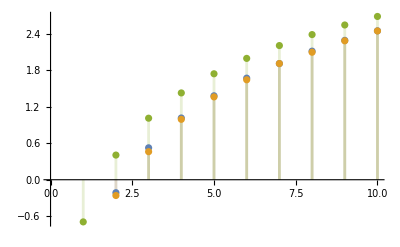

$Aborted

```mathematica
int[x_]:=Integrate[(1-b[k]/n)*(2 n)/(2-3 n Log[b[k]/n]),k]/.k->x
sum[x_]:=Sum[(1-b[k]/n)*(2 n)/(2-3 n Log[b[k]/n]),{k,0,x}]
int[x_]:=NIntegrate[(1-b[k]/n)*(2 n)/(2-3 n Log[b[k]/n]),{k,0,x},WorkingPrecision->30]
int[x]
sum[x]
DiscretePlot[{int[n*HarmonicNumber[n]]//Log,sum[n*HarmonicNumber[n]]//Log,0.5*n*HarmonicNumber[n]//Log},{n,0,10},AxesLabel->{"n"}]
Assuming[0<=k<1,Limit[(1-b[n*(Log[n]-Log[n-n^k])]/n)*(2 n)/(2-3 n Log[b[n*(Log[n]-Log[n-n^k])]/n]),n->Infinity]]
```

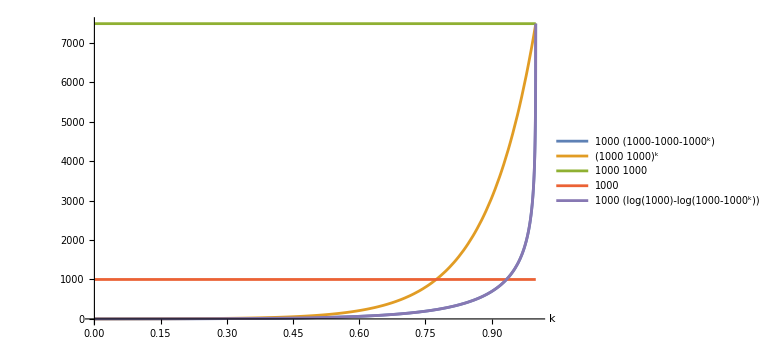

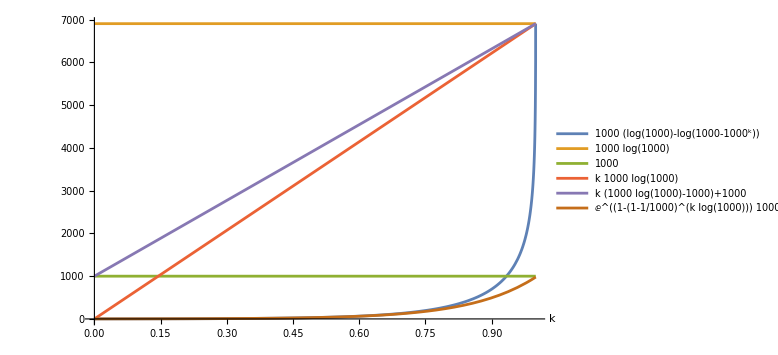

(1-1/n)^k

k (-1+n)^(-1+k) n^(-1-k)

```mathematica
n=1000;
Plot[{n*(HarmonicNumber[n]-HarmonicNumber[n-n^k]),(n*HarmonicNumber[n])^k,n*HarmonicNumber[n],n,n*(Log[n]-Log[n-n^k])},{k,0,1},PlotRange->{0,n*HarmonicNumber[n]},AxesLabel->{"k"},PlotLegends->"Expressions",ImageSize->Large]
Plot[{n*(Log[n]-Log[n-n^k]),n*Log[n],n,k*n*Log[n],k*(n*Log[n]-n)+n,ⅇ^((1-(1-1/n)^(k Log[n])) n)},{k,0,1},PlotRange->{0,n*Log[n]},AxesLabel->{"k"},PlotLegends->"Expressions",ImageSize->Large]
Clear[n]
(1-b[k]/n)
D[(1-b[k]/n),n]//FullSimplify
```

```mathematica
b[k]
```

(1-(1-1/n)^k) n

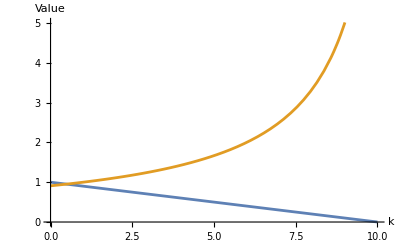

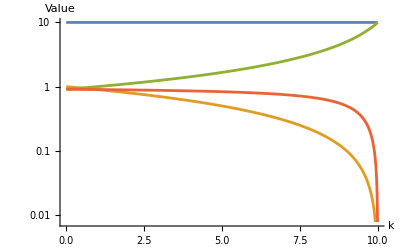

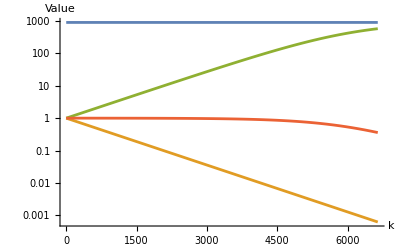

```mathematica
With[{n=10},Plot[{1-k/n,n/(n-k+1)},{k,0,n},AxesLabel->{"k","Value"}]]
With[{n=10},LogPlot[{n,1-k/n,n/(n-k+1),(1-k/n)*n/(n-k+1)},{k,0,n},AxesLabel->{"k","Value"}]]
With[{n=900},LogPlot[{n,1-((1-(1-1/n)^k) n)/n,n/(n-((1-(1-1/n)^k) n)+1),(1-((1-(1-1/n)^k) n)/n)*n/(n-((1-(1-1/n)^k) n)+1)},{k,0,n*HarmonicNumber[n]},AxesLabel->{"k","Value"}]]
```

```mathematica
Limit[b[n*Log[n]^k]/(n),n->Infinity]
```

(1-1/n)^k Log[1-1/n]

ConditionalExpression[1, k>1]

```mathematica
Clear[n]
f:=(n)*k
f:=(n*Log[n]^k)
f:=k*(n*Log[n]-n)+n
f:=n*(Log[n]-Log[n-n*k])
Assuming[0<=k<1,Limit[(1-b[f]/n)*n/(n-b[f]+1)//FullSimplify,n->Infinity]]
Assuming[0<=k<1,Limit[(1-b[f]/n),n->Infinity]]
Assuming[0<=k<1,Limit[n/(n-b[f]+1)//FullSimplify,n->Infinity]]
Assuming[0<=k<1,Limit[(1-b[f]/n)*E^(b[f/n])//FullSimplify,n->Infinity]]
Assuming[0<=k<1,Limit[(1-b[f]/n)/E^(-b[f/n])//FullSimplify,n->Infinity]]
Assuming[0<=k<1,Limit[n/(n-b[f]+1)/E^(b[f/n])//FullSimplify,n->Infinity]]
Assuming[0<=k<1,Limit[E^(-b[f/n])//FullSimplify,n->Infinity]]
E^(b[f/n])
(b[f]*Binomial[n,b[f]])/(Sum[x,{x,0,b[f]}]*Binomial[n,b[f]]) /E^(b[f/n])//FullSimplify
```

1

1-k

1/(1-k)

1

1

1

1-k

ⅇ^((1-(1-1/n)^(Log[n]-Log[n-k n])) n)

-(2 ⅇ^((-1+((-1+n)/n)^(Log[n]-Log[n-k n])) n))/(-1+(-1+((-1+n)/n)^(n (Log[n]-Log[n-k n]))) n)

```mathematica
Assuming[0<=k<1/2,Limit[(b[f]*Binomial[n,b[f]])/(Sum[x,{x,0,b[f]}]*Binomial[n,b[f]]) //FullSimplify,n->Infinity]]
Assuming[0<=k<1,Limit[(b[f]*Binomial[n,b[f]])/(b[f]*Binomial[n,b[f]]+(b[f]-1)*Binomial[n,b[f]])//FullSimplify,n->Infinity]]
```

0

1/2

```mathematica
(n*2*E^(2/(3*n))*(E^(Log[k/n]-2/(3*n))/(Log[k/n]-2/(3*n))))/(-3)//FullSimplify
Limit[(2 n*n^0.9)/(2-3 n Log[n^0.9/n])/((2/3)*n^0.9/Log[n^0.9/n]),n->Infinity]
Limit[(n*2*E^(2/(3*n))*(E^(Log[n^0.5/n]-2/(3*n))/(Log[n^0.5/n]-2/(3*n))))/(-3),n->Infinity]
WolframAlpha["Limit[n/(1 + n - (1 - E^(-Log[n])^k) n), n -> Infinity]"]
```

(2 k n)/(2-3 n Log[k/n])

-1.

∞

WolframAlphaQueryResults

```mathematica
int[x_]:=Integrate[(1-b[k]/n)*(2 n)/(2-3 n Log[b[k]/n]),k]/.k->x
Limit[(E^(Log[n^(1/10)/n]-2/(3*n))/(Log[n^(1/10)/n]-2/(3*n)))/(ExpIntegralEi[+Log[1-((-1+n)/n)^(n^(1/10))]-2/(3*n)]),n->Infinity]
Limit[(E^(Log[n^(1/3)/n]-2/(3*n))/(Log[n^(1/3)/n]-2/(3*n)))*n,n->Infinity]
Limit[(int[n*HarmonicNumber[n]]-int[0])/(n*HarmonicNumber[n]),n->Infinity]
f[x_]:=(1-b[x]/n)(n (1+(b[x]/n)^3))/(1+n+(b[x]/n)^3-n (b[x]/n)^3)
f[x]
int[x_]:=Integrate[f[k],k]/.k->x
sum[x_]:=Sum[f[q],{q,0,x}]
int[x]
ToRadicals@Normal[Sum[f[x],{x,0,n*HarmonicNumber[n]}]]//FullSimplify
```

1

-∞

2/3

((1+(1-(1-1/n)^x)^3) (1-1/n)^x n)/(1+(1-(1-1/n)^x)^3+n-(1-(1-1/n)^x)^3 n)

1/(3 (-1+n)^(4/3) (1+n)^(2/3) Log[(-1+n)/n])n (3 (-1+n)^(1/3) (1+n)^(2/3)-3 (-1+n)^(1/3) ((-1+n)/n)^x (1+n)^(2/3)+2 √3 n ArcTan[(-1+2 (-1+((-1+n)/n)^x) ((-1+n)/(1+n))^(1/3))/(√3)]+2 n Log[(-1+((-1+n)/n)^x) (-1+n)^(1/3)+(1+n)^(1/3)]-n Log[(-1+((-1+n)/n)^x)^2 (-1+n)^(2/3)-(-1+((-1+n)/n)^x) (-1+n)^(1/3) (1+n)^(1/3)+(1+n)^(2/3)])

1/(3 (-1+n)^2 (1+n) Log[(-1+n)/n])n (3 n^(-n HarmonicNumber[n]) (-1+n^2) ((-1+n)^(1+n HarmonicNumber[n])-n^(1+n HarmonicNumber[n])) (Log[-1+n]-Log[n])+n (-(-1+n)^2 (1+n))^(1/3) (2 QPolyGamma[0,Log[1+((-(-1+n)^2 (1+n))^(1/3))/(-1+n)]/(-Log[-1+n]+Log[n]),(-1+n)/n]-2 QPolyGamma[0,1+n HarmonicNumber[n]+Log[1+((-(-1+n)^2 (1+n))^(1/3))/(-1+n)]/(-Log[-1+n]+Log[n]),(-1+n)/n]+(-1-ⅈ √3) QPolyGamma[0,Log[1-(ⅈ (-ⅈ+√3) (-(-1+n)^2 (1+n))^(1/3))/(2 (-1+n))]/(-Log[-1+n]+Log[n]),(-1+n)/n]+(1+ⅈ √3) QPolyGamma[0,1+n HarmonicNumber[n]+Log[1-(ⅈ (-ⅈ+√3) (-(-1+n)^2 (1+n))^(1/3))/(2 (-1+n))]/(-Log[-1+n]+Log[n]),(-1+n)/n]+ⅈ (ⅈ+√3) (QPolyGamma[0,Log[1+(ⅈ (ⅈ+√3) (-(-1+n)^2 (1+n))^(1/3))/(2 (-1+n))]/(-Log[-1+n]+Log[n]),(-1+n)/n]-QPolyGamma[0,1+n HarmonicNumber[n]+Log[1+(ⅈ (ⅈ+√3) (-(-1+n)^2 (1+n))^(1/3))/(2 (-1+n))]/(-Log[-1+n]+Log[n]),(-1+n)/n])))

```mathematica
x:=n
Limit[((1+(1-(1-1/n)^x)^3) (1-1/n)^x n)/(1+(1-(1-1/n)^x)^3+n-(1-(1-1/n)^x)^3 n),n->Infinity]//FullSimplify
Limit[((1+(1-E^(-x/n))^3)E^(-x/n) n)/(1+(1-E^(-x/n))^3+n-(1-E^(-x/n))^3 n),n->Infinity]//FullSimplify
Clear[x]
```

((-1+2 ⅇ) (1+(-1+ⅇ) ⅇ))/(ⅇ (1+3 (-1+ⅇ) ⅇ))

((1+(-1+ⅇ)^3/ⅇ^3) ⅇ^2)/(1+3 (-1+ⅇ) ⅇ)

```mathematica
p[k_,j_,n_,m_]:=StirlingS2[k,j]*Factorial[n*m]/(Factorial[(n*m)-j]*(n*m)^k)
Table[Sum[(1-j/n)(n/(n-j+1))*p[x,j,n,1],{j,0,x}],{x,0,9}]//ExpandAll//FullSimplify
FindSequenceFunction[Table[Sum[(1-j/n)(n/(n-j+1))*p[x,j,n,1],{j,0,x}],{x,0,9}]//ExpandAll//FullSimplify,x]//FullSimplify
```

{n/(1+n),(-1+n)/n,(-1+(-1+n) n)/n^2,(-1+(-2+n) n (1+n))/n^3,(-1+n (-3+n (-3+(-1+n) n)))/n^4,((1+n+n^2) (-1+(-3+n) n (1+n)))/n^5,(-1+n (-5+n (-10+n (-10+n (-5+(-1+n) n)))))/n^6,(-1+n (1+n) (-6+n (-9+n (-11+n (-4+(-2+n) n)))))/n^7,(-1+n (-7+n (-21+n (-35+n (-35+n (-21+n (-7+(-1+n) n)))))))/n^8,(-1+n (1+n) (-8+n (-20+n (-36+n (-34+n (-22+n (-6+(-2+n) n)))))))/n^9}

1-((1+1/n)^x n)/(1+n)^2

```mathematica
Limit[Sum[1-((1+1/n)^x n)/(1+n)^2,{x,0,n*HarmonicNumber[n]}]/(n),n->Infinity]
```

∞

```mathematica
Limit[QPolyGamma[0,n,1]/Log[n],n->Infinity]
Limit[((Log[1+j-Log[-1/n]/Log[(-1+n)/n]]-1/(2(1+j-Log[-1/n]/Log[(-1+n)/n])))/Log[(-1+n)/n]-(Log[(-Log[-1/n])/Log[(-1+n)/n]]-1/(2((-Log[-1/n])/Log[(-1+n)/n])))/Log[(-1+n)/n]-sum[0]),n->Infinity]
Limit[(Log[1+j-Log[-1/n]/Log[(-1+n)/n]]/Log[(-1+n)/n]-Log[(-Log[-1/n])/Log[(-1+n)/n]]/Log[(-1+n)/n]-sum[0]),j->Infinity]
Limit[((Log[1+j-Log[-1/n]/Log[(-1+n)/n]]-1/(2(1+j-Log[-1/n]/Log[(-1+n)/n])))/Log[(-1+n)/n]-(Log[(-Log[-1/n])/Log[(-1+n)/n]]-1/(2(-Log[-1/n]/Log[(-1+n)/n])))/Log[(-1+n)/n]-sum[0])/((-Log[1+n]+Log[1+((-1+n)/n)^j n])/Log[(-1+n)/n]),n->Infinity]
```

1

-1

∞/Log[(-1+n)/n]

-1/j

### Get the max point

13.3418

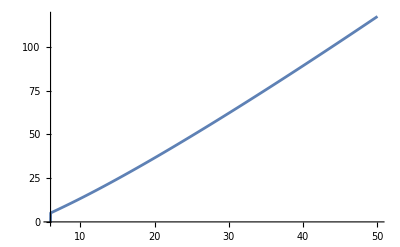

```mathematica
n=10;
puntoEstab:=Module[{result},result=NMaximize[{ins[x], x>0},x];
xOptimal=x/. result[[2]];xOptimal]
puntoEstab
Plot[{puntoEstab},{n, 6, 50}]
(*Plot[{NIntegrate[ins[x], {x, 0, puntoEstab}]},{n, 2, 4}]*)
```

### Sum insertion complexity until the algorithm ends

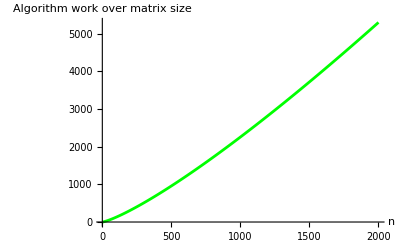

```mathematica
LaunchKernels[];
Clear[n];
points=ParallelTable[{n, NIntegrate[ins[x],{x,0,n^1.2}, WorkingPrecision->10]},{n, 2, 2000}];
ListLinePlot[{points},PlotRange->All,AxesLabel->{"n","Algorithm work over matrix size"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
CloseKernels[];
```

### Fit the sum points

{-0.90823243,1.2489863}

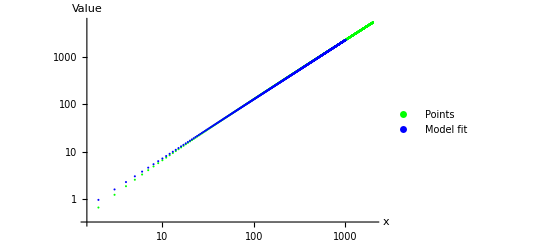

```mathematica
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x, IncludeConstantBasis->True];
fittedLine=linearModel["Function"];
linearModel["BestFitParameters"]
ListLogLogPlot[{points, Table[{x,E^fittedLine[x]},{x,2,1000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right]]
```

FittedModel[…]

#1^1.123988928&

| DF | SS | MS
Model | 2 | 1.61886977×10^10 | 8.09434887×10^9
Error | 1997 | 1.73697×10^7 | 8697.898
Uncorrected Total | 1999 | 1.62060674×10^10 | 
Corrected Total | 1998 | 4.9402343×10^9 |

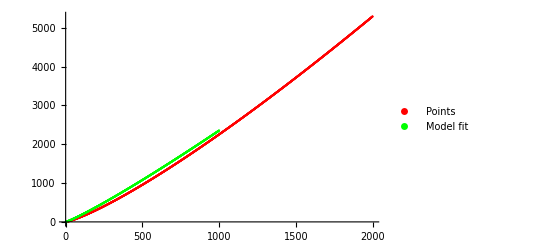

```mathematica
nonlinearModel=NonlinearModelFit[points,1*x^c ,{a,c},x]
nonlinearModel["Function"]
nonlinearModel["ANOVATable"]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,1000}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right]]
```

### Analysis using real average cluster size

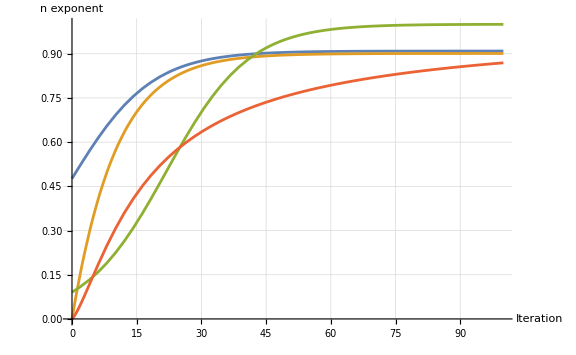

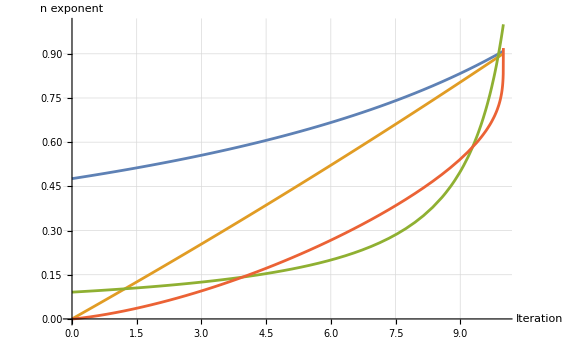

```mathematica
n=10;
b[x_]:=n(1-(1-(1/n))^x);
g[x_]:=n/(n-(n*x)+1)
h[x_]:=n/(n-(n*x)+1)-(n/(n+1))
nexp0[x_]:=1*(g[b[x]/n])/(g[b[x]/n]+1)
Plot[{nexp0[x],(h[b[x]/n])/(h[b[x]/n]+1),g[b[x]/n]/n,(-2/3)LogIntegral[b[x]/n]/((-2/3)LogIntegral[b[x]/n]+1)},{x,0, 10*n },PlotRange->Full,AxesLabel->{"Iteration","n exponent"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}]
Plot[{g[x/n]/(g[x/n]+1),(h[x/n])/(h[x/n]+1),g[x/n]/n,(-2/3)LogIntegral[x/n]/((-2/3)LogIntegral[x/n]+1)},{x,0,n},PlotRange->Full,AxesLabel->{"Iteration","n exponent"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}]
```

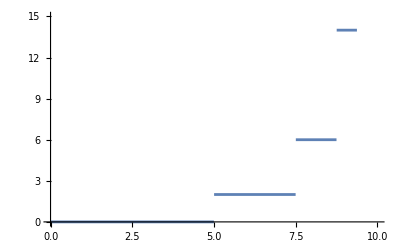

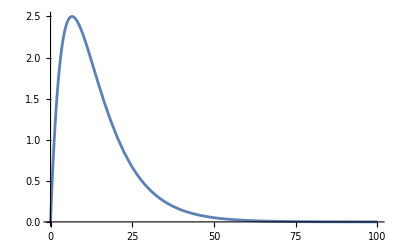

(-1+n)^x n^(1-2 x) (-(-1+n)^x+n^x)

{-((-1+((-1+n)/n)^(n HarmonicNumber[n]))^2 n)/(2 (Log[-1+n]-Log[n])),((-1+n) n^(1-2 n HarmonicNumber[n]) (-(-1+n)^(n HarmonicNumber[n])+n^(n HarmonicNumber[n])) (-(-1+n)^(1+n HarmonicNumber[n])+n^(1+n HarmonicNumber[n])))/(-1+2 n)}

∞

1/2

j^2/2

j^2/2

```mathematica
n=10;
ins[x_]:=(1-b[x]/n)*g[b[x]/n]
ins[x_]:=(1-b[x]/n)*((-2+2^Floor[Log2[2*n/(n-b[x])]]))
ins[x_]:=(1-b[x]/n)*b[x]
Plot[((-2+2^Floor[Log2[2*n/(n-k)]])),{k,0,n}]
Plot[{ins[x]},{x, 0, 10n}]
Clear[n]
ins[x]//FunctionExpand//FullSimplify
c[x_]:=(Integrate[ins[k]//FunctionExpand,k]/. k->x)//FullSimplify
c2[x_]:=(Sum[ins[k],{k,0,x}])//FunctionExpand//FullSimplify
{c[n*HarmonicNumber[n]]-c[0],c2[n*HarmonicNumber[n]]-c2[0]}//FullSimplify
Limit[(c[n*HarmonicNumber[n]]-c[0])/(n^1 HarmonicNumber[n])//FullSimplify,n->Infinity]
Limit[(c[n*HarmonicNumber[n]]-c[0])/(n^2),n->Infinity]
Limit[(c[n*(HarmonicNumber[n]-HarmonicNumber[n-j])]-c[0]),n->Infinity]
Limit[(c[j]-c[0]),n->Infinity]
```

```mathematica
Integrate[ins[x]x,{x,0,Infinity}]//FullSimplify
```

ConditionalExpression[-(2 n (n+(1+n)^2 PolyLog[2,-n/(1+n+n^2)]))/Log[(-1+n)/n]^2, Re[Log[(-1+n)/n]]<0]

```mathematica
Limit[(c[-(2 n (n+(1+n)^2 PolyLog[2,-n/(1+n+n^2)]))/Log[(-1+n)/n]^2]-c[0])/(n^2),n->Infinity]
```

1

```mathematica
Integrate[ins[x],{x,0,Infinity}]//FullSimplify
```

ConditionalExpression[(2 n (n-(1+n)^2 Log[(1+n)^2]+(1+n)^2 Log[1+n+n^2]))/Log[(-1+n)/n], Re[n (2+n)]≥-1&&Re[Log[(-1+n)/n]]<0]

```mathematica
Integrate[ins[x]x/((2 n (n-(1+n)^2 Log[(1+n)^2]+(1+n)^2 Log[1+n+n^2]))/Log[(-1+n)/n]),{x,0,Infinity}]//FullSimplify
```

ConditionalExpression[-(n+(1+n)^2 PolyLog[2,-n/(1+n+n^2)])/(Log[(-1+n)/n] (n-(1+n)^2 Log[(1+n)^2]+(1+n)^2 Log[1+n+n^2])), Re[Log[(-1+n)/n]]<0]

```mathematica
Limit[(c[-(n+(1+n)^2 PolyLog[2,-n/(1+n+n^2)])/(Log[(-1+n)/n] (n-(1+n)^2 Log[(1+n)^2]+(1+n)^2 Log[1+n+n^2]))]-c[0])/(n^2),n->Infinity]
```

((-1+ⅇ^(3/2))^2)/ⅇ^3

### Distribution of iterations before process ends

60

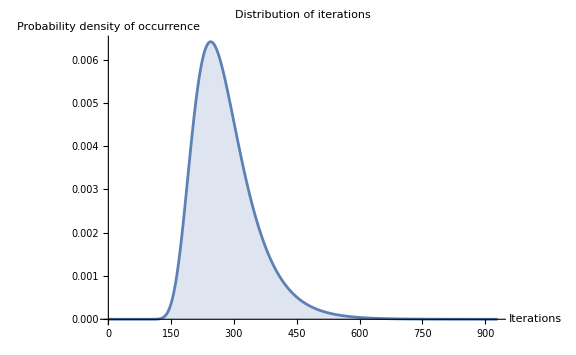

245

280.792

```mathematica
n=60
distr[i_]:=(Factorial[n]/(n^i))*StirlingS2[i-1,n-1]
iValues=Range[1,2 n^1.5,1];
maxIndex=First@Ordering[Table[distr[i],{i,iValues}],-1];
DiscretePlot[{distr[i]},{i,iValues},AxesLabel->{"Iterations","Probability density of occurrence"},PlotLabel->"Distribution of iterations",PlotRange->Full,ImageSize->Large]
maxIndex
N[(n*Sum[1/j,{j,1,n}])]
```

Approach the Coupon Collector Problem distribution (m=1)

{Piecewise[{{n^-k n! StirlingS2[k,n], k≥n}, {0, True}}],Piecewise[{{n^-k n! (-n StirlingS2[-1+k,n]+StirlingS2[k,n]), k≥1+n}, {n^-k n! StirlingS2[k,n], k≥n}, {0, True}}]}

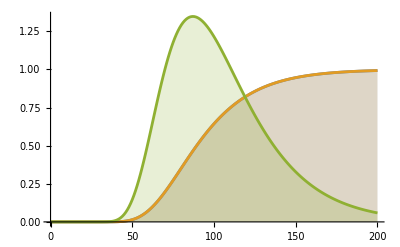

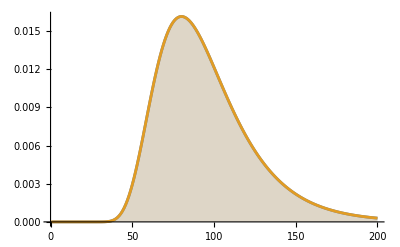

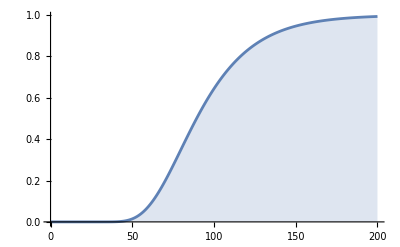

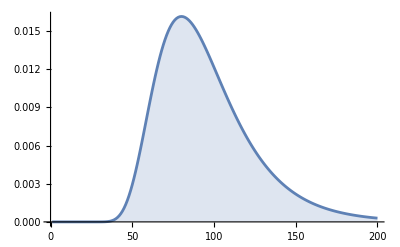

```mathematica
b[x_]:=n*(1-(1-(1/n))^x)
p[k_,j_,n_,m_]:=StirlingS2[k,j]*Factorial[n*m]/(Factorial[(n*m)-j]*(n*m)^k)
ratio[n_,k_]:=Sum[p[k,j,n,1]*KroneckerDelta[n,j]/Binomial[n,Min[n,j]]//FullSimplify,{j,1,k}]
distr[n_,k_]:=ratio[n,k]-ratio[n,k-1]
FullSimplify[{ratio[n,k],distr[n,k]},Assumptions->{n∈PositiveIntegers,k∈PositiveIntegers}]
n=25;
DiscretePlot[{(Factorial[n]/(n^k))*StirlingS2[k,n],ratio[n,k],(Factorial[n]/(n^k))*StirlingS2[k-1,n-1]*k},{k,0,200}]
DiscretePlot[{(Factorial[n]/(n^k))*StirlingS2[k-1,n-1],distr[n,k]},{k,0,200}]
DiscretePlot[{(Factorial[n]/(n^k))*StirlingS2[k,n]},{k,0,200},AxesLabel->{"Iteration"}]
DiscretePlot[{(Factorial[n]/(n^k))*StirlingS2[k-1,n-1]},{k,0,200},AxesLabel->{"Iteration"}]
Clear[n]
```

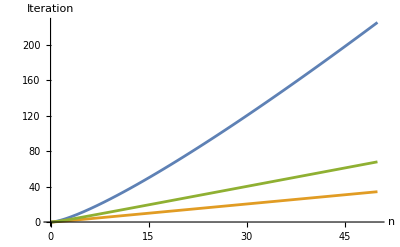

```mathematica
Plot[{n*HarmonicNumber[n],n*(HarmonicNumber[n]-HarmonicNumber[n-n/2]),n*(HarmonicNumber[n]-HarmonicNumber[n-(3/4)*n])},{n,0,50},AxesLabel->{"n","Iteration"}]
```

Calculate mean of m=1 distribution😋

```mathematica
Clear[n]
FullSimplify[Sum[Sum[(Factorial[n]/(n^x))*((1/(n-1)!)*(-1)^(j+n-1)  Binomial[n-1,j]  j^(x-1))x//FullSimplify,{x,0,Infinity}]//FunctionExpand,{j,0,n-1}],Assumptions->{n∈PositiveIntegers}]
```

n HarmonicNumber[n]

```mathematica
StirlingS2[47,2]
Stir[n_,k_]:=1/k! Sum[(-1)^j Binomial[k,j] (k-j)^n,{j,0,k}]
```

70368744177663

StirlingS2[n,k]

70368744177663

```mathematica
seq[x_]:=Sum[(Factorial[n]/(n^i))*StirlingS2[i,n],{i,0,Infinity}]
Table[seq[x],{x,0,10}]//FullSimplify
FindSequenceFunction[Table[seq[x],{x,0,10}]//FullSimplify]
```

{∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n]}

FindSequenceFunction[{∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n],∑_(i=0)^∞ n^-i n! StirlingS2[i,n]}]

```mathematica
Clear[n]
FunctionExpand[Binomial[n,b[k]]]
FullSimplify[FunctionExpand[distr[x,k]]]
DiscretePlot3D[Gamma[1+n]/(Gamma[1+n-(-1+n)^k n^(1-k)] Gamma[1+(-1+n)^k n^(1-k)]),{k,1,70},{n,40,50},ImageSize->Medium]
```

Gamma[1+n]/(Gamma[1+n-(-1+n)^k n^(1-k)] Gamma[1+(-1+n)^k n^(1-k)])

1/Gamma[1+k]n^-k Gamma[1+k+(-1+((-1+n)/n)^k) n] Gamma[1+n-(-1+n)^k n^(1-k)] (n^k (-HarmonicNumber[k]+HarmonicNumber[k+(-1+((-1+n)/n)^k) n])+(-1+n)^k n (HarmonicNumber[k+(-1+((-1+n)/n)^k) n]-HarmonicNumber[n-(-1+n)^k n^(1-k)]) (Log[-1+n]-Log[n]))

-Graphics3D-

## Calculate volume under the functions (square 2D case)

```mathematica
Clear[p];
Integrate[f[x,y],{x,0,Infinity},{y,0,Infinity}, p]
```

ConditionalExpression[-p/Log[p]+LogIntegral[p], Log[p]≤0]

```mathematica
Integrate[f2[x,y],{x,0,Infinity},{y,0,Infinity}]
```

Piecewise[{{1/(6 Log[p]^2), Re[Log[p]]<0}, {Integrate[p^(Abs[x]+Abs[y]+Abs[-x+y]+Abs[x+y]),{x,0,∞},{y,0,∞},Assumptions→Re[Log[p]]≥0], True}}]

```mathematica
4*Integrate[1/(6 Log[p]^2),p]
```

2/3 (-p/Log[p]+LogIntegral[p])

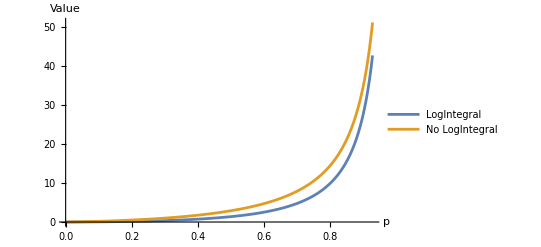

```mathematica
Plot[{4 (-p/Log[p]+LogIntegral[p]), 4 (-p/Log[p])},{p,0,0.93},PlotRange->All,AxesLabel->{"p","Value"}, PlotLegends->{"LogIntegral","No LogIntegral"}]
```

### Calculate n exponent

10

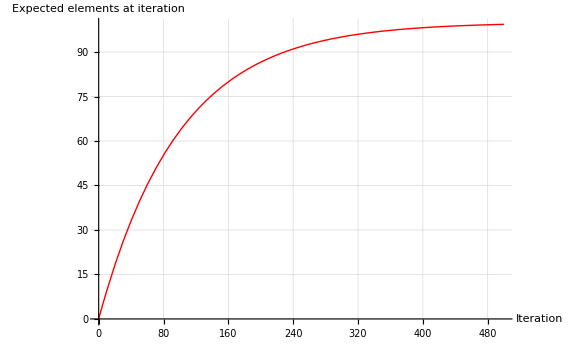

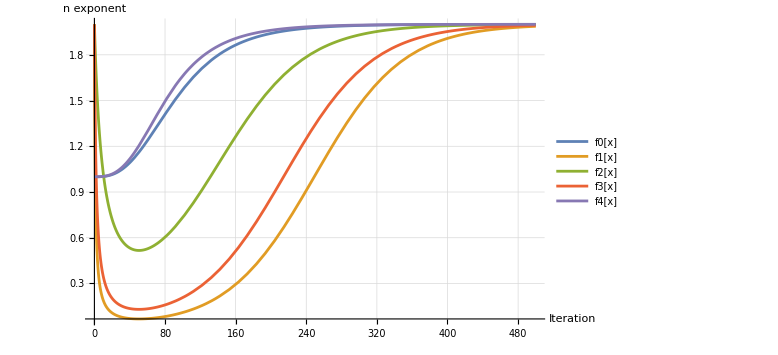

```mathematica
n=10
b[x_]:=(n^2)*(1-(1-(1/n^2))^x);
g[x_]:=(2/3)*(-x/Log[x]+LogIntegral[x])
g[x_]:=((n^(n^2*x))/((n^(2)-n^2*x) n^((n^2*x)-2)))
g[x_]:=n^2/(n^2-(n^2*x)+1)
g[x_]:=2/(3 Log[x]^2)
g[x_]:=(1+x (-1+x+2 x^2+x^3-x^4+x^5))/((-1+x)^2 (1+x^2) (1+x+x^2))
nexp0[x_]:=2*(g[b[x]/n^2])/(g[b[x]/n^2] +1)
nexp1[x_]:=2*(g[b[x]/n^2])/(g[b[x]/n^2] +b[x])
nexp2[x_]:=2*(g[b[x]/n^2])/(g[b[x]/n^2] +b[x]/n)
nexp3[x_]:=2*(g[b[x]/n^2])/(g[b[x]/n^2] +b[x]/2)
nexp4[x_]:=4/Pi *ArcTan[g[b[x]/n^2]]
Plot[{b[x]},{x,0,5*n^2},PlotRange->All, PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}},AxesLabel->{"Iteration","Expected elements at iteration"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}]
Plot[{nexp0[x], nexp1[x], nexp2[x], nexp3[x], nexp4[x]},{x,0, 5*n^2 },PlotRange->All,AxesLabel->{"Iteration","n exponent"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}, PlotLegends->{"f0[x]","f1[x]","f2[x]","f3[x]","f4[x]"}]
```

### Calculate insertion complexity

```mathematica
b[x]
```

(1-(1-1/n^2)^x) n^2

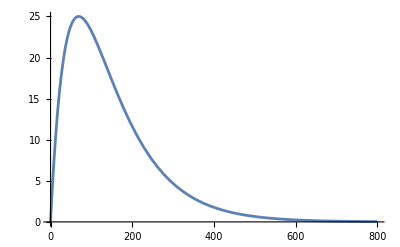

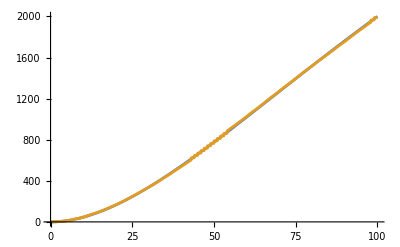

-((-1+(1-1/n^2)^x) (1-1/n^2)^x n^2)

-((-1+(1-1/n^2)^j)^2 n^2)/(2 Log[1-1/n^2])

((-1+(1-1/n^2)^x) n^2 (-1+n^2) (-n^2+(1-1/n^2)^x (-1+n^2)))/(-1+2 n^2)

0

j^2/2

1/2 j (1+j)

```mathematica
n=10;
ins[x_]:=(1-b[x]/n^2)
ins[x_]:=(1-b[x]/n^2)*((b[x]*binomAprox[n^2,b[x]])/(b[x]*binomAprox[n^2,b[x]]+(b[x]-1)(8*binomAprox[b[x],2]/(n^2-1))))
ins[x_]:=(1-b[x]/n^2)*(n^2)*((g[b[x]/n^2])/(g[b[x]/n^2] +n^2))
ins[x_]:=(1-b[x]/n^2)*b[x]
Plot[{ins[x]},{x, 0, 8n^2}]
Plot[{NIntegrate[ins[x], {x, 0, q}],Sum[ins[k],{k,0,q}]},{q, 0, 100}]
Clear[n]
ins[x]//FullSimplify
int[x_]:=Integrate[ins[k],k]/.k->x
sum[x_]:=Sum[ins[q]//FullSimplify,{q,0,x}]//FullSimplify
int[j]-int[0]//FullSimplify
sum[x]//FullSimplify
Limit[(int[n^2*HarmonicNumber[n^2]]-int[0])/((n^2*HarmonicNumber[n^2])^2),n->Infinity]
Limit[(int[j]-int[0]),n->Infinity]
Limit[(sum[j]),n->Infinity]
```

```mathematica
Limit[(1/2)*n^4*(Exp[-2*j/n^2]-2*Exp[-j/n^2]+1),n->Infinity]
Limit[(j*n^2*(Exp[j/n^2]-1))/(2*Exp[2*j/n^2]),n->Infinity]
Limit[(j*n^2*(Exp[j/n^2]-1))/(2),n->Infinity]
Limit[(Exp[j/n^2]*j*j)/(2),n->Infinity]
Limit[(1/2)*((1-1/n^2)^(2*n^2*HarmonicNumber[n^2])-2*(1-1/n^2)^(n^2*HarmonicNumber[n^2])+1),n->Infinity]
Limit[(1/2)*(E^(-2*n^2*HarmonicNumber[n^2]/n^2)-2*E^(-n^2*HarmonicNumber[n^2]/n^2)+1),n->Infinity]
Limit[(n^2*(n^2-1)*(Exp[-j/n^2]-1)*((n^2-1)*Exp[-j/n^2]-n^2))/(2*n^2-1),n->Infinity]
Limit[(((-j/n^2)) n^2 (-1+n^2) (-n^2+(1-j/n^2) (-1+n^2)))/(-1+2 n^2),n->Infinity]
Limit[(1-1/n^2)^(2 n^2 HarmonicNumber[n^2]),n->Infinity]
(sum[n^2*HarmonicNumber[n^2]]/n^4)//FullSimplify
```

j^2/2

j^2/2

j^2/2

«1 more identical outputs»

1/2

1/2

1/2 j (1+j)

1/2 (j+j^2)

0

(-n^2+n^4+(1-1/n^2)^(2 n^2 HarmonicNumber[n^2]) (-1+n^2)^2+(1-1/n^2)^(n^2 HarmonicNumber[n^2]) (-1+3 n^2-2 n^4))/(n^2 (-1+2 n^2))

```mathematica
WolframAlpha["Limit[(-n^2 + n^4 + (1 - 1/n^2)^(
  2 n^2 HarmonicNumber[n^2]) (-1 + n^2)^2 + (1 - 1/n^2)^(
  n^2 HarmonicNumber[n^2]) (-1 + 3 n^2 - 2 n^4))/(n^2 (-1 + 2 n^2)), 
 n -> Infinity]"]
```

WolframAlphaQueryResults

```mathematica
Limit[b[n^2(HarmonicNumber[n^2]-HarmonicNumber[n^2-k])],n->Infinity]
```

k

```mathematica
Clear[n]
f:=n^2*(Log[n^2]-Log[n^2-(n^(2)*k)])
Assuming[0<=k<1,Limit[(1-b[f]/n^2),n->Infinity]]
Assuming[0<=k<1,Limit[(1-b[n^2*HarmonicNumber[n^2]]/n^2),n->Infinity]]
Assuming[0<=k<1,Limit[n^2/(n^2-b[f]+1)//FullSimplify,n->Infinity]]
```

1

0

1

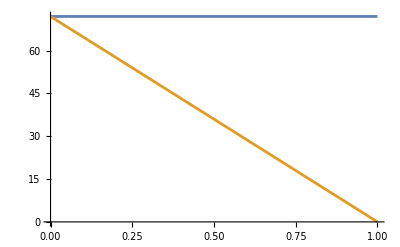

1/2 n HarmonicNumber[n^9]

```mathematica
With[{n=20},Plot[{n*HarmonicNumber[n],(n*HarmonicNumber[n])*(-k+1)},{k,0,1}]]
Integrate[(-(k/(n*HarmonicNumber[n^9]))+1),{k,0,n*HarmonicNumber[n^9]}]
```

```mathematica
Clear[n]
f:=(n^2)*(HarmonicNumber[n^(3/2)])
Limit[(1-b[f]/n^2)*n^2/(n^2-b[f]+1),n->Infinity]
Limit[n^2/(n^2-b[f]+1),n->Infinity]
Limit[(1-b[f]/n^2),n->Infinity]
Assuming[0<=k<1,Limit[((k*n^2)*Binomial[n^2,k*n^2])/Sum[x*Binomial[n^2,k*n^2],{x,(k*n^2)-1,k*n^2}]//FullSimplify,n->Infinity]]//FunctionExpand
Limit[(k*Binomial[n^2,k])/(k*(Binomial[n^2,k]-9n^(2*k-2)/(2Factorial[k-2]))+(k-1)(Binomial[n^2,k]-(n^(2*k)/Factorial[k]-9n^(2*k-2)/(2Factorial[k-2])))),n->Infinity]
```

1

∞

0

1/2

(k Gamma[-1+k])/((-1+2 k) Gamma[-1+k]-Gamma[k])

```mathematica
Limit[(k Gamma[-1+k])/((-1+2 k) Gamma[-1+k]-Gamma[k])/.k->n^1,n->Infinity]
```

1

```mathematica
Limit[ins[x],n->Infinity]
```

x

```mathematica
derivative=D[ins[x],x]
```

(1-1/n^2)^x n^((4 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))/(3 (1+2/3 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x])))) Log[1-1/n^2]+(1-1/n^2)^x n^((4 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))/(3 (1+2/3 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x])))) Log[n] ((8 (1-1/n^2)^x Log[1-1/n^2] (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))/(9 Log[1-(1-1/n^2)^x]^2 (1+2/3 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))^2)-(4 (1-1/n^2)^x Log[1-1/n^2])/(3 Log[1-(1-1/n^2)^x]^2 (1+2/3 (-(1-(1-1/n^2)^x)/Log[1-(1-1/n^2)^x]+LogIntegral[1-(1-1/n^2)^x]))))

### Get the max point (precision fails😊)

2.26093×10^-9

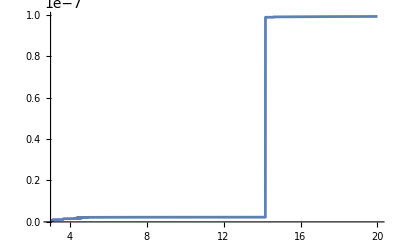

```mathematica
n=10;
puntoEstab:=Module[{result},result=NMaximize[{ins[x], x>0},x];
xOptimal=x/. result[[2]];xOptimal]
puntoEstab
Plot[{puntoEstab},{n, 3, 20}]
```

### Sum insertion complexity until the algorithm ends

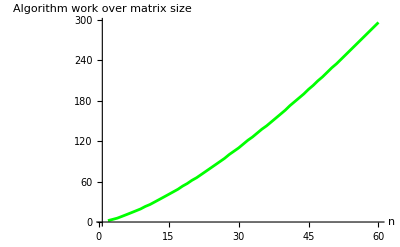

```mathematica
LaunchKernels[];
Clear[n]
points=ParallelTable[{n, Sum[ins[x],{x,0,(n^1.4)}]},{n, 2, 60}];
ListLinePlot[{points},PlotRange->All,AxesLabel->{"n","Algorithm work over matrix size"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
CloseKernels[];
```

### Fit the sum points (finally🤝)

{-0.194726,1.43924}

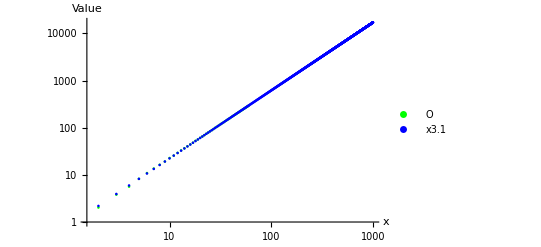

```mathematica
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x];
fittedLine=linearModel["Function"];
linearModel["BestFitParameters"]
ListLogLogPlot[{points, Table[{x,E^fittedLine[x]},{x,2,1000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
```

1.38795
FittedModel[x       ]

#1^1.38795&

| DF | SS | MS
Model | 1 | 1.41257×10^6 | 1.41257×10^6
Error | 58 | 170.754 | 2.94404
Uncorrected Total | 59 | 1.41274×10^6 | 
Corrected Total | 58 | 466124. |

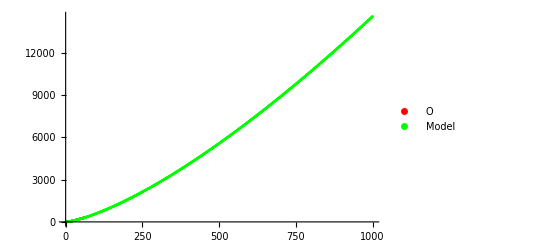

```mathematica
nonlinearModel=NonlinearModelFit[points,x^c,{c},x]
nonlinearModel["Function"]
nonlinearModel["ANOVATable"]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,1000}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"O","Model"}],Right]]
```

### Distribution of iterations before process ends

```mathematica
n=9
distr[i_]:=Binomial[n^2, b[i]]
iValues=Range[1,n^2,1];
maxIndex=First@Ordering[Table[distr[i],{i,iValues}],-1];
DiscretePlot[distr[i],{i,iValues},AxesLabel->{"Iterations","Probability density of occurrence"},PlotLabel->"Distribution of iterations",PlotRange->Automatic,ImageSize->Large]
maxIndex
```

9

-Graphics-

81

## Calculate area under axis section (3D case)

```mathematica
Clear[p];
Integrate[f3[x,y, z],{x,-Infinity,Infinity}, {y,-Infinity,Infinity}, {z,-Infinity,Infinity}]
```

Piecewise[{{2 Integrate[p^(9 x)/(2 Log[p]^2)-p^(19 x/2)/Log[p]^2+p^(10 x)/(2 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(9 x)/(12 Log[p]^2)-p^(21 x/2)/(3 Log[p]^2)+p^(11 x)/(4 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+4 Integrate[p^(9 x)/(3 Log[p]^2)-p^(10 x)/(2 Log[p]^2)+p^(12 x)/(6 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(21 x/2)/(3 Log[p]^2)-p^(11 x)/(2 Log[p]^2)+p^(12 x)/(6 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(9 x)/(12 Log[p]^2)-p^(11 x)/(4 Log[p]^2)+p^(12 x)/(6 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(10 x)/(30 Log[p]^2)-p^(13 x)/(30 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(9 x)/(8 Log[p]^2)-p^(10 x)/(6 Log[p]^2)+p^(13 x)/(24 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(11 x)/(10 Log[p]^2)-p^(12 x)/(6 Log[p]^2)+p^(27 x/2)/(15 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(9 x)/(10 Log[p]^2)-p^(10 x)/(8 Log[p]^2)+p^(14 x)/(40 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(11 x)/(8 Log[p]^2)-p^(12 x)/(6 Log[p]^2)+p^(15 x)/(24 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(11 x)/(40 Log[p]^2)-p^(27 x/2)/(15 Log[p]^2)+p^(15 x)/(24 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(10 x)/(10 Log[p]^2)-p^(12 x)/(6 Log[p]^2)+p^(15 x)/(15 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(13 x)/(50 Log[p]^2)-p^(18 x)/(50 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(10 x)/(72 Log[p]^2)-p^(18 x)/(72 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(9 x)/(40 Log[p]^2)-p^(13 x)/(40 Log[p]^2)-p^(14 x)/(40 Log[p]^2)+p^(18 x)/(40 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(19 x)/(9 Log[p]^2)-p^(20 x)/(9 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(12 x)/(24 Log[p]^2)-p^(15 x)/(15 Log[p]^2)+p^(20 x)/(40 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(10 x)/(90 Log[p]^2)-p^(19 x)/(9 Log[p]^2)+p^(20 x)/(10 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(20 x)/(9 Log[p]^2)-p^(21 x)/(9 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(12 x)/(72 Log[p]^2)-p^(20 x)/(8 Log[p]^2)+p^(21 x)/(9 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(12 x)/(60 Log[p]^2)-p^(22 x)/(60 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(15 x)/(70 Log[p]^2)-p^(22 x)/(70 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(12 x)/(90 Log[p]^2)-p^(22 x)/(90 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+4 Integrate[p^(12 x)/(30 Log[p]^2)-p^(15 x)/(21 Log[p]^2)+p^(22 x)/(70 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(10 x)/(12 Log[p]^2)-p^(12 x)/(10 Log[p]^2)+p^(22 x)/(60 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(20 x)/(50 Log[p]^2)-p^(25 x)/(50 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(20 x)/(84 Log[p]^2)-p^(34 x)/(84 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(15 x)/(35 Log[p]^2)-p^(20 x)/(35 Log[p]^2)-p^(22 x)/(84 Log[p]^2)+p^(34 x)/(84 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[-p^(9 x)/Log[p]^2+p^(19 x/2)/Log[p]^2-(p^(9 x) x)/(2 Log[p]),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[-p^(9 x)/(2 Log[p]^2)+p^(10 x)/(2 Log[p]^2)-(p^(9 x) x)/(2 Log[p]),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(10 x)/(108 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(10 x)/(90 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(12 x)/(108 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(12 x)/(90 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(18 x)/(90 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(20 x)/(108 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(20 x)/(90 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+2 Integrate[p^(22 x)/(108 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[(p^(20 x) (-1+p^(-5 x))^2)/(50 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[(p^(25 x) (-1+p^(-5 x))^2)/(50 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[(p^(10 x) (-1+p^(5 x))^2)/(50 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0]+Integrate[(p^(15 x) (-1+p^(5 x))^2)/(50 Log[p]^2),{x,0,∞},Assumptions→Re[Log[p]]≥0], Re[Log[p]]≥0}, {-73309/(1930500 Log[p]^3), True}}]

```mathematica
Integrate[-73309/(1930500 Log[p]^3), p]
```

-(73309 (-p/(2 Log[p]^2)-p/(2 Log[p])+LogIntegral[p]/2))/1930500

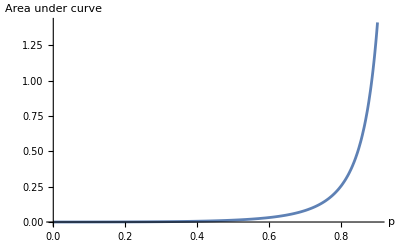

```mathematica
Plot[{-(73309 (-p/(2 Log[p]^2)-p/(2 Log[p])+LogIntegral[p]/2))/1930500},{p,0,0.9},PlotRange->All,AxesLabel->{"p","Area under curve"}]
```

### Calculate n exponent

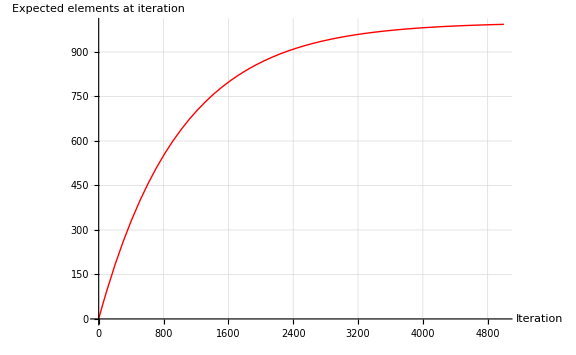

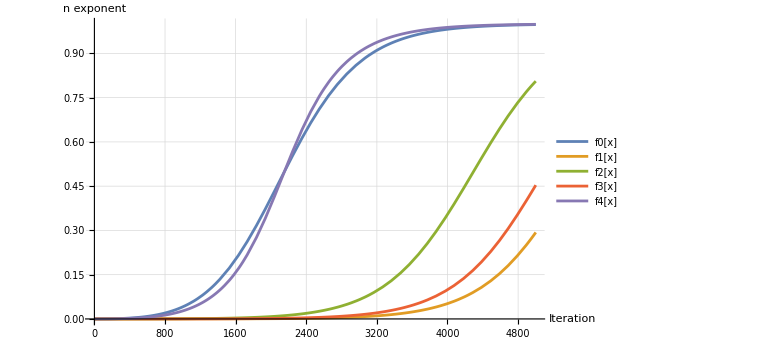

```mathematica
n=10;
b[x_]:=(n^3)*(1-(1-(1/n^3))^x);
g[x_]:=-(73309 (-x/(2 Log[x]^2)-x/(2 Log[x])+LogIntegral[x]/2))/1930500
nexp0[x_]:=1*(g[b[x]/n^3])/(g[b[x]/n^3]+1)
nexp1[x_]:=1*(g[b[x]/n^3])/(g[b[x]/n^3] +b[x])
nexp2[x_]:=1*(g[b[x]/n^3])/(g[b[x]/n^3] +b[x]/n)
nexp3[x_]:=1*(g[b[x]/n^3])/(g[b[x]/n^3] +b[x]/2)
nexp4[x_]:=2/Pi *ArcTan[g[b[x]/n^3]]
Plot[{b[x]},{x,0,5n^3},PlotRange->All, PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}},AxesLabel->{"Iteration","Expected elements at iteration"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}]
Plot[{nexp0[x], nexp1[x], nexp2[x], nexp3[x], nexp4[x]},{x,0, 5n^3 },PlotRange->All,AxesLabel->{"Iteration","n exponent"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}, PlotLegends->{"f0[x]","f1[x]","f2[x]","f3[x]","f4[x]"}]
```

### Calculate insertion complexity

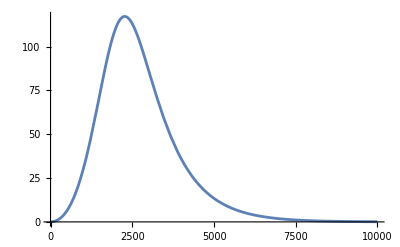

```mathematica
n=10;
ins2[x_]:=(1-b[x]/n^3)*2*n^ Nest[Power[((g[b[x]/n^3])/(g[b[x]/n^3]+1)),#]&,((g[b[x]/n^3])/(g[b[x]/n^3]+1)),n-1]
ins1[x_]:=(1-b[x]/n^3)*2*n^(3(g[b[x]/n^3])/(g[b[x]/n^3]+1))
ins[x_]:=(1-b[x]/n^3)*2*(n^3)*((g[b[x]/n^3])/(g[b[x]/n^3]+1))
Plot[{ins[x]},{x, 0, n^4}]
```

### Get the max point

```mathematica
n=10;
puntoEstab:=Module[{result},result=NMaximize[{ins[x], x>0},x];
xOptimal=x/. result[[2]];xOptimal]
puntoEstab
Plot[{puntoEstab},{n, 6, 50}]
(*Plot[{NIntegrate[ins[x], {x, 0, puntoEstab}]},{n, 2, 4}]*)
```

13.3418

-Graphics-

### Sum insertion complexity until the algorithm ends

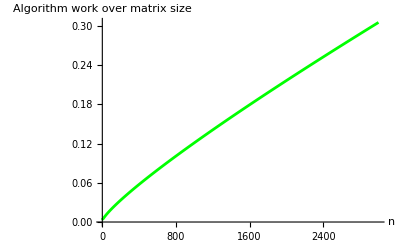

```mathematica
LaunchKernels[];
Clear[n];
points=ParallelTable[{n, NIntegrate[ins[x],{x,0,(n^0.5)*(HarmonicNumber[n^0.5])}, WorkingPrecision->10]},{n, 2, 3000}];
ListLinePlot[{points},PlotRange->All,AxesLabel->{"n","Algorithm work over matrix size"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
CloseKernels[];
```

### Fit the sum points

{-7.503107374,0.7840288489}

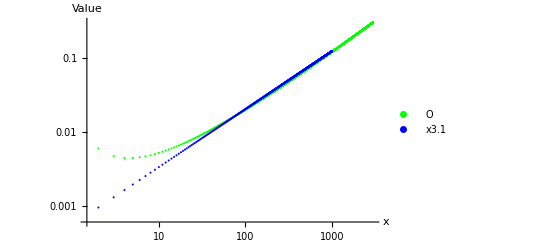

```mathematica
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x];
fittedLine=linearModel["Function"];
linearModel["BestFitParameters"]
ListLogLogPlot[{points, Table[{x,E^fittedLine[x]},{x,2,1000}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
```

FittedModel[…]

0.0003805980636 #1^0.8348014237&

| DF | SS | MS
Model | 2 | 104.042912 | 52.0214562
Error | 2997 | 0.00211727 | 7.06462×10^-7
Uncorrected Total | 2999 | 104.04503 | 
Corrected Total | 2998 | 21.330512 |

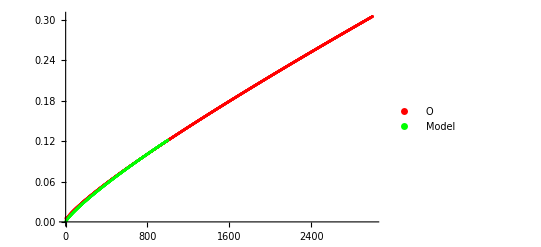

```mathematica
nonlinearModel=NonlinearModelFit[points,a*x^c ,{a,c},x]
nonlinearModel["Function"]
nonlinearModel["ANOVATable"]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,1000}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"O","Model"}],Right]]
```

### Distribution of iterations before process ends

10

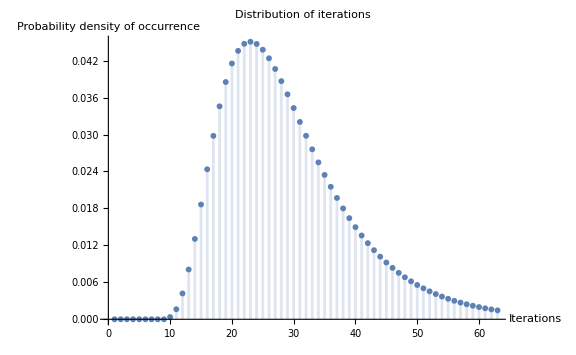

23

29.2897

```mathematica
n=10
distr[i_]:=(Factorial[n]/(n^i))*StirlingS2[i-1,n-1]
iValues=Range[1,2 n^1.5,1];
maxIndex=First@Ordering[Table[distr[i],{i,iValues}],-1];
DiscretePlot[distr[i],{i,iValues},AxesLabel->{"Iterations","Probability density of occurrence"},PlotLabel->"Distribution of iterations",PlotRange->Automatic,ImageSize->Large]
maxIndex
N[(n*Sum[1/j,{j,1,n}])]
```

## Combinatorics

### Simple cases😌

```mathematica
f[n_]:=Binomial[2n,2n-2]-n*Binomial[2n-2,0]
f1[n_]:=Binomial[2n,2n-3]-n*Binomial[2n-2,1]
f2[n_]:=Binomial[2n,2n-4]-n*(Binomial[2n-2,2])+Binomial[n,2]
f3[n_]:=Binomial[2n,2n-5]-n*(Binomial[2n-2,3])+Binomial[n,2]*Binomial[2n-4,1]
f4[n_]:=(4/45)(-5+n)(-4+n)(-3+n) (-2+n) (-1+n)n
f5[n_]:=(8/315)(-6+n)(-5+n)(-4+n)(-3+n) (-2+n) (-1+n)n
f6[n_]:=(2/315)(-7+n)(-6+n)(-5+n)(-4+n)(-3+n) (-2+n) (-1+n)n
{f[x],f1[x],f2[x],f3[x],f4[x],f5[x], f6[x]}//FunctionExpand//Factor
Table[{f6[i],f5[i],f4[i],f3[i],f2[i],f1[i], f[i], 2i, 1}, {i, 2, 10}]
```

{2 (-1+x) x,4/3 (-2+x) (-1+x) x,2/3 (-3+x) (-2+x) (-1+x) x,4/15 (-4+x) (-3+x) (-2+x) (-1+x) x,4/45 (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x,8/315 (-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x,2/315 (-7+x) (-6+x) (-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x}

{{0,0,0,0,0,0,4,4,1},{0,0,0,0,0,8,12,6,1},{0,0,0,0,16,32,24,8,1},{0,0,0,32,80,80,40,10,1},{0,0,64,192,240,160,60,12,1},{0,128,448,672,560,280,84,14,1},{256,1024,1792,1792,1120,448,112,16,1},{2304,4608,5376,4032,2016,672,144,18,1},{11520,15360,13440,8064,3360,960,180,20,1}}

### Closed form for 2 columns (m=2) case

```mathematica
Clear[n]
g[n_]:=Sum[Mod[Binomial[n,i],2],{i,0,n}]
g[n_]:=(2^n)/GCD[2^n,Factorial[n]]
d[n_]:=Factorial[n]/GCD[2^n,Factorial[n]]
f[n_,k_]:=(2^(2n-k)/Factorial[2n-k])*Sum[((StirlingS1[2n-k,i])*n^i),{i,0,2n-k}]
Table[f[10,x], {x,0,2*10}]
f[n,k]//FullSimplify
```

{0,0,0,0,0,0,0,0,0,0,1024,5120,11520,15360,13440,8064,3360,960,180,20,1}

(2^(-k+2 n) FactorialPower[n,-k+2 n])/((-k+2 n)!)

```mathematica
Clear[n]
b[x_]:=(2*n)*(1-(1-(1/(2*n)))^x)
p[k_,j_,n_,m_]:=StirlingS2[k,j]*Factorial[n*m]/(Factorial[(n*m)-j]*(n*m)^k)
ratio[n_,i_]:=Sum[p[i,j,n,2]*f[n,j]/Binomial[n*2,Min[j,2n]]//FullSimplify,{j,0,i}]
ratio2[n_,i_]:=Sum[p[i,j,n,2]*f[n,j]/Binomial[n*2,j]//FullSimplify,{j,0,Min[i,2n]}]
data=ParallelTable[Sum[1-ratio2[n,j],{j,0,n^2}],{n,1,30}];
data//N
(*ratio[n_,i_]:=(2^(-b[i]+2 n) FactorialPower[n,-b[i]+2 n])/((-b[i]+2 n)!)/Binomial[n*2,b[i]]//FullSimplify
D[ratio[n,k],k]//FullSimplify*)
```

{1.,2.875,5.344,8.21315,11.3412,14.6577,18.128,21.732,25.4555,29.2873,33.2176,37.2381,41.3415,45.5218,49.7734,54.0916,58.4724,62.9119,67.4071,71.9548,76.5525,81.1979,85.8887,90.623,95.399,100.215,105.069,109.961,114.888,119.85}

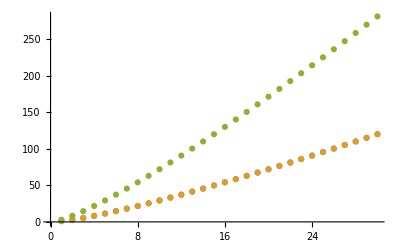

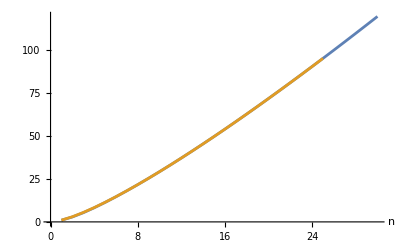

```mathematica
ListPlot[{Transpose[{Range[Length[data]],data}],Table[i*HarmonicNumber[i],{i,1,30}],Table[2i*HarmonicNumber[2i],{i,1,30}]}]
ListLinePlot[{Transpose[{Range[Length[data]],data}],Table[i*HarmonicNumber[i],{i,1,25}]},AxesLabel->{"n"}]
```

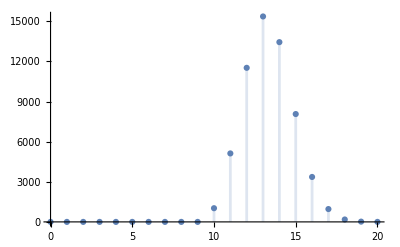

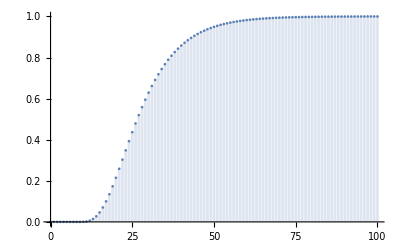

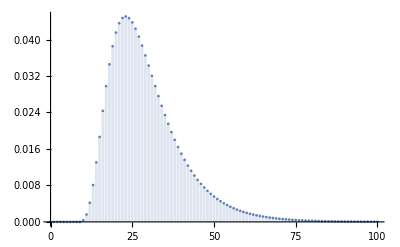

```mathematica
n=10;
DiscretePlot[f[n,k], {k, 0, 2n}, PlotRange->Full]
DiscretePlot[{ratio[n,k]},{k,0,10n}, PlotRange->Full,AxesLabel->{"Iteration"}]
DiscretePlot[{ratio[n,k]-ratio[n,k-1]},{k,0,10n}, PlotRange->Full,AxesLabel->{"Iteration"}]
Clear[n]
```

### m=5

```mathematica
f[n_]:=Binomial[5n,5n-2]
f1[n_]:=Binomial[5n,5n-3]
f2[n_]:=Binomial[5n,5n-4]
f3[n_]:=Binomial[5n,5n-5]-n*(Binomial[5n-5,0])
f4[n_]:=Binomial[5n,5n-6]-n*(Binomial[5n-5,1])-6(n-1)
f5[n_]:=Binomial[5n,5n-7]-n*(Binomial[5n-5,2])-2*(n-2)*(Binomial[3,2]+3)-2*(n-1)*((5n-8)+2(5n-7))-2*(n-1)
f6[n_]:=Binomial[5n,5n-8]-n*(Binomial[5n-5,3])
FactorTerms[FunctionExpand[{f[x],f1[x],f2[x],f3[x],f4[x], f5[x], f6[x]}]]
Table[{f6[i],f5[i],f4[i],f3[i],f2[i],f1[i], f[i], 5i, 1}, {i, 2, 10}]
```

{5/2 (-x+5 x^2),5/6 (2 x-15 x^2+25 x^3),5/24 (-6 x+55 x^2-150 x^3+125 x^4),125/24 (-2 x^2+7 x^3-10 x^4+5 x^5),1/144 (864-264 x+650 x^2-5625 x^3+10625 x^4-9375 x^5+3125 x^6),(-18144+46080 x-11340 x^2+28000 x^3-91875 x^4+109375 x^5-65625 x^6+15625 x^7)/1008,(25 (11088 x-26148 x^2+11060 x^3+27125 x^4-49000 x^5+40250 x^6-17500 x^7+3125 x^8))/8064}

{{25,82,194,250,210,120,45,10,1},{6075,6192,4963,3000,1365,455,105,15,1},{124150,76842,38682,15500,4845,1140,190,20,1},{1075875,479282,176976,53125,12650,2300,300,25,1},{5839125,2033262,593595,142500,27405,4060,435,30,1},{23507400,6720407,1622914,324625,52360,6545,595,35,1},{76852325,18637342,3838058,658000,91390,9880,780,40,1},{215464275,45370692,8144652,1221750,148995,14190,990,45,1},{536736750,99872082,15890196,2118750,230300,19600,1225,50,1}}

```mathematica
Table[{ Numerator[2^n/Factorial[n]], Denominator[5^n/Factorial[n]]},{n,0,10}]
```

{{1,1},{2,1},{2,2},{4,6},{2,24},{4,24},{4,144},{8,1008},{2,8064},{4,72576},{4,145152}}

### m=4

```mathematica
f[n_]:=Binomial[4n,4n-2]
f1[n_]:=Binomial[4n,4n-3]
f2[n_]:=Binomial[4n,4n-4]-n*(Binomial[4n-4,0])
f3[n_]:=Binomial[4n,4n-5]-n*(Binomial[4n-4,1])-4(n-1)
f4[n_]:=Binomial[4n,4n-6]-n*(Binomial[4n-4,2])-6*(n-2)-2*(n-1)*((n*4-7)+(n*4-6))
f5[n_]:=Binomial[4n,4n-7]-n*(Binomial[4n-4,3])
f6[n_]:=Binomial[4n,4n-8]-n*(Binomial[4n-4,4])+Binomial[n,2]
({f[x],f1[x],f2[x],f3[x],f4[x], f5[x], f6[x]}//FunctionExpand//FactorTerms)/.x->n
Table[{f6[i],f5[i],f4[i],f3[i],f2[i],f1[i], f[i], 4i, 1}, {i, 2, 10}]
```

{2 (-n+4 n^2),4/3 (n-6 n^2+8 n^3),2/3 (-3 n+11 n^2-24 n^3+16 n^4),4/15 (15+3 n-40 n^2+70 n^3-80 n^4+32 n^5),2/45 (-315+570 n+182 n^2-630 n^3+680 n^4-480 n^5+128 n^6),8/315 (810 n-2163 n^2+2387 n^3-1890 n^4+1400 n^5-672 n^6+128 n^7),2/315 (-5670 n+17643 n^2-22078 n^3+16009 n^4-9520 n^5+5152 n^6-1792 n^7+256 n^8)}

{{0,0,10,44,68,56,28,8,1},{288,624,790,760,492,220,66,12,1},{10896,10560,7618,4308,1816,560,120,16,1},{116880,74720,37926,15408,4840,1140,190,20,1},{706416,339264,133082,42364,10620,2024,276,24,1},{3033744,1169872,374262,98088,20468,3276,378,28,1},{10354528,3339648,902418,201124,35952,4960,496,32,1},{29936736,8303040,1942342,376672,58896,7140,630,36,1},{76315680,18572160,3830826,657612,91380,9880,780,40,1}}

{0,0,0,0,0,0,0,0,0,0,1024,1280,640,160,20,1}

(4^(4 n-4 n (1-4^-k n^-k (-1+4 n)^k)) Gamma[1+n] Gamma[1+4 n-4^(1-k) n^(1-k) (-1+4 n)^k])/(Gamma[1+4 n] Gamma[1+n-4^(1-k) n^(1-k) (-1+4 n)^k])

-(4^(-k+4^(1-k) n^(1-k) (-1+4 n)^k) n^-k (-1+4 n)^k Gamma[1+n] Gamma[1+4 n (1-4^-k n^-k (-1+4 n)^k)] (HarmonicNumber[n-4^(1-k) n^(1-k) (-1+4 n)^k]-HarmonicNumber[4 n (1-4^-k n^-k (-1+4 n)^k)]+Log[4]) (Log[4 n]-Log[-1+4 n]))/(Gamma[4 n] Gamma[1+n-4^(1-k) n^(1-k) (-1+4 n)^k])

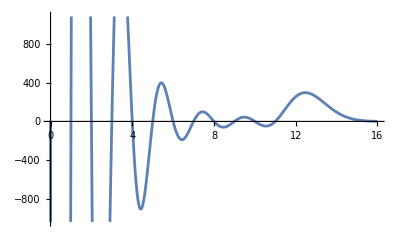

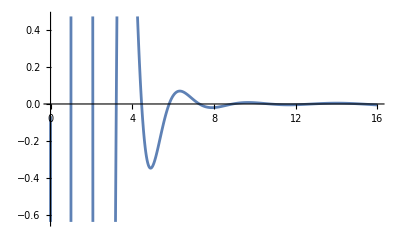

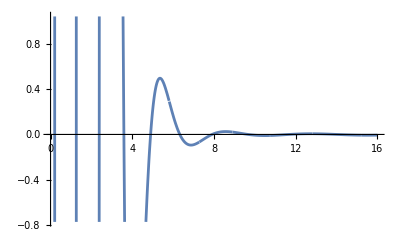

```mathematica
b[x_]:=(4*n)*(1-(1-(1/(4*n)))^x)
f[n_,k_]:=(4^k FactorialPower[n,k])/(k!)
Table[f[5,3*5-x], {x,0,3*5}]
ratio[n_,k_]:=f[n,(4*n)-b[k]]/Binomial[4*n,b[k]]
distr[n_,k_]:=D[ratio[n,x], x]/.x->k
Clear[n]
FactorTerms[FunctionExpand[ratio[n,k]]]
FullSimplify[FunctionExpand[distr[n,k]]]
n=4;
Plot[f[n,4n-k], {k, 0, n^2}]
Plot[ratio[n,k],{k,0,n^2}]
Plot[distr[n,k],{k,0,n^2}]
```

### m=3

```mathematica
f[n_]:=Binomial[3n,3n-2]
f1[n_]:=Binomial[3n,3n-3]-n*Binomial[3n-3,0]
f2[n_]:=Binomial[3n,3n-4]-n*(Binomial[3n-3,1])-2(n-1)
f3[n_]:=Binomial[3n,3n-5]-n*(Binomial[3n-3,2])-6 (n-2)*(n-1)-2(n-2)
f4[n_]:=Binomial[3n,3n-6]-n*(Binomial[3n-3,3])+Binomial[n,2]-20(n-2)
f5[n_]:=Binomial[3n,3n-7]-n*(Binomial[3n-3,4])
f6[n_]:=Binomial[3n,3n-8]-n*(Binomial[3n-3,5])
({f[x],f1[x],f2[x],f3[x],f4[x],f5[x], f6[x]}//FunctionExpand//ExpandAll//FactorTerms)/.x->n
Table[{f6[i],f5[i],f4[i],f3[i],f2[i],f1[i], f[i], 3i, 1}, {i, 2, 10}]
```

{3/2 (-n+3 n^2),9/2 (-n^2+n^3),1/8 (16+2 n+9 n^2-54 n^3+27 n^4),1/40 (-320+424 n+30 n^2+135 n^3-270 n^4+81 n^5),1/80 (3200-880 n-1566 n^2+765 n^3+405 n^4-405 n^5+81 n^6),3/560 (-2720 n+7392 n^2-6706 n^3+1575 n^4+945 n^5-567 n^6+81 n^7),(3 (30800 n-98460 n^2+118468 n^3-62013 n^4+7560 n^5+5670 n^6-2268 n^7+243 n^8))/4480}

{{0,0,0,0,7,18,15,6,1},{-9,-9,7,67,104,81,36,9,1},{-9,288,554,608,453,216,66,12,1},{2475,3960,3855,2595,1297,450,105,15,1},{25740,23634,15769,7810,2960,810,153,18,1},{143514,94860,48473,19088,5847,1323,210,21,1},{572679,298224,123864,40560,10444,2016,276,24,1},{1837539,792396,277690,77896,17318,2916,351,27,1},{5045625,1860300,564410,138548,27117,4050,435,30,1}}

{0,0,0,0,0,0,0,0,0,0,32,80,80,40,10,1}

(2^(3 n-3 n (1-3^-k n^-k (-1+3 n)^k)) Gamma[1+n] Gamma[1+3 n-3^(1-k) n^(1-k) (-1+3 n)^k])/(Gamma[1+3 n] Gamma[1+n-3^(1-k) n^(1-k) (-1+3 n)^k])

-(3^-k 8^((-1/3+n)^k n^(1-k)) n^-k (-1+3 n)^k Gamma[1+n] Gamma[1+3 n (1-3^-k n^-k (-1+3 n)^k)] (HarmonicNumber[n-3^(1-k) n^(1-k) (-1+3 n)^k]-HarmonicNumber[3 n (1-3^-k n^-k (-1+3 n)^k)]+Log[2]) (Log[3 n]-Log[-1+3 n]))/(Gamma[3 n] Gamma[1+n-3^(1-k) n^(1-k) (-1+3 n)^k])

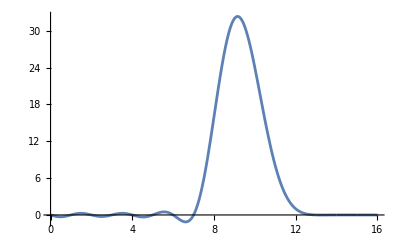

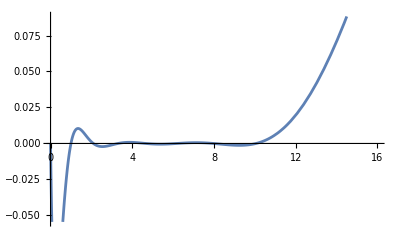

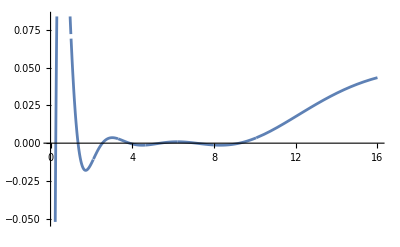

```mathematica
b[x_]:=(3*n)*(1-(1-(1/(3*n)))^x)
Table[f[5,3*5-x], {x,0,3*5}]
ratio[n_,k_]:=f[n,(3*n)-b[k]]/Binomial[3*n,b[k]]
distr[n_,k_]:=D[ratio[n,x], x]/.x->k
Clear[n]
FactorTerms[FunctionExpand[ratio[n,k]]]
FullSimplify[FunctionExpand[distr[n,k]]]
n=4;
Plot[f[n,3n-k], {k, 0, n^2}]
Plot[ratio[n,k],{k,0,n^2}]
Plot[distr[n,k],{k,0,n^2}]
```

```mathematica
Table[{FactorTerms[FunctionExpand[Binomial[x n,x n-x+1]]],FactorTerms[FunctionExpand[Binomial[x n,x n-x]-n]]}, {x, 0, 9}]
```

{{0,1-n},{1,0},{2 n,2 (-n+n^2)},{3/2 (-n+3 n^2),9/2 (-n^2+n^3)},{4/3 (n-6 n^2+8 n^3),2/3 (-3 n+11 n^2-24 n^3+16 n^4)},{5/24 (-6 n+55 n^2-150 n^3+125 n^4),125/24 (-2 n^2+7 n^3-10 n^4+5 n^5)},{3/5 (2 n-25 n^2+105 n^3-180 n^4+108 n^5),1/10 (-20 n+137 n^2-675 n^3+1530 n^4-1620 n^5+648 n^6)},{7/720 (-120 n+1918 n^2-11025 n^3+29155 n^4-36015 n^5+16807 n^6),343/720 (-36 n^2+232 n^3-735 n^4+1225 n^5-1029 n^6+343 n^7)},{8/315 (45 n-882 n^2+6496 n^3-23520 n^4+44800 n^5-43008 n^6+16384 n^7),2/315 (-315 n+3267 n^2-26264 n^3+108304 n^4-250880 n^5+329728 n^6-229376 n^7+65536 n^8)},{(9 (-560 n+13068 n^2-118188 n^3+548289 n^4-1428840 n^5+2112642 n^6-1653372 n^7+531441 n^8))/4480,(9 (-12176 n^2+118124 n^3-605556 n^4+1818369 n^5-3306744 n^6+3582306 n^7-2125764 n^8+531441 n^9))/4480}}

### Square case

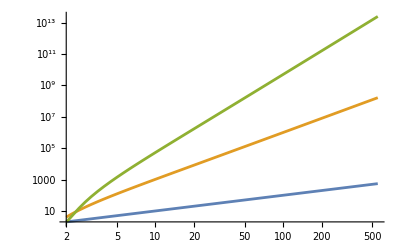

4-6 x+x^2+x^3

-22+33 x-(13 x^2)/2-6 x^3+x^4+x^5/2

```mathematica
l[n_]:=n*Binomial[n^2-n,1]+2*(n-1)*(n-2)
l1[n_]:=n*Binomial[n^2-n,2]+2*(n-2)*(Binomial[n-2,2]+n-2)+2*(n-1)*((n^2-n-3)+(n-3)*(n^2-n-2))+2*(n-1)*Binomial[n-3,2]
LogLogPlot[{n, l[n], l1[n]} ,{n, 2, 550}, PlotRange->Full]
Simplify[l[x]]
Simplify[l1[x]]
```

```mathematica
Simplify[InterpolatingPolynomial[{{6,1966832},{7,13480033},{8,66764072},{9,264081073},{10,884650000},{11,2606370707},{12,6930353940},{13,16942788625},{14,38611859216},{15,82900565717},{16,169083207472},{17,329788111817},{18,618456395728},{19,1120110950839},{20,1966576580444},{21,3357586764777},{22,5589560694064}}, x]]
```

1/120 (779520-1066792 x+327244 x^2+100814 x^3-56635 x^4-5153 x^5+4516 x^6+360 x^7-210 x^8-30 x^9+5 x^10+x^11)

```mathematica
poly1[x_]:=4-6 x+x^2+x^3
poly2[x_]:=1/2 (-44+66 x-13 x^2-12 x^3+2 x^4+x^5)
poly3[x_]:=1/6 (888-1268 x+338 x^2+169 x^3-53 x^4-18 x^5+3 x^6+x^7)
poly4[x_]:=1/24 (-23616+32884 x-9568 x^2-3619 x^3+1666 x^4+278 x^5-118 x^6-24 x^7+4 x^8+x^9)
poly5[x_]:=1/120 (779520-1066792 x+327244 x^2+100814 x^3-56635 x^4-5153 x^5+4516 x^6+360 x^7-210 x^8-30 x^9+5 x^10+x^11)
n=4;
poly1[n]
poly2[n]
poly3[n]
poly4[n]
poly5[n]
Print[Roots[poly1[x]==x, x]]
```

60

390

1452

3422

5260

x==1/3 (-1+22/(1/2 (-173+3 ⅈ √1407))^(1/3)+(1/2 (-173+3 ⅈ √1407))^(1/3))||x==-1/3-(11 (1+ⅈ √3))/(3 (1/2 (-173+3 ⅈ √1407))^(1/3))-1/6 (1-ⅈ √3) (1/2 (-173+3 ⅈ √1407))^(1/3)||x==-1/3-(11 (1-ⅈ √3))/(3 (1/2 (-173+3 ⅈ √1407))^(1/3))-1/6 (1+ⅈ √3) (1/2 (-173+3 ⅈ √1407))^(1/3)

```mathematica
Print[Roots[poly1[x]==0,x]]
Print[Simplify[Roots[poly2[x]==0,x]]]
```

x==-1-√5||x==-1+√5||x==1

3/4+1/2 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))+1/2 √(33/2-(7578+ⅈ √969243)^(1/3)/3^(2/3)-269/(22734+3 ⅈ √969243)^(1/3)-41/(4 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))))+x==0||3/4+1/2 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))+x==1/2 √(33/2-(7578+ⅈ √969243)^(1/3)/3^(2/3)-269/(22734+3 ⅈ √969243)^(1/3)-41/(4 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))))||3/4+1/2 √(33/2-(7578+ⅈ √969243)^(1/3)/3^(2/3)-269/(22734+3 ⅈ √969243)^(1/3)+41/(4 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))))+x==1/2 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))||x==-3/4+1/2 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))+1/2 √(33/2-(7578+ⅈ √969243)^(1/3)/3^(2/3)-269/(22734+3 ⅈ √969243)^(1/3)+41/(4 √(33/4+(7578+ⅈ √969243)^(1/3)/3^(2/3)+269/(22734+3 ⅈ √969243)^(1/3))))||x==1

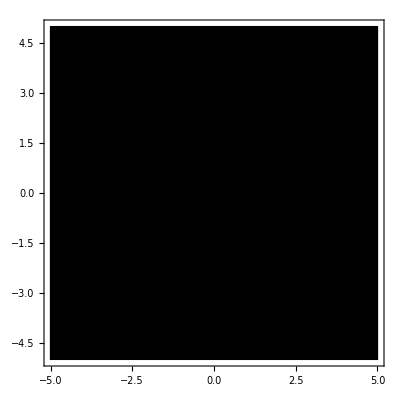

-Graphics3D-

```mathematica
ComplexPlot[poly2[x],{x,-5-5 I,5+5I},PlotLegends->Automatic]
f[x_, y_]:=-22+33 (x+y*I)-(13 (x+y*I)^2/2)-6 (x+y*I)^3+(x+y*I)^4+((x+y*I)^5/2)
xmin=-5;
xmax=5;
ymin=-5;
ymax=5;
Show[Plot3D[Re@f[x,y],{x,xmin,xmax},{y,ymin,ymax},AxesLabel->{"Re(x)","Im(x)","Re(f(x))"},ColorFunction->Function[{x,y,z},ColorData[{"Rainbow","Reversed"}][Im@f[x,y]]]],Graphics3D[{Gray,Thick,Table[InfiniteLine[{{xmin,y,0},{xmax,y,0}}],{y,ymin,ymax,1/2}],Table[InfiniteLine[{{x,ymin,0},{x,ymax,0}}],{x,xmin,xmax,1}]}]]
```

### Interpolating Direct Formula

```mathematica
Clear[n]
m[n_]:=Sum[Binomial[n,2*k]*CatalanNumber[k], {k, 0, n/2}]
elem[n_]:=(n+2) 3^(n-2)+2 Sum[m[k]*(n-k-2) 3^(n-k-3),{k,0,n-2}]
elem[n_]:=(n+2) 3^(n-2)+2 Sum[(Hypergeometric2F1[1/2-k/2,-k/2,2,4])*(n-k-2) 3^(n-k-3),{k,0,n-2}]
Table[elem[i], {i, 0, 20}]
Simplify[elem[x]]
```

{2/9,1,4,17,68,259,950,3387,11814,40503,136946,457795,1515926,4979777,16246924,52694573,170028792,546148863,1747255194,5569898331,17698806798}

3^(-2+x) (2+x)+2 ∑_(k=0)^(-2+x) 3^(-3-k+x) (-2-k+x) Hypergeometric2F1[1/2-k/2,-k/2,2,4]

```mathematica
poly1[x_]:=FactorTerms[FullSimplify[InterpolatingPolynomial[{{0,1},{1,4},{2,6},{3,4},{4,1}}, x]]]
poly2[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,1},{1,9},{2,36},{3,84},{4,126},{5,126},{6,84},{7,36},{8,9},{9,1}}, x]]]
poly3[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,1},{1,16},{2,120},{3,560},{4,1820},{5,4368},{6,8008},{7,11440},{8,12870},{9,11440},{10,8008},{11,4368},{12,1820},{13,560},{14,120},{15,16},{16,1}}, x]]]
poly4[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,1},{1,25},{2,300},{3,2300},{4,12650},{5,53130},{6,177100},{7,480700},{8,1081575},{9,2042975},{10,3268760},{11,4457400},{12,5200300},{13,5200300},{14,4457400},{15,3268760},{16,2042975},{17,1081575},{18,480700},{19,177100},{20,53130},{21,12650},{22,2300},{23,300},{24,25},{25,1}}, x]]]
poly5[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,1},{1,36},{2,630},{3,7140},{4,58905},{5,376992},{6,1947792},{7,8347680},{8,30260340},{9,94143280},{10,254186856},{11,600805296},{12,1251677700},{13,2310789600},{14,3796297200},{15,5567902560},{16,7307872110},{17,8597496600},{18,9075135300},{19,8597496600},{20,7307872110},{21,5567902560},{22,3796297200},{23,2310789600},{24,1251677700},{25,600805296},{26,254186856},{27,94143280},{28,30260340},{29,8347680},{30,1947792},{31,376992},{32,58905},{33,7140},{34,630},{35,36},{36,1}}, x]]]
poly1[x]
poly2[x]
poly3[x]
poly4[x]
poly5[x]
```

1/4 (4+4 x+15 x^2-8 x^3+x^4)

1/576 (576-7200 x+25100 x^2-22896 x^3+12693 x^4-3564 x^5+510 x^6-36 x^7+x^8)

1/1625702400(1625702400-1215804764160 x+4156695500544 x^2-6061215760896 x^3+5146370947600 x^4-2852007127424 x^5+1104533026184 x^6-309384000576 x^7+64033982161 x^8-9881106112 x^9+1135470460 x^10-96308800 x^11+5926438 x^12-256704 x^13+7412 x^14-128 x^15+x^16)

1/229442532802560000(229442532802560000-49549463099136000000000 x+185296978050262640640000 x^2-306656837992151776051200 x^3+302874454586535835521024 x^4-202243666541959310400000 x^5+97807860068320702872000 x^6-35767222316850064128000 x^7+10181390704210694391280 x^8-2302031871607693500000 x^9+419351157265086260500 x^10-62155289998119846000 x^11+7543746779210668765 x^12-752356243395262500 x^13+61713022317495250 x^14-4156722759469500 x^15+228939340164535 x^16-10236802125000 x^17+367557190000 x^18-10427505000 x^19+228194395 x^20-3712500 x^21+42250 x^22-300 x^23+x^24)

1/40990389067797283140009984000000(40990389067797283140009984000000-10038408561951060713763439523974348800000 x+41937668046233737239110485333612953600000 x^2-79466028639131817234996864583433453568000 x^3+92024493727071140758591850231315752550400 x^4-73795972586728928237785422871735810129920 x^5+43932858607135499690812052763547198193664 x^6-20298907317417991909985982090579135676416 x^7+7506561884655687701151528855439975203840 x^8-2272154554894085017298170130495462022144 x^9+572566498730108536619663232495329864448 x^10-121704347422851382069429466134698642432 x^11+22047686088523681106368743373991414656 x^12-3432067679089062266610129868778656896 x^13+462077288484148304824264246420613088 x^14-54084969433899046932514612603604352 x^15+5525634413379184864400672424761844 x^16-494245481990344474519935227496060 x^17+38787148723854282062093595024575 x^18-2674216463186568375974545122600 x^19+162074669092436483306325518265 x^20-8633032478815161732709248720 x^21+403765063220373408465346620 x^22-16551899579578258399106880 x^23+593160803872274275661580 x^24-18514661256329823248040 x^25+500924382152462098146 x^26-11673440702300955024 x^27+232402792962725550 x^28-3910841504246736 x^29+54849451057772 x^30-629047323648 x^31+5744163864 x^32-40151484 x^33+201687 x^34-648 x^35+x^36)

```mathematica
Table[(n+2)*3^(n-2)+2*Sum[ResourceFunction["MotzkinM"][k]*(n-k-2)*3^(n-k-3),{k,0,n-3}],{n,0,10}]
```

{2/9,1,4,17,68,259,950,3387,11814,40503,136946}

```mathematica
poly1[x_]:=FactorTerms[FullSimplify[InterpolatingPolynomial[{{2,4},{3,22},{4,60},{5,124},{6,220},{7,354},{8,532},{9,760},{10,1044}}, x]]]
poly2[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{3,59},{4,390},{5,1418},{6,3830},{7,8637},{8,17234},{9,31460},{10,53658},{11,86735},{12,134222},{13,200334},{14,290030},{15,409073}}, x]]]
poly3[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{4,1452},{5,9958},{6,42200},{7,135542},{8,362596},{9,851122},{10,1810168},{11,3563290},{12,6589692},{13,11574126},{14,19466392},{15,31551278},{16,49529780},{17,75612442},{18,112625656}}, x]]]
poly4[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{5,48171},{6,330862},{7,1538918},{8,5573732},{9,16929642},{10,45091226},{11,108423937},{12,240160778},{13,497230517},{14,972830862},{15,1813823056},{16,3244212512},{17,5596183388},{18,9350373402}}, x]]]
poly5[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{6,1966832},{7,13480033},{8,66764072},{9,264081073},{10,884650000},{11,2606370707},{12,6930353940},{13,16942788625},{14,38611859216},{15,82900565717},{16,169083207472},{17,329788111817},{18,618456395728},{19,1120110950839},{20,1966576580444}}, x]]]
poly6[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{7,94850847},{8,649054448},{9,3364850969},{10,14238839294},{11,51559124726},{12,164948309254},{13,476972080825},{14,1267825309002},{15,3137826256285},{16,7304063280756},{17,16119344733941},{18,33947126684342},{19,68589703621580},{20,133553982453866}}, x]]]
poly1[x]
poly2[x]
poly3[x]
poly4[x]
poly5[x]
poly6[x]
```

4-6 x+x^2+x^3

1/2 (-44+66 x-13 x^2-12 x^3+2 x^4+x^5)

1/6 (888-1268 x+338 x^2+169 x^3-53 x^4-18 x^5+3 x^6+x^7)

1/24 (-23616+32884 x-9568 x^2-3619 x^3+1666 x^4+278 x^5-118 x^6-24 x^7+4 x^8+x^9)

1/120 (779520-1066792 x+327244 x^2+100814 x^3-56635 x^4-5153 x^5+4516 x^6+360 x^7-210 x^8-30 x^9+5 x^10+x^11)

1/720 (-30864960+41562504 x-13236764 x^2-3430222 x^3+2228043 x^4+97030 x^5-178480 x^6-1977 x^7+9526 x^8+380 x^9-331 x^10-36 x^11+6 x^12+x^13)

```mathematica
poly1[x_]:=FactorTerms[FullSimplify[InterpolatingPolynomial[{{0,0},{1,0},{2,4},{3,4},{4,1}}, x]]]
poly2[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,0},{1,0},{2,0},{3,17},{4,67},{5,104},{6,81},{7,36},{8,9},{9,1}}, x]]]
poly3[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,0},{1,0},{2,0},{3,0},{4,68},{5,632},{6,2594},{7,6168},{8,9454},{9,9988},{10,7618},{11,4308},{12,1816},{13,560},{14,120},{15,16},{16,1}}, x]]]
poly4[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,0},{1,0},{2,0},{3,0},{4,0},{5,259},{6,4351},{7,34162},{8,165932},{9,556667},{10,1365401},{11,2539513},{12,3682167},{13,4258223},{14,4001349},{15,3098369},{16,1994804},{17,1071617},{18,479282},{19,176976},{20,53125},{21,12650},{22,2300},{23,300},{24,25},{25,1}}, x]]]
poly5[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,950},{7,25060},{8,317102},{9,2558560},{10,14759358},{11,64695152},{12,223592503},{13,624333880},{14,1433343382},{15,2743128692},{16,4428324603},{17,6094699408},{18,7220615444},{19,7426840428},{20,6679532216},{21,5282175608},{22,3686867960},{23,2275803032},{24,1242457649},{25,598838464},{26,253855994},{27,94101080},{28,30256510},{29,8347460},{30,1947786},{31,376992},{32,58905},{33,7140},{34,630},{35,36},{36,1}}, x]]]
poly6[x_]:=FactorTerms[Simplify[InterpolatingPolynomial[{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,3387},{8,128693},{9,2377482},{10,28434398},{11,247304673},{12,1665689983},{13,9034023196},{14,40503284385},{15,152928024312},{16,492946015433},{17,1370692115205},{18,3315050727995},{19,7021671641024},{20,13104689757689},{21,21671059353450},{22,31923016349386},{23,42100944784088},{24,49946796374587},{25,53535734771579},{26,52044487014141},{27,46037853669399},{28,37152428803395},{29,27403160933677},{30,18494458412338},{31,11425387152800},{32,6458436822347},{33,3336822747362},{34,1572883373359},{35,674697753312},{36,262501932917},{37,92250254803},{38,29134377346},{39,8217686994},{40,2054446997},{41,450977712},{42,85900577},{43,13983816},{44,1906884},{45,211876},{46,18424},{47,1176},{48,49},{49,1}}, x]]]
(poly1[x]//Factor )/.x->j
(poly2[x]//Factor )/.x->j
(poly3[x]//Factor )/.x->j
(poly4[x]//Factor )/.x->j
(poly5[x]//Factor )/.x->j
```

1/24 (-1+j) j (166-77 j+9 j^2)

((-2+j) (-1+j) j (4976712-8174754 j+5373667 j^2-1600455 j^3+238231 j^4-17439 j^5+502 j^6))/362880

1/20922789888000(-3+j) (-2+j) (-1+j) j (56081761542374400-85085055651807360 j+57718955600437248 j^2-23122383262921016 j^3+6086351765594596 j^4-1108162925321890 j^5+143158771337939 j^6-13239411901518 j^7+871585458963 j^8-39917890750 j^9+1209768113 j^10-21824666 j^11+177541 j^12)

-1/15511210043330985984000000(-4+j) (-3+j) (-2+j) (-1+j) j (12429486589866827953378959360000-20902625886472843169651581440000 j+16429329399816634773156880320000 j^2-8025471623370468011596662124800 j^3+2732672840495306733962828646624 j^4-689485138024417797453152816400 j^5+133769282028212340103249556240 j^6-20438571526511957823031210840 j^7+2498274899122664683934183454 j^8-246787354235949490831245225 j^9+19817056981683686939996430 j^10-1296445850407086440549055 j^11+69014163184432481319044 j^12-2974880720837948301850 j^13+102882729981282627420 j^14-2812425200835749670 j^15+59379676368912054 j^16-933743872506525 j^17+10293409339910 j^18-70964375635 j^19+230218824 j^20)

-1/92998331697475304366999862037708800000000(-5+j) (-4+j) (-3+j) (-2+j) (-1+j) j (122253453787753844232180844935398125343499878400000-226884636387638342695932955089329196963242311680000 j+201056468956131205509704706764712961604702306304000 j^2-113317616593925186838399911360520712841555508019200 j^3+45647201399931343026308433774407221046729751736320 j^4-14001404787792699517272324343024463775825929886720 j^5+3401930311786260859766261770607707401460347481344 j^6-672487510398053355744919580022022427140320721920 j^7+110234782019167529313607797979327158824347774080 j^8-15195619265353563306075533606729894833757755200 j^9+1780142451303864199928126640082983799851191936 j^10-178642233024767788782814264218019975010151600 j^11+15449152370764523937039467233842076596928600 j^12-1156439550869065268136220419364442046188400 j^13+75155816989699808554841038589859867335835 j^14-4248465014757349895717828507168346041025 j^15+209055441476199394104512476879716010275 j^16-8951880547962401663439197938170095625 j^17+333099803678353110373110586454492295 j^18-10742566201280887608959580733735125 j^19+299085338216923159356501407286975 j^20-7148581796546499803248674074925 j^21+145580678133504573842174319585 j^22-2500624957826414289630125475 j^23+35738250513266948510342505 j^24-417111167101760948003355 j^25+3872187703281568314861 j^26-27494728441444205655 j^27+140211417108521245 j^28-457132145315775 j^29+715617560144 j^30)

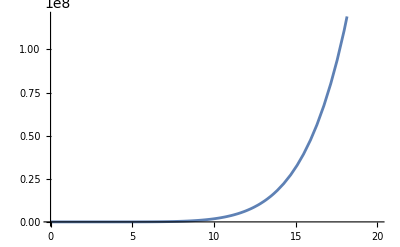

```mathematica
Plot[{ poly3[x]}, {x, 0, 20}, PlotRange->Automatic]
```

```mathematica
p[n_,x_]:=Product[-x+k, {k, 0, n}]/(n!) Sum[(Binomial[n,k]^2 )*(-1)^(k-1)/(x-k),{k,0,n}]
FullSimplify[p[n,x]]
```

(HypergeometricPFQ[{-n,-n,-x},{1,1-x},-1] Pochhammer[1-x,n])/(n!)

```mathematica
p[n_,x_]:=(HypergeometricPFQ[{-n,-n,-x},{1,1-x},-1] Pochhammer[1-x,n])/(n!)
Clear[n]
FactorTerms[Simplify[p[n^2, x]-poly1[n]]]/.x->(n^2 -n-1)
FactorTerms[Simplify[p[2^2, x]]]
FactorTerms[Simplify[p[10, x]]]
```

(HypergeometricPFQ[{-n^2,-n^2,1+n-n^2},{1,2+n-n^2},-1] Pochhammer[2+n-n^2,n^2])/(n^2!)-poly1[n]

1/4 (4+4 x+15 x^2-8 x^3+x^4)

(14400+365760 x-912076 x^2+1198100 x^3-765655 x^4+310690 x^5-78023 x^6+11800 x^7-1045 x^8+50 x^9-x^10)/14400

```mathematica
n=3;
Table[StirlingS2[i,2], {i, 0, 2n}]
```

{0,0,1,3,7,15,31}

```mathematica
poly1[x]
poly2[x]
gcd[x_]:=FactorTerms[PolynomialGCD[poly1[x],poly2[x]]]
gcd1[x_]:=FactorTerms[PolynomialGCD[poly2[x],poly3[x]]]
gcd2[x_]:=FactorTerms[PolynomialGCD[poly3[x],poly4[x]]]
gcd3[x_]:=FactorTerms[PolynomialGCD[poly4[x],poly5[x]]]
gcd[x]
gcd1[x]
gcd2[x]
gcd3[x]
FactorTerms[PolynomialQuotientRemainder[poly2[x], gcd1[x],x]]
hankelMatrix=HankelMatrix[CoefficientList[poly3[x]*Factorial[16],x]];
Det[hankelMatrix]
N[Det[hankelMatrix],300]
Column[{poly2[x],hankelMatrix}]
```

1/24 (-166 x+243 x^2-86 x^3+9 x^4)

(9953424 x-31279644 x^2+40248308 x^3-27496665 x^4+10651494 x^5-2350026 x^6+291552 x^7-18945 x^8+502 x^9)/362880

(-x+x^2)/362880

(2 x-3 x^2+x^3)/20922789888000

(-6 x+11 x^2-6 x^3+x^4)/15511210043330985984000000

(24 x-50 x^2+35 x^3-10 x^4+x^5)/92998331697475304366999862037708800000000

{57657600 (4976712-8174754 x+5373667 x^2-1600455 x^3+238231 x^4-17439 x^5+502 x^6),0}

173012407382029760617554072697399345677072355493617442257190258548097465688385708547955781

1.73012407382029760617554072697399345677072355493617442257190258548097465688385708547955781×10^89

(9953424 x-31279644 x^2+40248308 x^3-27496665 x^4+10651494 x^5-2350026 x^6+291552 x^7-18945 x^8+502 x^9)/362880
{{0,-336490569254246400,1127409710876962560,-1618739915026750848,1340234906635554384,-722263115740129600,270052102151435240,-72689238663057016,14389512273652373,-2117978597020000,232422190140140,-18915280062224,1124531200702,-47417636000,1342669060,-22889912,177541},{-336490569254246400,1127409710876962560,-1618739915026750848,1340234906635554384,-722263115740129600,270052102151435240,-72689238663057016,14389512273652373,-2117978597020000,232422190140140,-18915280062224,1124531200702,-47417636000,1342669060,-22889912,177541,0},{1127409710876962560,-1618739915026750848,1340234906635554384,-722263115740129600,270052102151435240,-72689238663057016,14389512273652373,-2117978597020000,232422190140140,-18915280062224,1124531200702,-47417636000,1342669060,-22889912,177541,0,0},{-1618739915026750848,1340234906635554384,-722263115740129600,270052102151435240,-72689238663057016,14389512273652373,-2117978597020000,232422190140140,-18915280062224,1124531200702,-47417636000,1342669060,-22889912,177541,0,0,0},{1340234906635554384,-722263115740129600,270052102151435240,-72689238663057016,14389512273652373,-2117978597020000,232422190140140,-18915280062224,1124531200702,-47417636000,1342669060,-22889912,177541,0,0,0,0},{-722263115740129600,270052102151435240,-72689238663057016,14389512273652373,-2117978597020000,232422190140140,-18915280062224,1124531200702,-47417636000,1342669060,-22889912,177541,0,0,0,0,0},{270052102151435240,-72689238663057016,14389512273652373,-2117978597020000,232422190140140,-18915280062224,1124531200702,-47417636000,1342669060,-22889912,177541,0,0,0,0,0,0},{-72689238663057016,14389512273652373,-2117978597020000,232422190140140,-18915280062224,1124531200702,-47417636000,1342669060,-22889912,177541,0,0,0,0,0,0,0},{14389512273652373,-2117978597020000,232422190140140,-18915280062224,1124531200702,-47417636000,1342669060,-22889912,177541,0,0,0,0,0,0,0,0},{-2117978597020000,232422190140140,-18915280062224,1124531200702,-47417636000,1342669060,-22889912,177541,0,0,0,0,0,0,0,0,0},{232422190140140,-18915280062224,1124531200702,-47417636000,1342669060,-22889912,177541,0,0,0,0,0,0,0,0,0,0},{-18915280062224,1124531200702,-47417636000,1342669060,-22889912,177541,0,0,0,0,0,0,0,0,0,0,0},{1124531200702,-47417636000,1342669060,-22889912,177541,0,0,0,0,0,0,0,0,0,0,0,0},{-47417636000,1342669060,-22889912,177541,0,0,0,0,0,0,0,0,0,0,0,0,0},{1342669060,-22889912,177541,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-22889912,177541,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{177541,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
{remainder,coeffs}=PolynomialReduce[poly2[x],{poly1[x], gcd[x], gcd1[x]},x];
If[remainder===0,Print["The target polynomial can be formed with the set of polynomials."];
Print["Coefficients: ",coeffs],Print["The target polynomial cannot be formed with the set of polynomials."]]
```

The target polynomial cannot be formed with the set of polynomials.

```mathematica
GroebnerBasis[{ poly3[x], poly4[x]},x]
```

{-6 x+11 x^2-6 x^3+x^4}

### Get distribution from polynomials😣

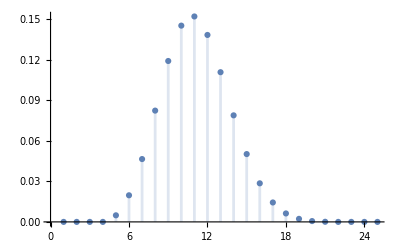

```mathematica
distr1[x_]:=poly4[x]/Binomial[Exponent[poly4[k],k],x]
DiscretePlot[distr1[x]-distr1[x-1], {x, 0, Exponent[poly4[k],k], 1}]
```

### Normal distribution for final number of elements

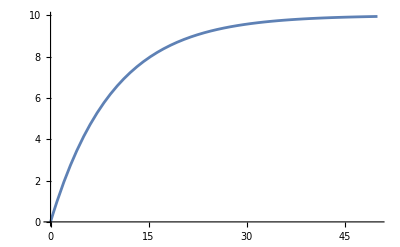

```mathematica
n=5;
b[x_]:=(2*n)*(1-(1-(1/(2*n)))^x)
Plot[b[x], {x,0,50}]
```

## Ratio

```mathematica
n=19
b[x_]:=(n^2)*(1-(1-(1/n^2))^x);
Plot[Binomial[n^2, b[x]], {x, 0, n^2}, PlotRange->Full]
```

19

-Graphics-

```mathematica
b[x_]:=1-(1-(1-(1/n^2))^x);
```

10

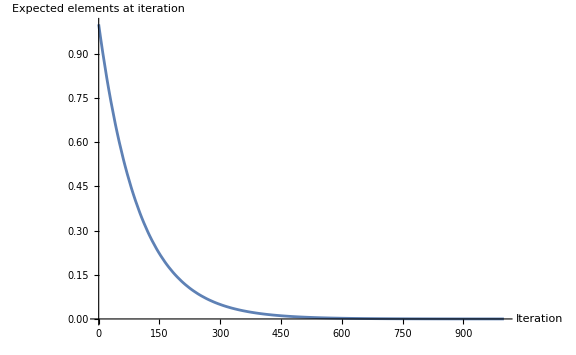

```mathematica
n=10
Plot[{b[x]},{x,0,10n^2},PlotRange->All,AxesLabel->{"Iteration","Expected elements at iteration"},ImageSize->Large]
```

```mathematica
Clear[n]
Integrate[b[x], {x, 0, q}]
D[b[x], x]
```

(-1+(1-1/n^2)^(x/10))/Log[1-1/n^2]

(1-1/n^2)^x Log[1-1/n^2]

```mathematica
area[x_]:=n^2 (x-(-1+(1-1/n^2)^x)/Log[1-1/n^2])
```

```mathematica
n=30
k=n^3
N[area[k]/(k*b[k])]
```

30

27000

0.966685

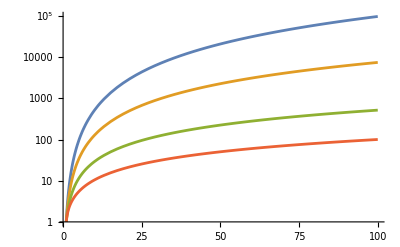

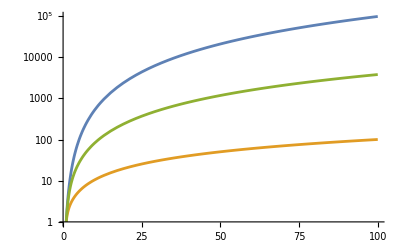

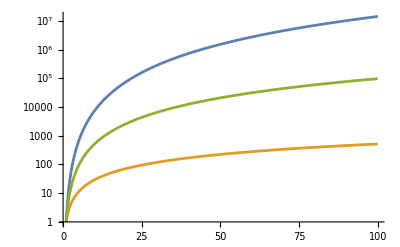

```mathematica
LogPlot[{(n^2)*HarmonicNumber[n^2],(n^1.5)*HarmonicNumber[n^1.5],(n)*HarmonicNumber[n],(n^2)*(HarmonicNumber[n^2]-HarmonicNumber[(n^2)-n])},{n,1,100}]
LogPlot[{(n^2)*(HarmonicNumber[n^2]-HarmonicNumber[(n^2)-n^2]),(n^2)*(HarmonicNumber[n^2]-HarmonicNumber[(n^2)-n]),(n^2)*(HarmonicNumber[n^2]-HarmonicNumber[(n^2)-((n^1.75))])},{n,1,100}]
LogPlot[{(n^3)*HarmonicNumber[n^3],(n)*HarmonicNumber[n],(n^2)*HarmonicNumber[n^2]},{n,1,100}]
```

```mathematica
Limit[(n^1.5)*(HarmonicNumber[n^1.5])/((n^2)*(HarmonicNumber[n^2]-HarmonicNumber[(n^2)-n^1.5])),n->Infinity]
```

$Aborted

## Proofs

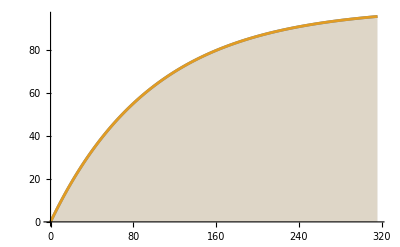

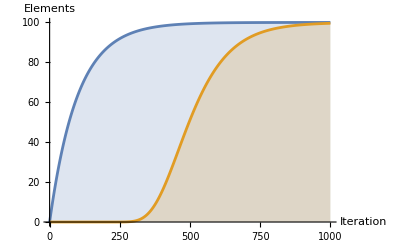

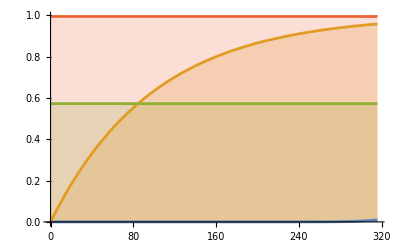

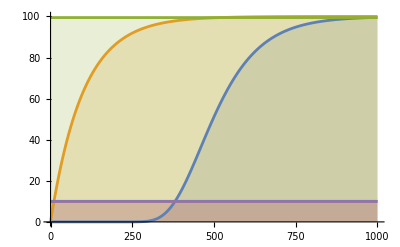

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

General::stop: Further output of InverseFunction::ifun will be suppressed during this calculation.

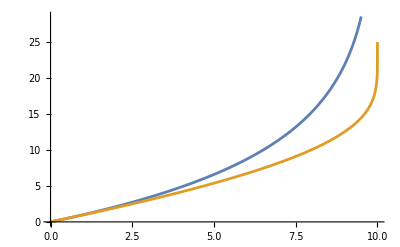

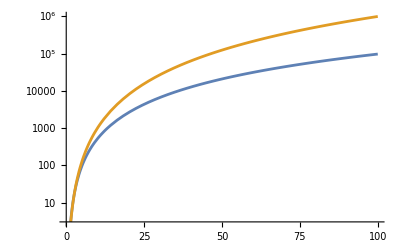

```mathematica
b1D[x_]:=n(1-(1-(1/n))^x);
b2D[x_]:=(n^2)*(1-(1-(1/n^2))^x);
b3D[x_]:=(n^3)*(1-(1-(1/n^3))^x);
p[k_,j_,n_,m_]:=StirlingS2[k,j]*Factorial[n*m]/(Factorial[(n*m)-j]*(n*m)^k)
n=10;
DiscretePlot[{Sum[y*p[x,y,n,n],{y,0,x}],b2D[x]},{x,0,10n^1.5}]
DiscretePlot[{b2D[x],p[x,n^2,n,n]*n^2},{x,0,10n^2},AxesLabel->{"Iteration","Elements"}]
DiscretePlot[{p[x,n^2,n,n],b2D[x]/n^2,p[(n^2)*HarmonicNumber[n^2]//Floor,n^2,n,n],b2D[(n^2)*HarmonicNumber[n^2]]/n^2},{x,0,10*n^1.5}]
DiscretePlot[{p[x,n^2,n,n]*n^2,b2D[x],b2D[(n^2)*HarmonicNumber[n^2]],b2D[Log[1-10/n^2]/Log[1-1/n^2]],b2D[(n^2)*(HarmonicNumber[n^2]-HarmonicNumber[(n^2)-10])]},{x,0,10*n^2}]
Plot[{InverseFunction[b1D][x],(n*HarmonicNumber[n])*(InverseFunction[b1D][x]/(InverseFunction[b1D][x]+n*HarmonicNumber[n]))},{x,0,n}]
LogPlot[{(n^2)*HarmonicNumber[n^2],n^3},{n,0,100}]
Clear[n]
```

```mathematica
b1D[x]
InverseFunction[b1D][x]
mean[n_]:=Integrate[b1D[x],{x,0,n*HarmonicNumber[n]}]/(n*HarmonicNumber[n])//FullSimplify
mean[n]
(n*HarmonicNumber[n])*(InverseFunction[b1D][x]/(InverseFunction[b1D][x]+n*HarmonicNumber[n]))//FullSimplify
int[k_]:=Integrate[1/(1/(n HarmonicNumber[n])+Log[(-1+n)/n]/Log[1-x/n]),x]/.x->k
(int[n]-int[0])/n//FullSimplify
Limit[((int[n]-int[0])/n)/(n),n->Infinity]
int[k_]:=Integrate[Log[(n-x)/n]/Log[1-1/n],x]/.x->k
Limit[int[x],x->n]
Limit[((-n/Log[(-1+n)/n])/n)/(n),n->Infinity]
```

(1-(1-1/n)^x) n

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Log[(n-x)/n]/Log[1-1/n]

n+(1-((-1+n)/n)^(n HarmonicNumber[n]))/(HarmonicNumber[n] Log[(-1+n)/n])

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

1/(1/(n HarmonicNumber[n])+Log[(-1+n)/n]/Log[1-x/n])

n HarmonicNumber[n] (1-((-1+n)/n)^(-n HarmonicNumber[n]) n ExpIntegralEi[n HarmonicNumber[n] Log[(-1+n)/n]] HarmonicNumber[n] Log[(-1+n)/n])

1

-n/Log[(-1+n)/n]

1

```mathematica
b2D[x]
InverseFunction[b2D][x]
mean[n_]:=Integrate[b2D[x],{x,0,(n^2)*HarmonicNumber[n^2]}]/((n^2)*HarmonicNumber[n^2])//FullSimplify
mean[n]
((n^2)*HarmonicNumber[n^2])*(InverseFunction[b2D][x]/(InverseFunction[b2D][x]+(n^2)*HarmonicNumber[n^2]))//FullSimplify
int[k_]:=Integrate[1/(1/(n HarmonicNumber[n])+Log[(-1+n)/n]/Log[1-x/n]),x]/.x->k
(int[n^2]-int[0])/n^2//FullSimplify
Limit[((int[n^2]-int[0])/n^2)/(n*HarmonicNumber[n]),n->Infinity]

int[k_]:=Integrate[Log[(n^2-x)/n^2]/Log[1-1/n^2],x]/.x->k
Limit[int[x],x->n^2]
Limit[((-n^2/Log[1-1/n^2])/n^2)/(n^2),n->Infinity]
```

(1-(1-1/n^2)^x) n^2

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Log[(n^2-x)/n^2]/Log[1-1/n^2]

n^2-(-1+(1-1/n^2)^(n^2 HarmonicNumber[n^2]))/(HarmonicNumber[n^2] Log[1-1/n^2])

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

1/(1/(n^2 HarmonicNumber[n^2])+Log[1-1/n^2]/Log[1-x/n^2])

n HarmonicNumber[n] (1+((-1+n)/n)^(-n HarmonicNumber[n]) (-ExpIntegralEi[n HarmonicNumber[n] Log[(-1+n)/n]]+ExpIntegralEi[Log[1-n]+n HarmonicNumber[n] Log[(-1+n)/n]]) HarmonicNumber[n] Log[(-1+n)/n])

(-Sign[ExpIntegralEi[-EulerGamma+ⅈ π]]) ∞

-n^2/Log[1-1/n^2]

1

Ratios

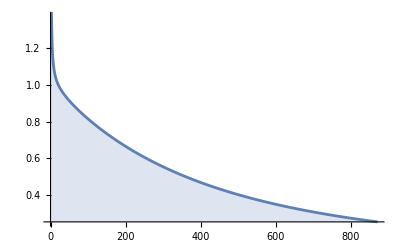

((1-1/n^2)^q+n^2-(1-1/n^2)^q n^2)/q

(-1+ⅇ)/ⅇ

(1-(1-1/n)^(-1+n HarmonicNumber[n]))/(1-(1-1/n)^(n HarmonicNumber[n]))

(1-(1-1/n^2)^j)/(1-(1-1/n^2)^(n^2 HarmonicNumber[n^2]))

```mathematica
n=15;
DiscretePlot[((1-1/n^2)^q+n^2-(1-1/n^2)^q n^2)/(q),{q,0,n^2.5}]
Clear[n]
Sum[(1-b2D[x]/n^2),{x,0,q}]/q
Limit[b1D[n]/(n),n->Infinity]
b1D[n*HarmonicNumber[n]-1]/b1D[n*HarmonicNumber[n]]
b2D[j]/b2D[(n^2)*HarmonicNumber[(n^2)]]
```

```mathematica
Assuming[0<=k<1,Limit[b1D[n*(Log[n]^k)]/((1-E^(-Log[n]^k))*n),n->Infinity]]
Assuming[0<=k<1,Limit[b1D[n*(Log[n]^k)]/b1D[n*HarmonicNumber[n]],n->Infinity]]
Limit[b2D[Sqrt[E/(Pi)^2]n^2]/b2D[(n^2)*HarmonicNumber[(n^2)]],n->Infinity]//N
Sqrt[E/(Pi)^2]//N
```

1

1

0.408329

0.524804

```mathematica
Sum[(1-b2D[x]/n^2),{x,0,q}]
N[(-1+E)/E,20]
```

(1-1/n^2)^q+n^2-(1-1/n^2)^q n^2

0.6321205588285576784

```mathematica
Clear[n]
InverseFunction[b1D][x]
InverseFunction[b2D][x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Log[(n-x)/n]/Log[1-1/n]

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

Log[(n^2-x)/n^2]/Log[1-1/n^2]

```mathematica
{Limit[b1D[(n^2)*(HarmonicNumber[n^2]-HarmonicNumber[(n^2)-m])],n->Infinity],Limit[b1D[Log[(-m+n)/n]/Log[1-1/n]],n->Infinity]}
{Limit[b2D[(n^2)*(HarmonicNumber[n^2]-HarmonicNumber[(n^2)-m])],n->Infinity],Limit[b2D[Log[(-m+n^2)/n^2]/Log[1-1/n^2]],n->Infinity]}
```

{m,m}

{m,m}

Best case iteration limit

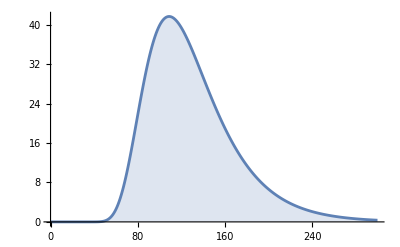

∑_(k=1)^∞ (k (m n)^-k (m n)! StirlingS2[k,j])/((-j+m n)!)

```mathematica
DiscretePlot[{p[k,29,30,1]*k},{k,0,10*30}]
Sum[p[k,j,n,m]*k,{k,1,Infinity}]//FullSimplify
```

```mathematica
a[n_,m_]:=(n-m)*StirlingS1[n+1,n+1-m]
p[x_,j_]:=Sum[a[j,i-1]*x^(j-i+1),{i,1,j}]
m[x_,j_]:=(Factorial[x]/Factorial[x-j])*(p[x,j])/(Product[(x-i)^2,{i,1,j}])
m[x,j]
Limit[m[x,5]/(x (-HarmonicNumber[x-5]+HarmonicNumber[x])),x->Infinity]
```

(x! ∑_(i=1)^j (1-i+j) x^(1-i+j) StirlingS1[1+j,2-i+j])/((-j+x)! Pochhammer[1-x,j]^2)

1

Best case iteration limit for 2D matrix

```mathematica
Limit[Log[(-m+n^x)/n^x]/Log[1-1/n^x]/(m),n->Infinity]
Limit[((n^x)*(HarmonicNumber[n^x]-HarmonicNumber[(n^x)-m]))/(m),n->Infinity]
Limit[((n^x)*(HarmonicNumber[n^x]))/((n^x)*Log[n^x]),n->Infinity]
```

ConditionalExpression[1, (1/m|m)∈ℝ&&x>0]

ConditionalExpression[1, (1/m|m)∈ℝ&&x>0]

ConditionalExpression[1, x>0]

Best possible case  complexity
n/2+2*(n/4)+6*(n/8)+14*(n/16)+30*(n/32)+...

```mathematica
RSolve[{f[i]==2 (1+f[i-1]),f[2]==2},f[i],i]
Table[-2+2^i,{i,1,15}]
Solve[{(-2+2^x)==(n)},x]
n/2+n*Sum[(-2+2^x)/(2^x),{x,2,q}]//FullSimplify
n/2+n*Sum[(-2+2^x)/(2^x),{x,2,Log[2,n]}]//FullSimplify
n*Sum[1/(2^i),{i,1,Log[2,n]}]//FullSimplify
```

{{f[i]→-2+2^i}}

{0,2,6,14,30,62,126,254,510,1022,2046,4094,8190,16382,32766}

{{x→ConditionalExpression[(2 ⅈ π C[1])/Log[2]+Log[2+n]/Log[2], C[1]∈ℤ]}}

n (-3/2+2^(1-q)+q)

(-n Log[8]+Log[16]+2 n Log[n])/Log[4]

-1+n

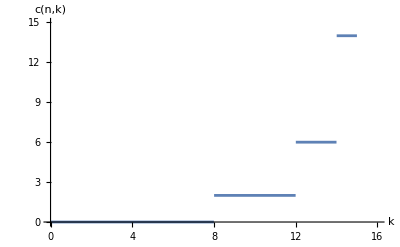

{-1,0,2,6,14,30,62,126,254,510,1022,2046,4094,8190,16382,32766,65534}

```mathematica
n=4;
Plot[(-2+2^Floor[Log2[2(n^2)/(n^2-k)]]),{k,0,n^2},AxesLabel->{"k","c(n,k)"}]
Clear[n]
Table[2^x-2,{x,0,16}]
```

Average cluster size 1D

```mathematica
w1[n_]:=1
w2[n_]:=(2*Binomial[n,2])/((n-1)+2*(Binomial[n,2]-(n-1)))
w3[n_]:=(3*Binomial[n,3])/((n-2)+2*((n-3)*(n-4)+2*(n-3))+3*(Binomial[n,3]-(n-2)-((n-3)*(n-4)+2*(n-3))))
w4[n_]:=(4*Binomial[n,4])/((n-3)+2*(2*(n-4)+(n-5)(n-4)+Binomial[n-3,2])+3*(Binomial[n,4]-(n-3)-(2*(n-4)+(n-5)(n-4)+Binomial[n-3,2])-(1/24 (n-6)(n-5)(n-4)(n-3)))+4*(1/24 (n-6)(n-5)(n-4)(n-3) ))
{w2[n],Limit[w2[n],n->Infinity]}//FullSimplify
{w3[n],Limit[w3[n],n->Infinity]}//FullSimplify
{w4[n],Limit[w4[n],n->Infinity]}//FullSimplify
w[n_,k_]:=n/(n-k+1)
RSolve[{a[n+1,k+1]==a[n,k+1]+a[n,k]+Binomial[n-1,k],a[n,k]==0&&(k<=0||n<k),a[n,1]==n&&1<=n},a[n,k],{n,k}]
```

{n/(-1+n),1}

{n/(-2+n),1}

{n/(-3+n),1}

RSolve::deqn: Equation or list of equations expected instead of k≤0||n<k in the first argument {a[1+n,1+k]==a[n,k]+a[n,1+k]+Binomial[-1+n,k],a[n,k]==0&&(k≤0||n<k),a[n,1]==n&&1≤n}.

RSolve[{a[1+n,1+k]==a[n,k]+a[n,1+k]+Binomial[-1+n,k],a[n,k]==0&&(k≤0||n<k),a[n,1]==n&&1≤n},a[n,k],{n,k}]

Average cluster size 2D

```mathematica
w1[n_]:=1
w2[n_]:=(2*Binomial[n^2,2])/(2*n(n-1)+2*(n-1)*(n-1)+2*(Binomial[n^2,2]-(2*n(n-1)+2*(n-1)*(n-1))))
w3[n_]:=(3*Binomial[n^2,3])/(2*n*(n-2)+2*(n-2)*(n-2)+8*(n-2)*(n-1)+4*(n-2)*(n-1)+4*(n-1)*(n-1)+2*(Binomial[n^2,3]-(2*n*(n-2)+2*(n-2)*(n-2)+8*(n-2)*(n-1)+4*(n-2)*(n-1)+4*(n-1)*(n-1))-((n-1)*(n-2)*(n^4+3*n^3-20*n^2-30*n+132)/6))+3*((n-1)*(n-2)*(n^4+3*n^3-20*n^2-30*n+132)/6))
w4[n_]:=(4*Binomial[n^2,4])/(2n(n-3)+2(n-3)(n-3)+4*((n^8-54*n^6+72*n^5+995*n^4-2472*n^3-5094*n^2+21480*n-17112)/24))
{w2[n],Limit[w2[n],n->Infinity]}//Expand//Simplify
{w3[n],Limit[w3[n],n->Infinity]}//Expand//Simplify
{w4[n],Limit[w4[n],n->Infinity]}//Expand//Simplify
(*f[x_]:=Factorial[x-1]*x*Binomial[n^2,x]/(n-1)//FunctionExpand//Expand//Simplify
Table[f[k],{k,2,6}]*)
cl[n_,k_]:=(k (1-k+n) Binomial[n,k])/n
RSolve[{b[n,1]==n^2,b[0,k]==0,b[n,k]==Sum[b[n-1,k-k1]+cl[2n-1,k1]Binomial[(n-2)^2,k-k1],{k1,0,2n-1}]},b[n,k],{n,k}]
a[n_,(n_^2)+1]:=0
a[n_,1]:=n^2
a[0,k]:=0
a[n_,k_]:=Piecewise[{{Sum[a[n-1,k-k1]+cl[2n-1,k1]Binomial[((n-2)^2)-0,k-k1],{k1,0,2n-1}],1<k<=n^2}}]
Table[{a[n,k]},{n,0,7},{k,2,3}]
Table[{-2+n (6-5 n+n^3),8+1/2 n (-40+n (22+n (12-11 n+n^3)))},{n,0,7}]
```

{(n^2 (1+n))/(2-4 n+n^2+n^3),1}

{(n^2 (-2-2 n+n^2+n^3))/(-16+24 n+2 n^2-10 n^3+n^4+n^5),1}

{(n^2 (-6+11 n^2-6 n^4+n^6))/(-17004+21372 n-5070 n^2-2472 n^3+995 n^4+72 n^5-54 n^6+n^8),1}

RSolve[{b[n,1]==n^2,b[0,k]==0,b[n,k]==∑_(k1=0)^(-1+2 n) (b[-1+n,k-k1]+(k1 (-k1+2 n) Binomial[(-2+n)^2,k-k1] Binomial[-1+2 n,k1])/(-1+2 n))},b[n,k],{n,k}]

{{{0},{0}},{{0},{0}},{{5},{2}},{{30},{45}},{{103},{345}},{{264},{1560}},{{565},{5174}},{{1070},{14001}}}

{{-2,8},{0,0},{6,4},{52,128},{198,1128},{528,5308},{1150,17780},{2196,48084}}

```mathematica
2*(Binomial[n^2,2]-(2*n(n-1)+2*(n-1)*(n-1)))//FullSimplify//Factor
```

(-2+n) (-1+n) (-2+3 n+n^2)

```mathematica
Limit[(x*Binomial[n^2,x])/(n^(2x)/Factorial[x]*x)//FunctionExpand//FullSimplify,n->Infinity]
a[x_]:=n^(2x)/Factorial[x]*x
num[x_]:=(x*Binomial[n^2,x])
Limit[(a[n^2]/(a[n^2]/n^2))/n^2,n->Infinity]
D[num[x]/Q[x],x]//FullSimplify
Limit[(x*Binomial[n^2,x])/(x*Binomial[n^2,x]+(x-1)(8*Binomial[x,2]/(n^2-1))),{n->Infinity}]
Limit[a[x]/(a[x]),{n->Infinity}]
```

1

1

(Binomial[n^2,x] ((1+x HarmonicNumber[n^2-x]-x HarmonicNumber[x]) Q[x]-x Q'[x]))/Q[x]^2

ConditionalExpression[1, x>1]

1

```mathematica
Sum[q,{q,2,x}]/(x-1)
```

(-2+x+x^2)/(2 (-1+x))

```mathematica
a1[n_,k_]:=4*Binomial[((n-1)^2)-2,k-1]+Binomial[((n-1)^2)-1,k-1]+(2n-6)Binomial[((n-1)^2)-3,k-1]//FullSimplify
a2[n_,k_,k1_]:=cl[2n-1,k1]Binomial[(n-2)^2,k-k1]//FullSimplify
Table[{a1[n,2],a2[n,2,1]},{n,0,20}]
(n^2 (-6+11 n^2-6 n^4+n^6))/(-17004+21372 n-5070 n^2-2472 n^3+995 n^4+72 n^5-54 n^6+n^8)/.n->x
```

{{8,4 cl[-1,1]},{3,cl[1,1]},{0,0},{11,cl[5,1]},{48,4 cl[7,1]},{123,9 cl[9,1]},{248,16 cl[11,1]},{435,25 cl[13,1]},{696,36 cl[15,1]},{1043,49 cl[17,1]},{1488,64 cl[19,1]},{2043,81 cl[21,1]},{2720,100 cl[23,1]},{3531,121 cl[25,1]},{4488,144 cl[27,1]},{5603,169 cl[29,1]},{6888,196 cl[31,1]},{8355,225 cl[33,1]},{10016,256 cl[35,1]},{11883,289 cl[37,1]},{13968,324 cl[39,1]}}

(x^2 (-6+11 x^2-6 x^4+x^6))/(-17004+21372 x-5070 x^2-2472 x^3+995 x^4+72 x^5-54 x^6+x^8)

```mathematica
points4={0,1,85,419,973,1747,2741,3955,5389,7043,8917,11011,13325,15859,18613,21587,24781,28195};
points5={0,0,102,1156,3682,7484,12562,18916,26546,35452,45634,57092};
points6={0,0,78,2658,13028,31992,58620,92912,134868,184488};
(2*n(n-1)+2*(n-1)*(n-1))//Expand//Factor
(2*n*(n-2)+2*(n-2)*(n-2)+8*(n-2)*(n-1)+4*(n-2)*(n-1)+4*(n-1)*(n-1))//Expand//Factor
f4[n_]:=FindSequenceFunction[Drop[points4,2],n]
f4[n-2]//Expand//Factor
f5[n_]:=FindSequenceFunction[Drop[points5,3],n]
f5[n-3]//Expand//Factor
f6[n_]:=FindSequenceFunction[Drop[points6,2],n]
f6[n]//Expand
```

2 (-1+n) (-1+2 n)

4 (-1+n) (-9+5 n)

403-436 n+110 n^2

2 (1906-1608 n+319 n^2)

FindSequenceFunction[{78,2658,13028,31992,58620,92912,134868,184488},n]

## Analysis using p[k,j,n,m] expected number of elements

### Calculate n exponent (1D case)

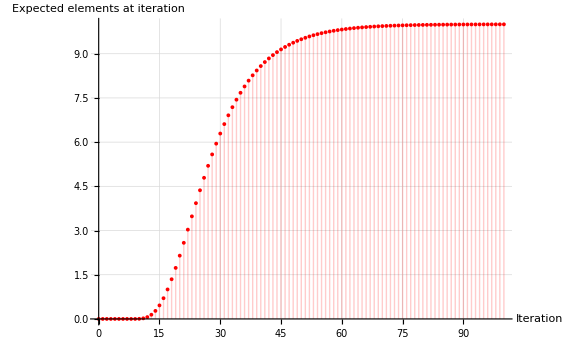

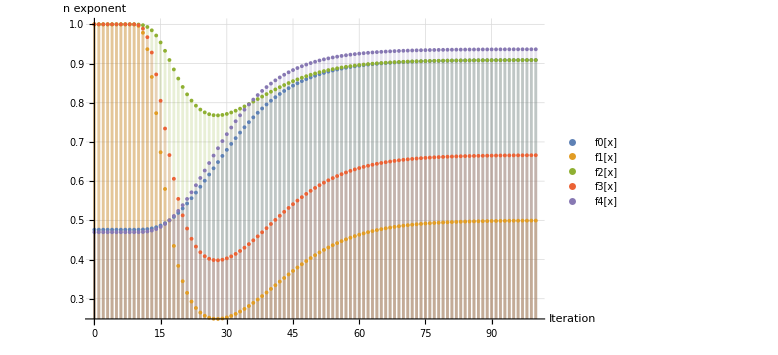

```mathematica
n=10;
b[x_]:=n(1-(1-(1/n))^x);
str[n_,k_]:=1/k! (-1)^i Binomial[k,i] (k-i)^n
p[k_,j_,n_,m_]:=StirlingS2[k,j]*Factorial[n*m]/(Factorial[(n*m)-j]*(n*m)^k)
g[x_]:=-2/(3 Log[x])
g[x_]:=(-1-x^3)/(-1+x^3)
g[x_]:=n/(n-(n*x)+1)
nexp0[x_]:=1*(g[p[x,n,n,1]])/(g[p[x,n,n,1]]+1)
nexp1[x_]:=1*(g[p[x,n,n,1]])/(g[p[x,n,n,1]] +p[x,n,n,1]*n)
nexp2[x_]:=1*(g[p[x,n,n,1]])/(g[p[x,n,n,1]] +p[x,n,n,1])
nexp3[x_]:=1*(g[p[x,n,n,1]])/(g[p[x,n,n,1]] +p[x,n,n,1]*n/2)
nexp4[x_]:=2/Pi *ArcTan[g[p[x,n,n,1]]]
DiscretePlot[{p[x,n,n,1]*n},{x,0,10*n},PlotRange->Full, PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}},AxesLabel->{"Iteration","Expected elements at iteration"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}]
DiscretePlot[{nexp0[x], nexp1[x], nexp2[x], nexp3[x], nexp4[x]},{x,0, 10*n },PlotRange->Full,AxesLabel->{"Iteration","n exponent"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}, PlotLegends->{"f0[x]","f1[x]","f2[x]","f3[x]","f4[x]"}]
Clear[n]
```

### Calculate insertion complexity

```mathematica
seq[x_]:=Sum[p[x,y,n,n]//FullSimplify,{y,0,x}]-Sum[p[x,y,n,n]//FullSimplify,{y,0,n-1}]
seq[x]
Table[seq[x],{x,0,5}]//FullSimplify
Clear[n]
(*FindSequenceFunction[Table[seq[x],{x,1,10}]//FullSimplify,x]*)
```

-∑_(y=0)^(-1+n) ((n^2)^-x n^2! StirlingS2[x,y])/((n^2-y)!)+∑_(y=0)^x ((n^2)^-x n^2! StirlingS2[x,y])/((n^2-y)!)

{1,0,1-(Piecewise[{{1/n^2, n<3}, {1, True}}]),1-(Piecewise[{{1, n≥4}, {1/n^4, n<3}, {(-2+3 n^2)/n^4, True}}]),1-(Piecewise[{{1, n≥5}, {1/n^6, n<3}, {(-6+7 n^2)/n^6, 3≤n<4}, {(6-11 n^2+6 n^4)/n^6, True}}]),1-(Piecewise[{{1, n≥6}, {1/n^8, n<3}, {((-6+5 n^2)^2)/n^8, 4≤n<5}, {(-14+15 n^2)/n^8, 3≤n<4}, {(-24+50 n^2-35 n^4+10 n^6)/n^8, True}}])}

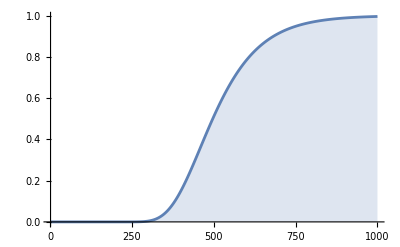

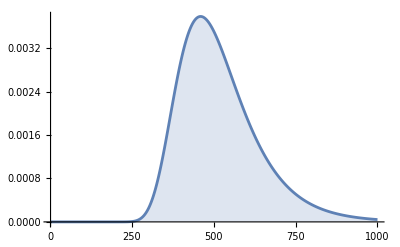

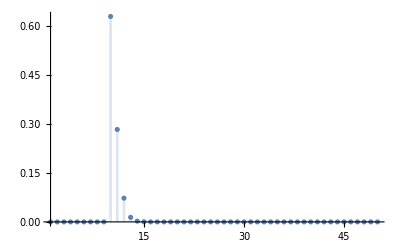

Power::indet: Indeterminate expression 0^0 encountered.

```mathematica
n=10;
DiscretePlot[{p[x,n^2,n,n]},{x,1,n^3},PlotRange->Full]
DiscretePlot[{p[x,n^2,n,n]-p[x-1,n^2,n,n]},{x,1,n^3},PlotRange->Full]
DiscretePlot[{seq[x]-seq[x-1]},{x,1,50},PlotRange->Full]
Clear[n]
data=ParallelTable[Sum[1-p[x,n^2,n,n],{x,0,n^3}],{n,0,20}];
data2=ParallelTable[Sum[1-seq[x],{x,0,n^2}],{n,0,20}];
```

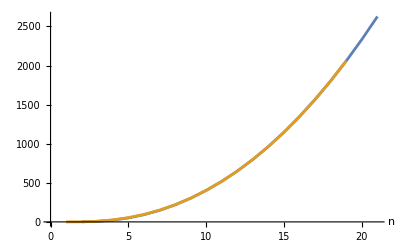

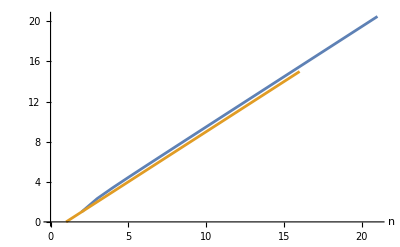

```mathematica
ListLinePlot[{Transpose[{Range[Length[data]],data}],Table[i^2*HarmonicNumber[i^2],{i,0,18}]},AxesLabel->{"n"}]
ListLinePlot[{Transpose[{Range[Length[data2]],data2}],Table[i,{i,0,15}]},AxesLabel->{"n"}]
```

```mathematica
Limit[b[n*(HarmonicNumber[n]-HarmonicNumber[n-j])],n->Infinity]
Limit[p[n*(HarmonicNumber[n]-HarmonicNumber[n-j])//Floor,n,n,1],n->Infinity]
```

j

$Aborted

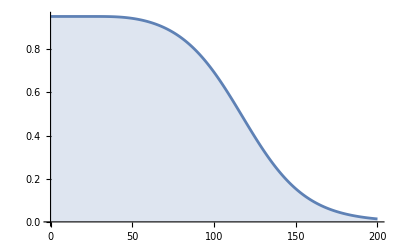

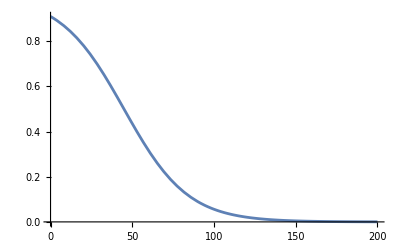

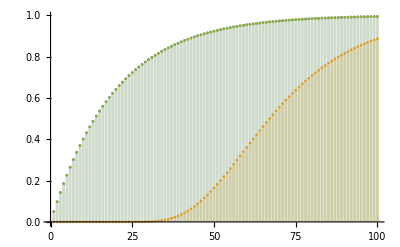

(n (n^x-n! StirlingS2[x,n]))/(n^x (1+n)-n n! StirlingS2[x,n])

∑_(x=0)^q (n (1-n^-x n! StirlingS2[x,n]))/(1+n-n^(1-x) n! StirlingS2[x,n])

```mathematica
n=20;
ins[x_]:=(1-p[x,n,n,1])*n*((g[b[x]/n])/(g[b[x]/n]+n))
ins[x_]:=(1-p[x,n,n,1])*g[p[x,n,n,1]]
DiscretePlot[{ins[x]},{x, 0, 10n}]
Plot[n/(n+2 (-1+n)^-x n^x),{x,0,10n}]
DiscretePlot[{b[x]/n,p[x,n,n,1],Sum[p[x,y,n,1]*y,{y,0,x}]/n},{x,0,100}]
Clear[n]
ins[x]//FullSimplify
Sum[ins[x],{x,0,q}]
```

### Sum insertion complexity until the algorithm ends

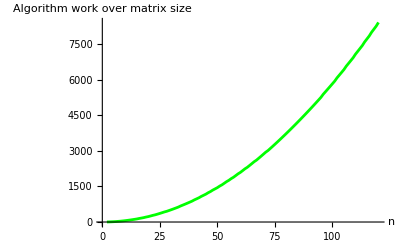

```mathematica
LaunchKernels[];
Clear[n];
points=ParallelTable[{n, Sum[ins[x],{x,0,(n)*HarmonicNumber[n]}]},{n, 2,120}];
ListLinePlot[{points},PlotRange->All,AxesLabel->{"n","Algorithm work over matrix size"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
CloseKernels[];
```

### Fit the sum points

{-0.572299,2.00768}

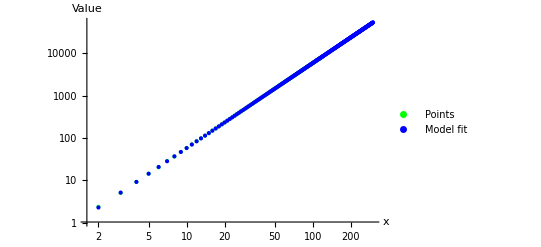

```mathematica
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x];
fittedLine=linearModel["Function"];
linearModel["BestFitParameters"]
ListLogLogPlot[{points, Table[{x,E^fittedLine[x]},{x,2,300}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right]]
```

1.88281
FittedModel[x       ]

#1^1.88281&

| DF | SS | MS
Model | 1 | 1.73011×10^9 | 1.73011×10^9
Error | 118 | 1.05639×10^6 | 8952.48
Uncorrected Total | 119 | 1.73117×10^9 | 
Corrected Total | 118 | 7.58282×10^8 |

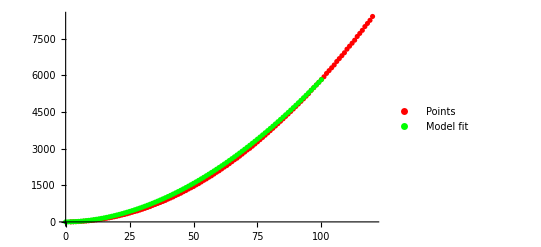

```mathematica
nonlinearModel=NonlinearModelFit[points,x^c,{c},x]
nonlinearModel["Function"]
nonlinearModel["ANOVATable"]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,100}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right]]
```

### Calculate n exponent (2D case)

10

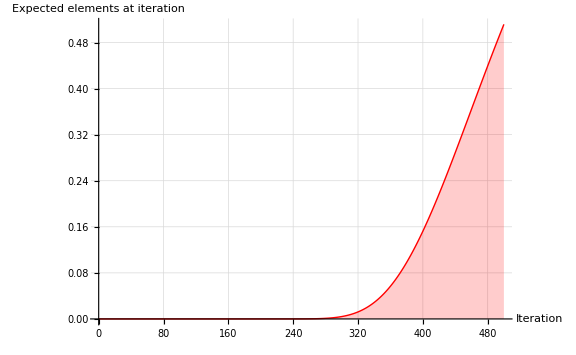

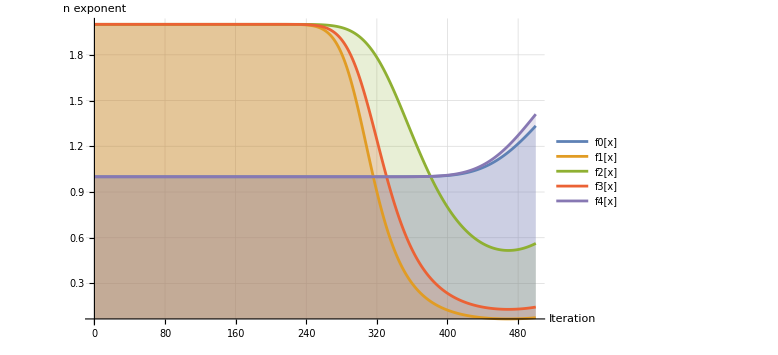

```mathematica
n=10
b[x_]:=(n^2)*(1-(1-(1/n^2))^x);
p[k_,j_,n_,m_]:=StirlingS2[k,j]*Factorial[n*m]/(Factorial[(n*m)-j]*(n*m)^k)
g[x_]:=(2/3)*(-x/Log[x]+LogIntegral[x])
g[x_]:=(1+x (-1+x+2 x^2+x^3-x^4+x^5))/((-1+x)^2 (1+x^2) (1+x+x^2))
nexp0[x_]:=2*(g[p[x,n^2,n,n]])/(g[p[x,n^2,n,n]] +1)
nexp1[x_]:=2*(g[p[x,n^2,n,n]])/(g[p[x,n^2,n,n]] +(p[x,n^2,n,n]*n^2))
nexp2[x_]:=2*(g[p[x,n^2,n,n]])/(g[p[x,n^2,n,n]] +(p[x,n^2,n,n]*n))
nexp3[x_]:=2*(g[p[x,n^2,n,n]])/(g[p[x,n^2,n,n]] +(p[x,n^2,n,n]*n^2)/2)
nexp4[x_]:=4/Pi *ArcTan[g[p[x,n^2,n,n]]]
DiscretePlot[{p[x,n^2,n,n]},{x,0,5*n^2},PlotRange->All, PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}},AxesLabel->{"Iteration","Expected elements at iteration"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}]
DiscretePlot[{nexp0[x], nexp1[x], nexp2[x], nexp3[x], nexp4[x]},{x,0, 5*n^2 },PlotRange->All,AxesLabel->{"Iteration","n exponent"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}, PlotLegends->{"f0[x]","f1[x]","f2[x]","f3[x]","f4[x]"}]
```

### Calculate insertion complexity

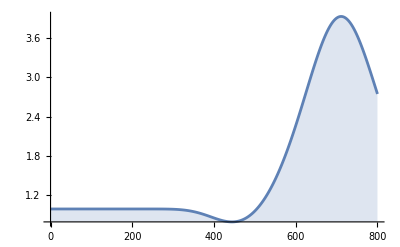

((n^2)^(1-x) ((n^2)^x-n^2! StirlingS2[x,n^2]) ((n^2)^(6 x)+n^2! StirlingS2[x,n^2] (-(n^2)^(5 x)+n^2! StirlingS2[x,n^2] ((n^2)^(4 x)+n^2! StirlingS2[x,n^2] (2 (n^2)^(3 x)+n^2! StirlingS2[x,n^2] ((n^2)^(2 x)+n^2! StirlingS2[x,n^2] (-(n^2)^x+n^2! StirlingS2[x,n^2])))))))/((n^2)^(6 x) (1+n^2)+StirlingS2[x,n^2] (-(n^2)^(5 x) Gamma[2+n^2]+(n^2!)^2 StirlingS2[x,n^2] ((n^2)^(4 x) (1+n^2)+n^2! StirlingS2[x,n^2] (-2 (n^2)^(3 x) (-1+n^2)+StirlingS2[x,n^2] ((n^2)^(2 x) Gamma[2+n^2]+(1+n^2) (n^2!)^2 StirlingS2[x,n^2] (-(n^2)^x+n^2! StirlingS2[x,n^2]))))))

∑_(x=0)^q (n^2 (1-(n^2)^-x n^2! StirlingS2[x,n^2]) (1+(n^2)^-x n^2! StirlingS2[x,n^2] (-1+(n^2)^-x n^2! StirlingS2[x,n^2]+2 (n^2)^(-2 x) (n^2!)^2 StirlingS2[x,n^2]^2+(n^2)^(-3 x) (n^2!)^3 StirlingS2[x,n^2]^3-(n^2)^(-4 x) (n^2!)^4 StirlingS2[x,n^2]^4+(n^2)^(-5 x) (n^2!)^5 StirlingS2[x,n^2]^5)))/((-1+(n^2)^-x n^2! StirlingS2[x,n^2])^2 (1+(n^2)^(-2 x) (n^2!)^2 StirlingS2[x,n^2]^2) (1+(n^2)^-x n^2! StirlingS2[x,n^2]+(n^2)^(-2 x) (n^2!)^2 StirlingS2[x,n^2]^2) (n^2+(1+(n^2)^-x n^2! StirlingS2[x,n^2] (-1+(n^2)^-x n^2! StirlingS2[x,n^2]+2 (n^2)^(-2 x) (n^2!)^2 StirlingS2[x,n^2]^2+(n^2)^(-3 x) (n^2!)^3 StirlingS2[x,n^2]^3-(n^2)^(-4 x) (n^2!)^4 StirlingS2[x,n^2]^4+(n^2)^(-5 x) (n^2!)^5 StirlingS2[x,n^2]^5))/((-1+(n^2)^-x n^2! StirlingS2[x,n^2])^2 (1+(n^2)^(-2 x) (n^2!)^2 StirlingS2[x,n^2]^2) (1+(n^2)^-x n^2! StirlingS2[x,n^2]+(n^2)^(-2 x) (n^2!)^2 StirlingS2[x,n^2]^2))))

```mathematica
n=10;
ins[x_]:=(1-p[x,n^2,n,n])*(n^2)*((g[p[x,n^2,n,n]])/(g[p[x,n^2,n,n]] +n^2))
DiscretePlot[{ins[x]},{x, 0, 8n^2}]
Clear[n]
ins[x]//FullSimplify
Sum[ins[x],{x,0,q}]
```

### Sum insertion complexity until the algorithm ends

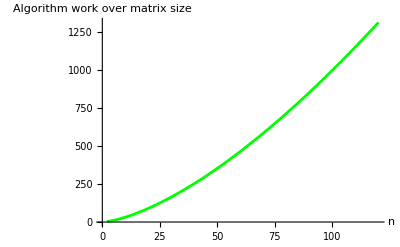

```mathematica
LaunchKernels[];
Clear[n]
points=ParallelTable[{n, Sum[ins[x],{x,0,n^1.5}]},{n, 2,120}];
ListLinePlot[{points},PlotRange->All,AxesLabel->{"n","Algorithm work over matrix size"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
CloseKernels[];
```

### Fit the sum points (finally🤝)

{0.0240138,1.4945}

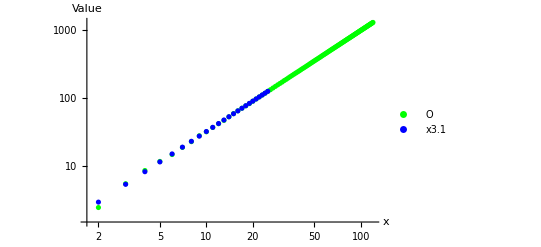

```mathematica
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x];
fittedLine=linearModel["Function"];
linearModel["BestFitParameters"]
ListLogLogPlot[{points, Table[{x,E^fittedLine[x]},{x,2,25}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
```

FittedModel[…]

1.00539 #1^1.49893&

| DF | SS | MS
Model | 2 | 5.27624×10^7 | 2.63812×10^7
Error | 117 | 11.8358 | 0.101161
Uncorrected Total | 119 | 5.27624×10^7 | 
Corrected Total | 118 | 1.85544×10^7 |

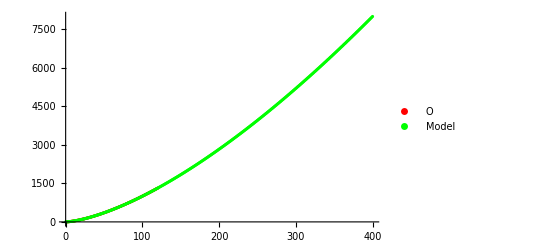

```mathematica
nonlinearModel=NonlinearModelFit[points,a*x^c ,{a,c},x]
nonlinearModel["Function"]
nonlinearModel["ANOVATable"]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,400}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"O","Model"}],Right]]
```

### Calculate n exponent (3D case)

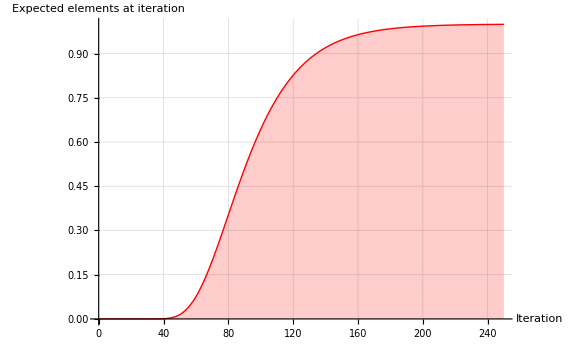

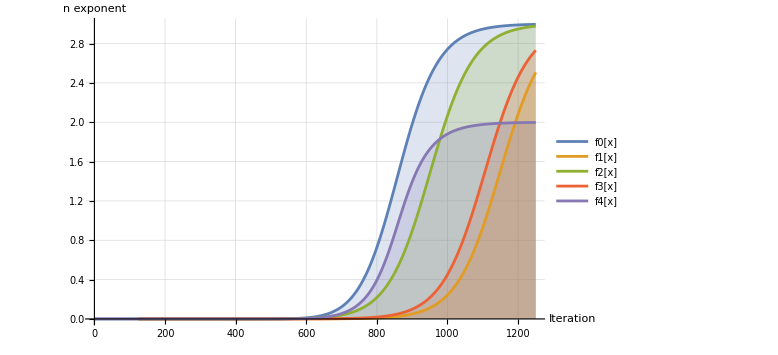

```mathematica
n=5;
b[x_]:=(n^3)*(1-(1-(1/n^3))^x);
p[k_,j_,n_,m_]:=StirlingS2[k,j]*Factorial[n*m]/(Factorial[(n*m)-j]*(n*m)^k)
g[x_]:=-(73309 (-x/(2 Log[x]^2)-x/(2 Log[x])+LogIntegral[x]/2))/1930500
nexp0[x_]:=3*(g[p[x,n^3,n^2,n]])/(g[p[x,n^3,n^2,n]] +1)
nexp1[x_]:=3*(g[p[x,n^3,n^2,n]])/(g[p[x,n^3,n^2,n]] +(p[x,n^3,n^2,n]*n^3))
nexp2[x_]:=3*(g[p[x,n^3,n^2,n]])/(g[p[x,n^3,n^2,n]] +(p[x,n^3,n^2,n]*n))
nexp3[x_]:=3*(g[p[x,n^3,n^2,n]])/(g[p[x,n^3,n^2,n]] +(p[x,n^3,n^2,n]*n^3)/2)
nexp4[x_]:=4/Pi *ArcTan[g[p[x,n^3,n^2,n]]]
DiscretePlot[{p[x,n^2,n,n]},{x,0,2*n^3 },PlotRange->All, PlotStyle->{{Thick,Red},{Thick,Blue,Dashed}},AxesLabel->{"Iteration","Expected elements at iteration"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}]
DiscretePlot[{nexp0[x], nexp1[x], nexp2[x], nexp3[x], nexp4[x]},{x,0, 10*n^3 },PlotRange->All,AxesLabel->{"Iteration","n exponent"},GridLines->Automatic,GridLinesStyle->Directive[GrayLevel[0.8],Dashed],ImageSize->Large,LabelStyle->{FontSize->14}, PlotLegends->{"f0[x]","f1[x]","f2[x]","f3[x]","f4[x]"}]
```

### Calculate insertion complexity

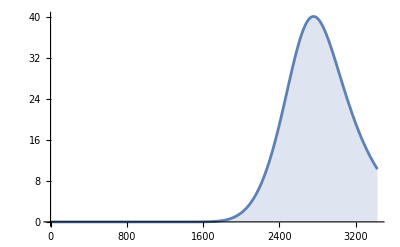

```mathematica
n=7;
ins[x_]:=(1-p[x,n^3,n^2,n])*2(n^3)*((g[p[x,n^3,n^2,n]])/(g[p[x,n^3,n^2,n]] +1))
DiscretePlot[{ins[x]},{x, 0, 10*n^3 }]
```

### Sum insertion complexity until the algorithm ends

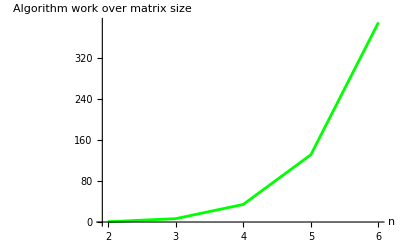

```mathematica
LaunchKernels[];
Clear[n]
points=ParallelTable[{n, Sum[ins[x],{x,0,(n^3)*HarmonicNumber[n^3]}]},{n, 2, 6}];
ListLinePlot[{points},PlotRange->All,AxesLabel->{"n","Algorithm work over matrix size"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
CloseKernels[];
```

### Fit the sum points (finally🤝)

{-4.63008,5.90765}

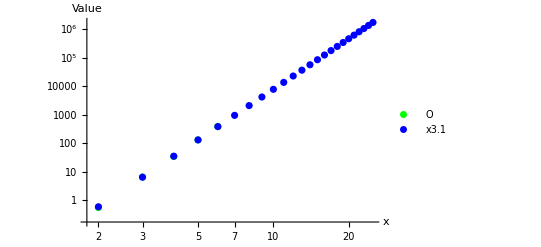

```mathematica
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x];
fittedLine=linearModel["Function"];
linearModel["BestFitParameters"]
ListLogLogPlot[{points, Table[{x,E^fittedLine[x]},{x,2,25}]},PlotRange->All,AxesLabel->{"x","Value"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"O","x3.1","x3"}],Right]]
```

5.97107
FittedModel[0.00879693 x       ]

0.00879693 #1^5.97107&

| DF | SS | MS
Model | 2 | 170315. | 85157.7
Error | 3 | 0.208131 | 0.0693771
Uncorrected Total | 5 | 170316. | 
Corrected Total | 4 | 107062. |

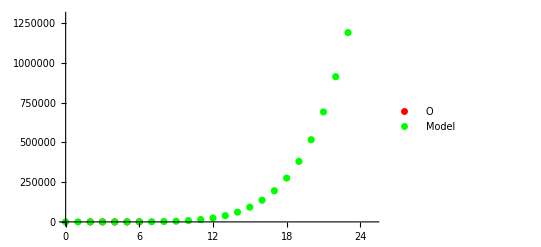

```mathematica
nonlinearModel=NonlinearModelFit[points,a*x^c ,{a,c},x]
nonlinearModel["Function"]
nonlinearModel["ANOVATable"]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,25}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"O","Model"}],Right]]
```

## Data science section

```mathematica
data=Import["C:\\Users\\danie\\Desktop\\JavaProjects\\practica-eda\\PracticaEDA\\t_values_1D2.txt","Table"];
```

FittedModel[5.5533 + 1.14012 Log[x]]

General::munfl: Exp[-170683.] is too small to represent as a normalized machine number; precision may be lost.

| DF | SS | MS | F-Statistic | P-Value
Log[x] | 1 | 33045.8 | 33045.8 | 2.80996×10^6 | 0.
Error | 101786 | 1197.03 | 0.0117602 |  | 
Total | 101787 | 34242.8 |  |  |

General::munfl: Exp[-145299.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-170683.] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 5.5533 | 0.00430183 | 1290.91 | 0.
Log[x] | 1.14012 | 0.000680146 | 1676.29 | 0.

| Estimate | Standard Error | Confidence Interval
1 | 5.5533 | 0.00430183 | {5.54487,5.56173}
Log[x] | 1.14012 | 0.000680146 | {1.13879,1.14146}

0.965043

FittedModel[2.01539 Log[x]]

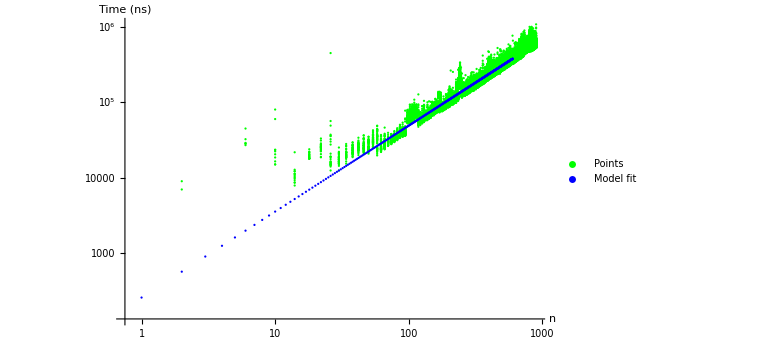

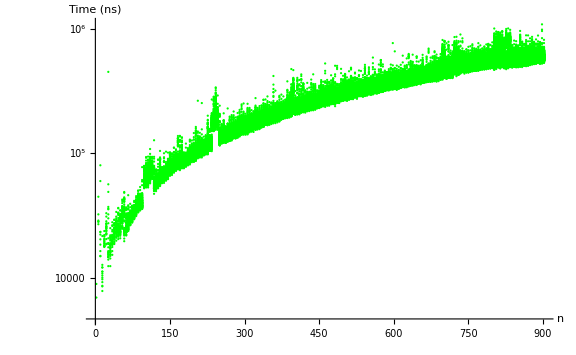

```mathematica
points:=data
logYPoints={#[[1]],Log[#[[2]]]}&/@Rest[points];
linearModel=LinearModelFit[logYPoints,{Log[x]},x]
linearModel["ANOVATable"]
linearModel["ParameterTable"]
linearModel["ParameterConfidenceIntervalTable"]
linearModel["AdjustedRSquared"]
linearModel2=LinearModelFit[logYPoints,{Log[x]},x, IncludeConstantBasis->False]
fittedLine=linearModel["Function"];
ListLogLogPlot[{points,Table[{x, E^linearModel[x]},{x,0,600}]},PlotRange->All,AxesLabel->{"n","Time (ns)"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right],ImageSize->Large]
ListLogPlot[{points},PlotRange->All,AxesLabel->{"n","Time (ns)"},  PlotStyle->{Green, Blue, Red}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right],ImageSize->Large]
```

FittedModel[92.0549 x HarmonicNumber[x]]

| DF | SS | MS
Model | 1 | 1.78911×10^16 | 1.78911×10^16
Error | 101788 | 1.76853×10^14 | 1.73746×10^9
Uncorrected Total | 101789 | 1.8068×10^16 | 
Corrected Total | 101788 | 2.69234×10^15 |

General::munfl: Exp[-235471.] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | 92.0549 | 0.0286871 | 3208.93 | 0.

| Estimate | Standard Error | Confidence Interval
a | 92.0549 | 0.0286871 | {91.9987,92.1111}

0.990212

{{0.000822947}}

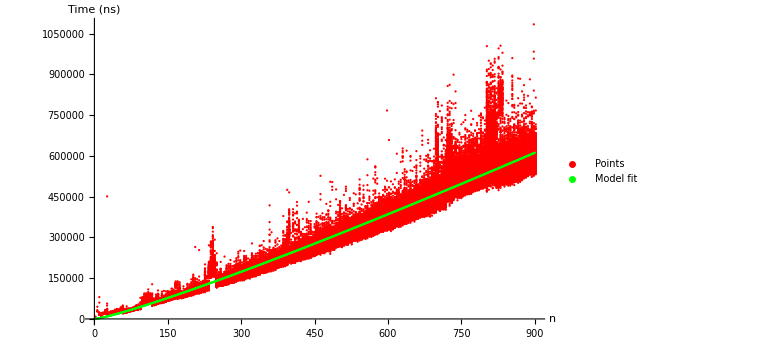

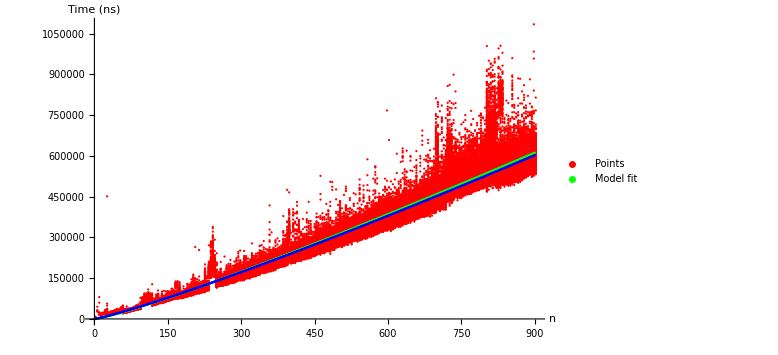

```mathematica
nonlinearModel=NonlinearModelFit[points,a*x*HarmonicNumber[x],{a},x]
nonlinearModel["ANOVATable"]
nonlinearModel["ParameterTable"]
nonlinearModel["ParameterConfidenceIntervalTable"]
nonlinearModel["AdjustedRSquared"]
nonlinearModel["CovarianceMatrix"]
ListPlot[{points,Table[{x, nonlinearModel[x]},{x,0,900}]},PlotStyle->{Red, Green}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right],ImageSize->Large,AxesLabel->{"n","Time (ns)"}]
ListPlot[{points, Table[{x, nonlinearModel[x]},{x,0,900}],Table[{x,E^fittedLine[x]},{x,2,900}]},PlotStyle->{Red, Green,Blue}, PlotLegends->Placed[LineLegend[Automatic,{"Points","Model fit"}],Right],ImageSize->Large,AxesLabel->{"n","Time (ns)"}]
```

```mathematica
RSolve[{f[i]==2 (1+f[i-1]),f[1]==2},f[i],i]//Trace
```

{{{{{{{i-1,-1+i},f[-1+i]},1+f[-1+i]},2 (1+f[-1+i])},f[i]==2 (1+f[-1+i])},{f[i]==2 (1+f[-1+i]),f[1]==2}},RSolve[{f[i]==2 (1+f[-1+i]),f[1]==2},f[i],i],{{f[i]→2 (-1+2^i)}}}

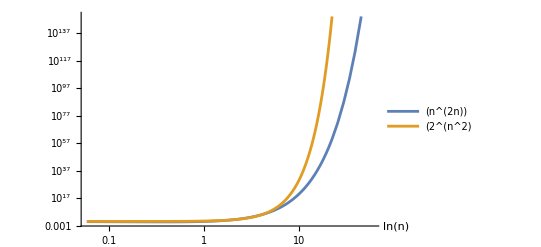

```mathematica
LogLogPlot[{(n^(2n)),(2^(n^2))},{n,0,60},AxesLabel->{"ln(n)"},PlotLegends->{"(n^(2n))","(2^(n^2)"}]
```

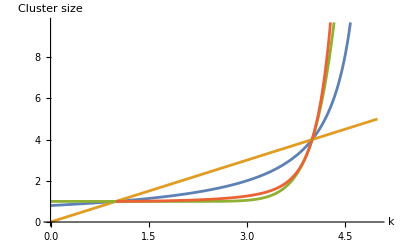

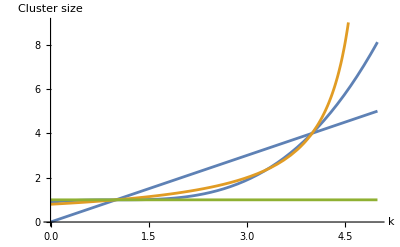

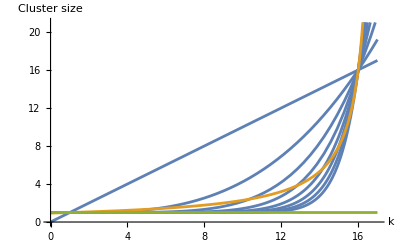

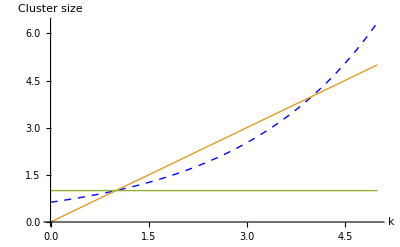

```mathematica
n=4;
c=10;
int[x_]:=x+(((-1+k)/(-1+n))^x (-1+n))/Log[(-1+k)/(-1+n)]
Plot[{n/(n-k+1),k,(((k-1)/(n-1)))^(c) (n-1)+1,(int[20]-int[1])/(20-1)},{k,0,n+1},AxesLabel->{"k","Cluster size"}]
Plot[{Table[(((k-1)/(n-1)))^(c) (n-1)+1,{c,1,n,2}],n/(n-k+1),1},{k,0,n+1},AxesLabel->{"k","Cluster size"},PlotRange->{0,n+5}]
Plot[{Table[(((k-1)/(n^2-1)))^(c) (n^2-1)+1,{c,1,n^2,2}],n^2/(n^2-k+1),1},{k,0,n^2+1},AxesLabel->{"k","Cluster size"},PlotRange->{0,n^2+5}]
Plot[{Exp[(Log[n]/(n-1))*(k-1)],k,1},{k,0,n+1},AxesLabel->{"k","Cluster size"},PlotStyle->{{Blue,Dashed,Thick},{98,Thick},{99,Thick}}]
Clear[n,c]
```

```mathematica
Clear[n]
Clear[c]
i[c_]:=Integrate[(((k-1)/(n-1)))^(x) (n-1)+1,x]/.x->c
i[c]
Integrate[(((k-1)/(n-1)))^(x) (n-1)+1,{x,1,Infinity}]
```

c+(((-1+k)/(-1+n))^c (-1+n))/Log[(-1+k)/(-1+n)]

Integrate::idiv: Integral of 1-((-1+k)/(-1+n))^x+((-1+k)/(-1+n))^x n does not converge on {1,∞}.

∫_1^∞ (1+((-1+k)/(-1+n))^x (-1+n))ⅆx

```mathematica
Sum[n/(n-k+1),{k,0,n}]
```

n (EulerGamma+PolyGamma[0,2+n])

```mathematica
Sum[k,{k,0,n}]
```

1/2 n (1+n)

```mathematica
c[n_,k_,a_,b_]:=1/(b-k)
c[n_,k_,a_,b_]:=a/(a-k+b)
curvature[n_,k_,a_,b_]:=D[c[n,x,a,b],{x,2}]/((1+(D[c[n,x,a,b],x])^2)^(3/2))/.x->k
curvature[n,k+j,a,b]==curvature[n,k,a+r,b]
curvature[n,k+j,a,b]==curvature[n,k,a,b+r]
```

(2 a)/((1+a^2/(a+b-j-k)^4)^(3/2) (a+b-j-k)^3)==(2 (a+r))/((a+b-k+r)^3 (1+(a+r)^2/(a+b-k+r)^4)^(3/2))

(2 a)/((1+a^2/(a+b-j-k)^4)^(3/2) (a+b-j-k)^3)==(2 a)/((a+b-k+r)^3 (1+a^2/(a+b-k+r)^4)^(3/2))

```mathematica
x=a+b-j-k;
y=a+b-k+r;
y==a/x
Solve[y==a/x,j]//FullSimplify
j=a+b-k-a/(a+b-k+r);
(2 a)/((1+a^2/(a+b-j-k)^4)^(3/2) (a+b-j-k)^3)==(2 a)/((a+b-k+r)^3 (1+a^2/(a+b-k+r)^4)^(3/2))
ClearAll[x,y,j,r]
```

a+b-k+r==a/(a+b-j-k)

{{j→a+b-k-a/(a+b-k+r)}}

(2 (a+b-k+r)^3)/(a^2 (1+(a+b-k+r)^4/a^2)^(3/2))==(2 a)/((a+b-k+r)^3 (1+a^2/(a+b-k+r)^4)^(3/2))

```mathematica
(2*a)/((a-(k+j)+b)^3*(1+(a^2)/((a-(k+j)+b)^4))^(3/2))==(2*(a+r))/((a+r-k+b)^3*(1+((a+r)^2)/((a+r-k+b)^4))^(3/2))
a((a+r-k+b)^3*(1+((a+r)^2)/((a+r-k+b)^4))^(3/2))==(a+r)((a-(k+j)+b)^3*(1+(a^2)/((a-(k+j)+b)^4))^(3/2))
((a+r-k+b)^3*(1+((a+r)^2)/((a+r-k+b)^4))^(3/2))/((a-(k+j)+b)^3*(1+(a^2)/((a-(k+j)+b)^4))^(3/2))==(a+r)/a
((a+r-k+b)^1*(1+((a+r)^2)/((a+r-k+b)^4))^(1/2))/((a-(k+j)+b)^1*(1+(a^2)/((a-(k+j)+b)^4))^(1/2))==((a+r)/a)^(1/3)
((a+r-k+b)^2*(1+((a+r)^2)/((a+r-k+b)^4))^(1))/((a-(k+j)+b)^2*(1+(a^2)/((a-(k+j)+b)^4))^(1))==((a+r)/a)^(2/3) (*MAS MENOS*)
((a+r-k+b)^2*(1+((a+r)^2)/((a+r-k+b)^4))^(1))/((a+r)/a)^(2/3)==((a-(k+j)+b)^2*(1+(a^2)/((a-(k+j)+b)^4))^(1)) (*MAS MENOS*)
u==((a-(k+j)+b)^2*(1+(a^2)/((a-(k+j)+b)^4))^(1)) (*MAS MENOS*)
```

(2 a)/((1+a^2/(a+b-j-k)^4)^(3/2) (a+b-j-k)^3)==(2 (a+r))/((a+b-k+r)^3 (1+(a+r)^2/(a+b-k+r)^4)^(3/2))

a (a+b-k+r)^3 (1+(a+r)^2/(a+b-k+r)^4)^(3/2)==(1+a^2/(a+b-j-k)^4)^(3/2) (a+b-j-k)^3 (a+r)

((a+b-k+r)^3 (1+(a+r)^2/(a+b-k+r)^4)^(3/2))/((1+a^2/(a+b-j-k)^4)^(3/2) (a+b-j-k)^3)==(a+r)/a

((a+b-k+r) √(1+(a+r)^2/(a+b-k+r)^4))/(√(1+a^2/(a+b-j-k)^4) (a+b-j-k))==((a+r)/a)^(1/3)

((a+b-k+r)^2 (1+(a+r)^2/(a+b-k+r)^4))/((1+a^2/(a+b-j-k)^4) (a+b-j-k)^2)==((a+r)/a)^(2/3)

((a+b-k+r)^2 (1+(a+r)^2/(a+b-k+r)^4))/((a+r)/a)^(2/3)==(1+a^2/(a+b-j-k)^4) (a+b-j-k)^2

u==(1+a^2/(a+b-j-k)^4) (a+b-j-k)^2

```mathematica
Solve[u==(1+a^2/(a+b-j-k)^4) (a+b-j-k)^2,j]//FullSimplify
```

{{j→a+b-k-(√(u-√(-4 a^2+u^2)))/(√2)},{j→a+b-k+(√(u-√(-4 a^2+u^2)))/(√2)},{j→a+b-k-(√(u+√(-4 a^2+u^2)))/(√2)},{j→a+b-k+(√(u+√(-4 a^2+u^2)))/(√2)}}

```mathematica
u=((a+b-k+r)^2 (1+(a+r)^2/(a+b-k+r)^4))/((a+r)/a)^(2/3)
j=a+b-k-(√(u-√(-4 a^2+u^2)))/(√2)
(2 a)/((1+a^2/(a+b-j-k)^4)^(3/2) (a+b-j-k)^3)==(2 (a+r))/((a+b-k+r)^3 (1+(a+r)^2/(a+b-k+r)^4)^(3/2))
ClearAll[u,j,r]
```

((a+b-k+r)^2 (1+(a+r)^2/(a+b-k+r)^4))/((a+r)/a)^(2/3)

a+b-k-(√(((a+b-k+r)^2 (1+(a+r)^2/(a+b-k+r)^4))/((a+r)/a)^(2/3)-√(-4 a^2+((a+b-k+r)^4 (1+(a+r)^2/(a+b-k+r)^4)^2)/((a+r)/a)^(4/3))))/(√2)

(4 √2 a)/((((a+b-k+r)^2 (1+(a+r)^2/(a+b-k+r)^4))/((a+r)/a)^(2/3)-√(-4 a^2+((a+b-k+r)^4 (1+(a+r)^2/(a+b-k+r)^4)^2)/((a+r)/a)^(4/3)))^(3/2) (1+(4 a^2)/((((a+b-k+r)^2 (1+(a+r)^2/(a+b-k+r)^4))/((a+r)/a)^(2/3)-√(-4 a^2+((a+b-k+r)^4 (1+(a+r)^2/(a+b-k+r)^4)^2)/((a+r)/a)^(4/3)))^2))^(3/2))==(2 (a+r))/((a+b-k+r)^3 (1+(a+r)^2/(a+b-k+r)^4)^(3/2))

```mathematica
Solve[(x^3)(1+a^2/x^4)^(3/2)==(y^3)(1+a^2/y^4)^(3/2),{x,y}]//FullSimplify
Solve[a (y^4+(a+r)^2)^(3/2) x^3==(a+r) (x^4+a^2)^(3/2) y^3,{x,y}]//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→-a/x},{y→a/x},{y→x},{y→-1/2 √(-(a^2+x^4+√3 √(-(a^2+x^4)^2)+x^2 √(2 √3 √(-(a^2+x^4)^2)-(2 (a^4+x^8+a^2 (10 x^4-√3 √(-(a^2+x^4)^2))))/x^4))/x^2)},{y→1/2 √(-(a^2+x^4+√3 √(-(a^2+x^4)^2)+x^2 √(2 √3 √(-(a^2+x^4)^2)-(2 (a^4+x^8+a^2 (10 x^4-√3 √(-(a^2+x^4)^2))))/x^4))/x^2)},{y→-1/2 √(-(a^2+x^4+√3 √(-(a^2+x^4)^2)-x^2 √(2 √3 √(-(a^2+x^4)^2)-(2 (a^4+x^8+a^2 (10 x^4-√3 √(-(a^2+x^4)^2))))/x^4))/x^2)},{y→1/2 √(-(a^2+x^4+√3 √(-(a^2+x^4)^2)-x^2 √(2 √3 √(-(a^2+x^4)^2)-(2 (a^4+x^8+a^2 (10 x^4-√3 √(-(a^2+x^4)^2))))/x^4))/x^2)},{y→-1/2 √(-(a^2+x^4-√3 √(-(a^2+x^4)^2)+√2 x^2 √(-(a^4+x^8+√3 x^4 √(-(a^2+x^4)^2)+a^2 (10 x^4+√3 √(-(a^2+x^4)^2)))/x^4))/x^2)},{y→1/2 √(-(a^2+x^4-√3 √(-(a^2+x^4)^2)+√2 x^2 √(-(a^4+x^8+√3 x^4 √(-(a^2+x^4)^2)+a^2 (10 x^4+√3 √(-(a^2+x^4)^2)))/x^4))/x^2)},{y→-1/2 √((-a^2-x^4+√3 √(-(a^2+x^4)^2)+√2 x^2 √(-(a^4+x^8+√3 x^4 √(-(a^2+x^4)^2)+a^2 (10 x^4+√3 √(-(a^2+x^4)^2)))/x^4))/x^2)},{y→1/2 √((-a^2-x^4+√3 √(-(a^2+x^4)^2)+√2 x^2 √(-(a^4+x^8+√3 x^4 √(-(a^2+x^4)^2)+a^2 (10 x^4+√3 √(-(a^2+x^4)^2)))/x^4))/x^2)}}

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→-√Root[a^6+3 a^4 #1^2+(-a^8/((a+r)^2 y^6)-(6 a^7 r)/((a+r)^2 y^6)-(15 a^6 r^2)/((a+r)^2 y^6)-(20 a^5 r^3)/((a+r)^2 y^6)-(15 a^4 r^4)/((a+r)^2 y^6)-(6 a^3 r^5)/((a+r)^2 y^6)-(a^2 r^6)/((a+r)^2 y^6)-(3 a^6)/((a+r)^2 y^2)-(12 a^5 r)/((a+r)^2 y^2)-(18 a^4 r^2)/((a+r)^2 y^2)-(12 a^3 r^3)/((a+r)^2 y^2)-(3 a^2 r^4)/((a+r)^2 y^2)-(3 a^4 y^2)/(a+r)^2-(6 a^3 r y^2)/(a+r)^2-(3 a^2 r^2 y^2)/(a+r)^2-(a^2 y^6)/(a+r)^2) #1^3+3 a^2 #1^4+#1^6&,1]},{x→√Root[a^6+3 a^4 #1^2+(-a^8/((a+r)^2 y^6)-(6 a^7 r)/((a+r)^2 y^6)-(15 a^6 r^2)/((a+r)^2 y^6)-(20 a^5 r^3)/((a+r)^2 y^6)-(15 a^4 r^4)/((a+r)^2 y^6)-(6 a^3 r^5)/((a+r)^2 y^6)-(a^2 r^6)/((a+r)^2 y^6)-(3 a^6)/((a+r)^2 y^2)-(12 a^5 r)/((a+r)^2 y^2)-(18 a^4 r^2)/((a+r)^2 y^2)-(12 a^3 r^3)/((a+r)^2 y^2)-(3 a^2 r^4)/((a+r)^2 y^2)-(3 a^4 y^2)/(a+r)^2-(6 a^3 r y^2)/(a+r)^2-(3 a^2 r^2 y^2)/(a+r)^2-(a^2 y^6)/(a+r)^2) #1^3+3 a^2 #1^4+#1^6&,1]},{x→-√Root[a^6+3 a^4 #1^2+(-a^8/((a+r)^2 y^6)-(6 a^7 r)/((a+r)^2 y^6)-(15 a^6 r^2)/((a+r)^2 y^6)-(20 a^5 r^3)/((a+r)^2 y^6)-(15 a^4 r^4)/((a+r)^2 y^6)-(6 a^3 r^5)/((a+r)^2 y^6)-(a^2 r^6)/((a+r)^2 y^6)-(3 a^6)/((a+r)^2 y^2)-(12 a^5 r)/((a+r)^2 y^2)-(18 a^4 r^2)/((a+r)^2 y^2)-(12 a^3 r^3)/((a+r)^2 y^2)-(3 a^2 r^4)/((a+r)^2 y^2)-(3 a^4 y^2)/(a+r)^2-(6 a^3 r y^2)/(a+r)^2-(3 a^2 r^2 y^2)/(a+r)^2-(a^2 y^6)/(a+r)^2) #1^3+3 a^2 #1^4+#1^6&,2]},{x→√Root[a^6+3 a^4 #1^2+(-a^8/((a+r)^2 y^6)-(6 a^7 r)/((a+r)^2 y^6)-(15 a^6 r^2)/((a+r)^2 y^6)-(20 a^5 r^3)/((a+r)^2 y^6)-(15 a^4 r^4)/((a+r)^2 y^6)-(6 a^3 r^5)/((a+r)^2 y^6)-(a^2 r^6)/((a+r)^2 y^6)-(3 a^6)/((a+r)^2 y^2)-(12 a^5 r)/((a+r)^2 y^2)-(18 a^4 r^2)/((a+r)^2 y^2)-(12 a^3 r^3)/((a+r)^2 y^2)-(3 a^2 r^4)/((a+r)^2 y^2)-(3 a^4 y^2)/(a+r)^2-(6 a^3 r y^2)/(a+r)^2-(3 a^2 r^2 y^2)/(a+r)^2-(a^2 y^6)/(a+r)^2) #1^3+3 a^2 #1^4+#1^6&,2]},{x→-√Root[a^6+3 a^4 #1^2+(-a^8/((a+r)^2 y^6)-(6 a^7 r)/((a+r)^2 y^6)-(15 a^6 r^2)/((a+r)^2 y^6)-(20 a^5 r^3)/((a+r)^2 y^6)-(15 a^4 r^4)/((a+r)^2 y^6)-(6 a^3 r^5)/((a+r)^2 y^6)-(a^2 r^6)/((a+r)^2 y^6)-(3 a^6)/((a+r)^2 y^2)-(12 a^5 r)/((a+r)^2 y^2)-(18 a^4 r^2)/((a+r)^2 y^2)-(12 a^3 r^3)/((a+r)^2 y^2)-(3 a^2 r^4)/((a+r)^2 y^2)-(3 a^4 y^2)/(a+r)^2-(6 a^3 r y^2)/(a+r)^2-(3 a^2 r^2 y^2)/(a+r)^2-(a^2 y^6)/(a+r)^2) #1^3+3 a^2 #1^4+#1^6&,3]},{x→√Root[a^6+3 a^4 #1^2+(-a^8/((a+r)^2 y^6)-(6 a^7 r)/((a+r)^2 y^6)-(15 a^6 r^2)/((a+r)^2 y^6)-(20 a^5 r^3)/((a+r)^2 y^6)-(15 a^4 r^4)/((a+r)^2 y^6)-(6 a^3 r^5)/((a+r)^2 y^6)-(a^2 r^6)/((a+r)^2 y^6)-(3 a^6)/((a+r)^2 y^2)-(12 a^5 r)/((a+r)^2 y^2)-(18 a^4 r^2)/((a+r)^2 y^2)-(12 a^3 r^3)/((a+r)^2 y^2)-(3 a^2 r^4)/((a+r)^2 y^2)-(3 a^4 y^2)/(a+r)^2-(6 a^3 r y^2)/(a+r)^2-(3 a^2 r^2 y^2)/(a+r)^2-(a^2 y^6)/(a+r)^2) #1^3+3 a^2 #1^4+#1^6&,3]},{x→-√Root[a^6+3 a^4 #1^2+(-a^8/((a+r)^2 y^6)-(6 a^7 r)/((a+r)^2 y^6)-(15 a^6 r^2)/((a+r)^2 y^6)-(20 a^5 r^3)/((a+r)^2 y^6)-(15 a^4 r^4)/((a+r)^2 y^6)-(6 a^3 r^5)/((a+r)^2 y^6)-(a^2 r^6)/((a+r)^2 y^6)-(3 a^6)/((a+r)^2 y^2)-(12 a^5 r)/((a+r)^2 y^2)-(18 a^4 r^2)/((a+r)^2 y^2)-(12 a^3 r^3)/((a+r)^2 y^2)-(3 a^2 r^4)/((a+r)^2 y^2)-(3 a^4 y^2)/(a+r)^2-(6 a^3 r y^2)/(a+r)^2-(3 a^2 r^2 y^2)/(a+r)^2-(a^2 y^6)/(a+r)^2) #1^3+3 a^2 #1^4+#1^6&,4]},{x→√Root[a^6+3 a^4 #1^2+(-a^8/((a+r)^2 y^6)-(6 a^7 r)/((a+r)^2 y^6)-(15 a^6 r^2)/((a+r)^2 y^6)-(20 a^5 r^3)/((a+r)^2 y^6)-(15 a^4 r^4)/((a+r)^2 y^6)-(6 a^3 r^5)/((a+r)^2 y^6)-(a^2 r^6)/((a+r)^2 y^6)-(3 a^6)/((a+r)^2 y^2)-(12 a^5 r)/((a+r)^2 y^2)-(18 a^4 r^2)/((a+r)^2 y^2)-(12 a^3 r^3)/((a+r)^2 y^2)-(3 a^2 r^4)/((a+r)^2 y^2)-(3 a^4 y^2)/(a+r)^2-(6 a^3 r y^2)/(a+r)^2-(3 a^2 r^2 y^2)/(a+r)^2-(a^2 y^6)/(a+r)^2) #1^3+3 a^2 #1^4+#1^6&,4]},{x→-√Root[a^6+3 a^4 #1^2+(-a^8/((a+r)^2 y^6)-(6 a^7 r)/((a+r)^2 y^6)-(15 a^6 r^2)/((a+r)^2 y^6)-(20 a^5 r^3)/((a+r)^2 y^6)-(15 a^4 r^4)/((a+r)^2 y^6)-(6 a^3 r^5)/((a+r)^2 y^6)-(a^2 r^6)/((a+r)^2 y^6)-(3 a^6)/((a+r)^2 y^2)-(12 a^5 r)/((a+r)^2 y^2)-(18 a^4 r^2)/((a+r)^2 y^2)-(12 a^3 r^3)/((a+r)^2 y^2)-(3 a^2 r^4)/((a+r)^2 y^2)-(3 a^4 y^2)/(a+r)^2-(6 a^3 r y^2)/(a+r)^2-(3 a^2 r^2 y^2)/(a+r)^2-(a^2 y^6)/(a+r)^2) #1^3+3 a^2 #1^4+#1^6&,5]},{x→√Root[a^6+3 a^4 #1^2+(-a^8/((a+r)^2 y^6)-(6 a^7 r)/((a+r)^2 y^6)-(15 a^6 r^2)/((a+r)^2 y^6)-(20 a^5 r^3)/((a+r)^2 y^6)-(15 a^4 r^4)/((a+r)^2 y^6)-(6 a^3 r^5)/((a+r)^2 y^6)-(a^2 r^6)/((a+r)^2 y^6)-(3 a^6)/((a+r)^2 y^2)-(12 a^5 r)/((a+r)^2 y^2)-(18 a^4 r^2)/((a+r)^2 y^2)-(12 a^3 r^3)/((a+r)^2 y^2)-(3 a^2 r^4)/((a+r)^2 y^2)-(3 a^4 y^2)/(a+r)^2-(6 a^3 r y^2)/(a+r)^2-(3 a^2 r^2 y^2)/(a+r)^2-(a^2 y^6)/(a+r)^2) #1^3+3 a^2 #1^4+#1^6&,5]},{x→-√Root[a^6+3 a^4 #1^2+(-a^8/((a+r)^2 y^6)-(6 a^7 r)/((a+r)^2 y^6)-(15 a^6 r^2)/((a+r)^2 y^6)-(20 a^5 r^3)/((a+r)^2 y^6)-(15 a^4 r^4)/((a+r)^2 y^6)-(6 a^3 r^5)/((a+r)^2 y^6)-(a^2 r^6)/((a+r)^2 y^6)-(3 a^6)/((a+r)^2 y^2)-(12 a^5 r)/((a+r)^2 y^2)-(18 a^4 r^2)/((a+r)^2 y^2)-(12 a^3 r^3)/((a+r)^2 y^2)-(3 a^2 r^4)/((a+r)^2 y^2)-(3 a^4 y^2)/(a+r)^2-(6 a^3 r y^2)/(a+r)^2-(3 a^2 r^2 y^2)/(a+r)^2-(a^2 y^6)/(a+r)^2) #1^3+3 a^2 #1^4+#1^6&,6]},{x→√Root[a^6+3 a^4 #1^2+(-a^8/((a+r)^2 y^6)-(6 a^7 r)/((a+r)^2 y^6)-(15 a^6 r^2)/((a+r)^2 y^6)-(20 a^5 r^3)/((a+r)^2 y^6)-(15 a^4 r^4)/((a+r)^2 y^6)-(6 a^3 r^5)/((a+r)^2 y^6)-(a^2 r^6)/((a+r)^2 y^6)-(3 a^6)/((a+r)^2 y^2)-(12 a^5 r)/((a+r)^2 y^2)-(18 a^4 r^2)/((a+r)^2 y^2)-(12 a^3 r^3)/((a+r)^2 y^2)-(3 a^2 r^4)/((a+r)^2 y^2)-(3 a^4 y^2)/(a+r)^2-(6 a^3 r y^2)/(a+r)^2-(3 a^2 r^2 y^2)/(a+r)^2-(a^2 y^6)/(a+r)^2) #1^3+3 a^2 #1^4+#1^6&,6]},{x→0,y→0}}

```mathematica
p=0.9;
c=1;
f[x_,y_]:=p^(Abs[x]^c+Abs[y]^c+Abs[x+y]^c+Abs[y-x]^c)
Plot3D[{f[x,y],p^Sqrt[x^2+y^2]},{x,-11,11},{y,-11,11}, PlotRange->{0,1}, ColorFunction->"AvocadoColors",  PlotPoints->200,Mesh->None,ImageSize->Medium]
Plot3D[{p^(x+y+x+y+Abs[x-y])},{x,0,11},{y,0,11}, PlotRange->{0,1}, ColorFunction->"AvocadoColors",  PlotPoints->200,Mesh->None,ImageSize->Medium]
Clear[p]
```

-Graphics3D-

-Graphics3D-

```mathematica
f[x,y]==f[-x,y]//FullSimplify
f[x,y]==f[x,-y]//FullSimplify
f[-x,y]==f[x,-y]//FullSimplify
f[x,-y]==f[-x,y]//FullSimplify
f[x,0]
f[x,x]
```

True

True

True

«1 more identical outputs»

p^(3 Abs[x])

p^(4 Abs[x])

```mathematica
Integrate[p^(x+y+x+y+x-y),{x,0,Infinity},{y,0,x}]
Integrate[p^(x+y+x+y-x+y),{y,0,Infinity},{x,0,y}]
```

ConditionalExpression[1/(12 Log[p]^2), Re[Log[p]]<0]

ConditionalExpression[1/(12 Log[p]^2), Re[Log[p]]<0]

```mathematica
Sum[p^(3x),{x,1,Infinity}]
Sum[p^(4x),{x,1,Infinity}]
Sum[p^(3Abs[x]),{x,-Infinity,Infinity}]
Sum[p^(4Abs[x]),{x,-Infinity,Infinity}]
```

-p^3/(-1+p^3)

-p^4/(-1+p^4)

(-1-p^3)/(-1+p^3)

(-1-p^4)/(-1+p^4)

```mathematica
Sum[p^(Abs[x]+Abs[y]+Abs[x+y]+Abs[y-x]),{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

$Aborted

```mathematica
Sum[p^(x+y+x+y+x-y),{x,2,Infinity},{y,1,x-1}]
Sum[p^(x+y+x+y-x+y),{y,2,Infinity},{x,1,y-1}]
```

p^7/((-1+p)^2 (1+p+p^2) (1+p+p^2+p^3))

p^7/((-1+p)^2 (1+p+p^2) (1+p+p^2+p^3))

```mathematica
Sum[p^(x+y+x+y+x-y),{y,1,x-1}]
```

-(p^(3 x) (p-p^x))/(-1+p)

```mathematica
8*(p^7/((-1+p)^2 (1+p+p^2) (1+p+p^2+p^3)))+4*(-p^3/(-1+p^3)-p^4/(-1+p^4))+1//FullSimplify
```

(1+p (-1+p+2 p^2+p^3-p^4+p^5))/((-1+p)^2 (1+p^2) (1+p+p^2))

(1+p (-1+p+2 p^2+p^3-p^4+p^5))/((-1+p)^2 (1+p^2) (1+p+p^2))

```mathematica
Integrate[p^(3Abs[x]),{x,-Infinity,Infinity}]
```

Piecewise[{{-2/(3 Log[p]), Re[Log[p]]<0}, {Integrate[p^(3 Abs[x]),{x,-∞,∞},Assumptions→Re[Log[p]]≥0], True}}]

```mathematica
Integrate[p^Sqrt[x^2+y^2],{x,0,Infinity},{y,0,Infinity}]
Integrate[p^Sqrt[x^2+y^2],{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

∫_0^∞ ∫_0^∞ p^(√(x^2+y^2))ⅆyⅆx

∫_(-∞)^∞ ∫_(-∞)^∞ p^(√(x^2+y^2))ⅆyⅆx

```mathematica
Integrate[p^(Abs[x]+Abs[y]+Abs[x+y]+Abs[y-x]),{x,0,Infinity},{y,0,Infinity}]
Integrate[p^(Abs[x]+Abs[y]+Abs[x+y]+Abs[y-x]),{x,-Infinity,Infinity},{y,-Infinity,Infinity}]
```

Piecewise[{{1/(6 Log[p]^2), Re[Log[p]]<0}, {Integrate[p^(Abs[x]+Abs[y]+Abs[-x+y]+Abs[x+y]),{x,0,∞},{y,0,∞},Assumptions→Re[Log[p]]≥0], True}}]

Piecewise[{{2/(3 Log[p]^2), Re[Log[p]]<0}, {Integrate[p^(Abs[x]+Abs[y]+Abs[-x+y]+Abs[x+y]),{x,-∞,∞},{y,-∞,∞},Assumptions→Re[Log[p]]≥0], True}}]

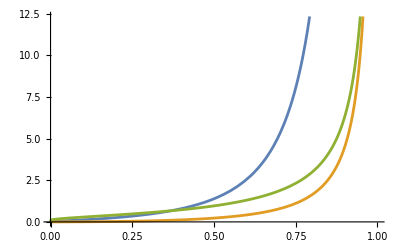

2/3 (-p/Log[p]+LogIntegral[p])

```mathematica
Plot[{2/(3 Log[p]^2),2/3 (-p/Log[p]+LogIntegral[p]),-2/(3 Log[p])},{p,0,1}]
Integrate[2/(3 Log[p]^2),p]
```

4

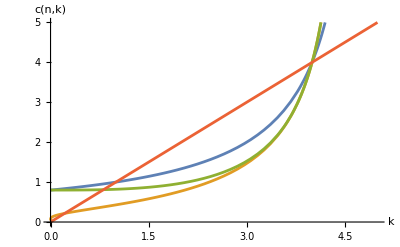

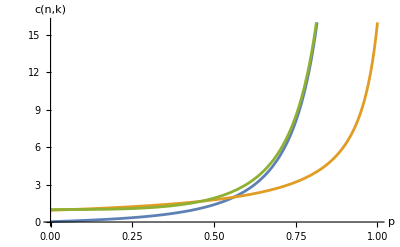

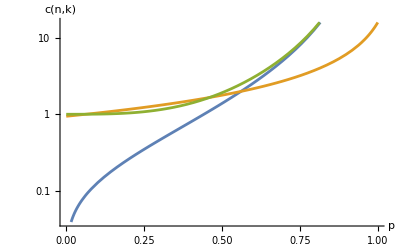

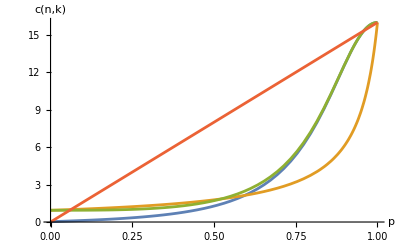

(2-2 p-3 Log[p]^2)/(3 Log[p]^2-3 p Log[p]^2)

(-2+2 p-3 Log[p])/(3 Log[p]-3 p Log[p])

Hold[∑_(x=0)^(n HarmonicNumber[n]) ((1+(1-(1-1/n)^x)^3) (1-1/n)^x n)/(1+(1-(1-1/n)^x)^3+n-(1-(1-1/n)^x)^3 n)==$Failed]

```mathematica
n=4
Plot[{n/(n-k+1),n(-2/(3 Log[k/n]))/(-2/(3 Log[k/n])+n),n((-1-(k/n)^3)/(-1+(k/n)^3))/((-1-(k/n)^3)/(-1+(k/n)^3)+n),k},{k,0,n+1},PlotRange->{0,n+1},AxesLabel->{"k","c(n,k)"}]
Plot[{2/(3 Log[p]^2),n^2/(n^2-p*n^2+1),(1+p (-1+p+2 p^2+p^3-p^4+p^5))/((-1+p)^2 (1+p^2) (1+p+p^2))},{p,0,1},PlotRange->{0,n^2},AxesLabel->{"p","c(n,k)"}]
LogPlot[{2/(3 Log[p]^2),n^2/(n^2-p*n^2+1),(1+p (-1+p+2 p^2+p^3-p^4+p^5))/((-1+p)^2 (1+p^2) (1+p+p^2))},{p,0,1},PlotRange->{0,n^2},AxesLabel->{"p","c(n,k)"}]
Plot[{(n^2)(2/(3 Log[p]^2))/(2/(3 Log[p]^2)+n^2),n^2/(n^2-p*n^2+1),(n^2)((1+p (-1+p+2 p^2+p^3-p^4+p^5))/((-1+p)^2 (1+p^2) (1+p+p^2)))/((1+p (-1+p+2 p^2+p^3-p^4+p^5))/((-1+p)^2 (1+p^2) (1+p+p^2))+n^2),n^2*p},{p,0,1},PlotRange->{0,n^2},AxesLabel->{"p","c(n,k)"}]
Clear[n]
Limit[(2/(3 Log[p]^2))-(n^2/(n^2-p*n^2+1)),n->Infinity]
Limit[(-2/(3 Log[p]))-(n/(n-p*n+1)),n->Infinity]
```

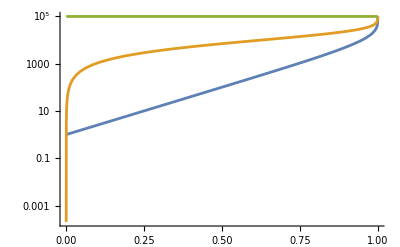

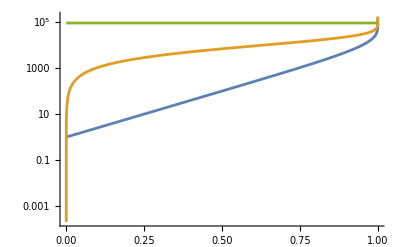

1

```mathematica
n=10000;
LogPlot[{n*(HarmonicNumber[n]-HarmonicNumber[n-n^k]),n*(HarmonicNumber[n]-HarmonicNumber[n-n*k]),n*HarmonicNumber[n]},{k,0,1}]
LogPlot[{n*(Log[n]-Log[n-n^k]),n*(Log[n]-Log[n-n*k]),n*Log[n]},{k,0,1}]
Clear[n]
Assuming[0<=k<1,Limit[Log[n-n^k]/Log[n],n->Infinity]]
```

```mathematica
f[n_,k_]:=Sum[(i Binomial[n,i] (n-i+1)/n) Binomial[(n-1)^2-i,k-i],{i,0,2n-1}]
f[n,k]
Asymptotic[(i Binomial[n,i] (n-i+1)/n) Binomial[(n-1)^2-i,k-i],n->Infinity]
AsymptoticSum[(i Binomial[n,i] (n-i+1)/n) Binomial[(n-1)^2-i,k-i]//FullSimplify,{i,0,2n},n->Infinity]
Sum[n^(-1+2 (2-i)+i-2 (2-k)) (n/((-i+k) Gamma[i] Gamma[-i+k])),{i,0,2n-1}]
```

Binomial[(-2+n) n,-1+k] Hypergeometric2F1[1-k,1-n,-((-2+n) n),-1]+n Binomial[(-2+n) n,-1+k] Hypergeometric2F1[1-k,1-n,-((-2+n) n),-1]+2 (-1+n) Binomial[n,2 n] Binomial[1-4 n+n^2,k-2 n] HypergeometricPFQ[{1,n,-k+2 n},{1+2 n,-1+4 n-n^2},-1]-Binomial[(-2+n) n,-1+k] HypergeometricPFQ[{2,1-k,1-n},{1,2 n-n^2},-1]+3 Binomial[n,1+2 n] Binomial[(-4+n) n,-1+k-2 n] HypergeometricPFQ[{2,1+n,1-k+2 n},{2+2 n,4 n-n^2},-1]-(Binomial[n,1+2 n] Binomial[(-4+n) n,-1+k-2 n] HypergeometricPFQ[{2,1+n,1-k+2 n},{2+2 n,4 n-n^2},-1])/n+(Binomial[n,1+2 n] Binomial[(-4+n) n,-1+k-2 n] HypergeometricPFQ[{2,2,1+n,1-k+2 n},{1,2+2 n,4 n-n^2},-1])/n

n^(-1+2 (2-i)+i-2 (2-k)) ((-2-3 i+i^2+4 k)/(2 (i-k) Gamma[i] Gamma[-i+k])+(-70 i-21 i^2+22 i^3-3 i^4+60 k+72 i k-24 i^2 k-36 k^2)/(24 (i-k) n Gamma[i] Gamma[-i+k])+n/((-i+k) Gamma[i] Gamma[-i+k]))

n^(-2 (2-k)) ((3 (-2+k))/(2 Gamma[-1+k])+(-12+8 k-k^2)/(3 n Gamma[-1+k])-(2 n)/Gamma[-1+k]+n^2/((-1+k) Gamma[-1+k])) Hypergeometric2F1[1-k,1-n,2 n-n^2,-1]+n^(-2 (2-k)) ((-12+8 k-k^2)/(3 Gamma[-1+k])-(5 (24-14 k-k^2+k^3))/(24 n Gamma[-1+k])+(3 (-2+k) n)/(2 Gamma[-1+k])-(2 n^2)/Gamma[-1+k]+n^3/((-1+k) Gamma[-1+k])) Hypergeometric2F1[1-k,1-n,2 n-n^2,-1]+n^(-2 (2-k)) (-(3 (-2+k))/(2 Gamma[-1+k])+(12-8 k+k^2)/(3 n Gamma[-1+k])+(2 n)/Gamma[-1+k]-n^2/((-1+k) Gamma[-1+k])) HypergeometricPFQ[{2,1-k,1-n},{1,2 n-n^2},-1]+2^(1-Floor[1/2+Arg[1+n]/(2 π)]-Floor[1/2+Arg[2-k+2 n]/(2 π)]) ⅇ^(6+(239-18 k+6 k^2)/(24 n)+n (-2-2 Log[2]-5 Log[n])+(1/2+n) Log[(-1)^Floor[1/2+Arg[1+n]/(2 π)] n]+(3/2-k+2 n) Log[2 (-1)^Floor[1/2+Arg[2-k+2 n]/(2 π)] n]) n^(-2 (2-k)) (-(-13+36 k)/(48 √2 π^2)+(-1991-1800 k+864 k^2)/(2304 √2 n π^2)+n/(2 √2 π^2)) π (-Csc[n π])^Floor[1/2+Arg[1+n]/(2 π)] (-Csc[(-2+k) π-2 n π])^Floor[1/2+Arg[2-k+2 n]/(2 π)] HypergeometricPFQ[{1,1+n,1-k+2 n},{2+2 n,4 n-n^2},-1] Sin[n π] Sin[(-1+k) π-2 n π]

n^k ((1+n)^(-1+k)/((-1+k) Gamma[-1+k])-(n^(k-2 n) Hypergeometric2F1[1,-k+2 n,2 n,-1/n])/((k-2 n) Gamma[k-2 n] Gamma[2 n]))

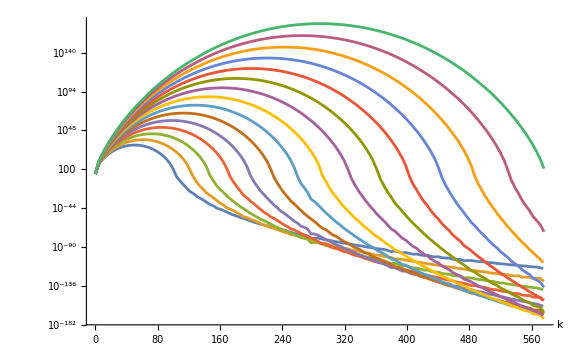

$Aborted

```mathematica
rec[n_,k_]:=Piecewise[{{0,k<=0||k>n^2},{n^2,k==1},{Sum[rec[n-1,k-i]+(i Binomial[n,i] (n-i+1)/n) Binomial[(n-2)^2,k-i]//FullSimplify,{i,0,2n-1}],True}}]
rec1[n_,k_]:=Piecewise[{{0,k<=0||k>n^2},{n^2,k==1},{Sum[rec1[n-1,k-i]+(i Binomial[n,i] (n-i+1)/n) Binomial[(n-1)^2-i,k-i]//FullSimplify,{i,0,2n-1}],True}}]
SetOptions[$FrontEndSession,AutoStyleOptions->{"HighlightFormattingErrors"->False}]
Style[LogPlot[Evaluate[Table[k*Binomial[n^2,k],{n,10,24}]],{k,0,24^2},PlotRange->Full,AxesLabel->{"k"},ImageSize->Large,PlotPoints->3,WorkingPrecision->256],AutoStyleOptions->{"HighlightFormattingErrors"->False}]
```